# Calculation of scattering amplitudes in N-sf-N-I-S with s-wave when up-spin electron is incident from normal metal

```mathematica
(*PS1={{u},{0},{0},{v}};
PS2={{0},{u},{-v},{0}};
PS3={{0},{-v},{u},{0}};
PS4={{v},{0},{0},{u}};*)
PS1={{u},{0},{0},{v}};
PS2={{0},{u},{-v},{0}};
PS3={{0},{-v},{u},{0}};
PS4={{v},{0},{0},{u}};
P1N={{1},{0},{0},{0}};
P2N={{0},{1},{0},{0}};
P3N={{0},{0},{1},{0}};
P4N={{0},{0},{0},{1}};
PN1=P1N*Exp[I*ke*x]+ruu*P1N*Exp[-I*ke*x]+rdu*Exp[-I*ke*x]P2N+rauu*P3N*Exp[I*ke*x]+radu*P4N*Exp[I*ke*x];
PN2=tuu*P1N*Exp[I*ke*x]+tdu*P2N*Exp[I*ke*x]+fuu*P1N*Exp[-I*ke*(x-a)]+fdu*P2N*Exp[-I*ke*(x-a)]+guu*P3N*Exp[I*ke(x-a)]+gdu*P4N*Exp[I*ke(x-a)]+huu*P3N*Exp[-I*ke*x]+hdu*P4N*Exp[-I*ke*x];
PS=cuu*Exp[I*ke*x]*PS1+cdu*Exp[I*ke*x]*PS2+duu*Exp[-I*ke*x]PS3+ddu*Exp[-I*ke*x]*PS4;
s5=(1+ruu)((m/2)*P1N+(f/2)*P2N)+rdu*((f/2)*P1N+(-(m+1)/2)*P2N)+rauu*((-(m+1)/2)*P3N+(f/2)*P4N)+radu*((f/2)*P3N+((m)/2)*P4N);
n1=(PN1-PN2)/.{x->0};
n2=-I(D[PN2,x]-D[PN1,x])-(2I*J)*ke*s5/.{x->0};
n3=(PN2-PS)/.{x->a}//Simplify;
n4=(-I(D[PS,x]-D[PN2,x])+2I*Z*ke*PN2)/.{x->a};
A1=Part[n1,1,1];
A2=Part[n1,2,1];
A3=Part[n1,3,1];
A4=Part[n1,4,1];
B1=Part[n2,1,1];
B2=Part[n2,2,1];
B3=Part[n2,3,1];
B4=Part[n2,4,1];
C1=Part[n3,1,1];
C2=Part[n3,2,1];
C3=Part[n3,3,1];
C4=Part[n3,4,1];
D1=Part[n4,1,1];
D2=Part[n4,2,1];
D3=Part[n4,3,1];
D4=Part[n4,4,1];
P=Solve[{A1==0,A2==0,A3==0,A4==0,B1==0,B2==0,B3==0,B4==0,C1==0,C2==0,C3==0,C4==0,D1==0,D2==0,D3==0,D4==0},{ruu,tuu,fuu,rdu,tdu,fdu,rauu,guu,huu,radu,gdu,hdu,cuu,ddu,cdu,duu}];
z1=ruu/.P[[1]];
z4=rdu/.P[[1]];
z7=rauu/.P[[1]];
z10=radu/.P[[1]];
(*kf=0.85*π/a;*)
a=1;
ds=1;
(*Z=1;*)
(*m=-1/2;
f=1;*)
(*J=1;*)
Ef=50;
Rehuu=Abs[z7]^2;
Rehdu=Abs[z10]^2;
Reeuu=Abs[z1]^2;
Reedu=Abs[z4]^2;
Teeuu=Abs[z13]^2(Abs[u]^2-Abs[v]^2);
Tehuu=Abs[z16]^2(Abs[u]^2-Abs[v]^2);
Teedu=Abs[z15]^2(Abs[u]^2-Abs[v]^2);
Tehdu=Abs[z14]^2(Abs[u]^2-Abs[v]^2);
(*u=Piecewise[{{√(1/2(1+√((G^2-ds^2)/G^2))),G^2>ds^2},{√(1/2(1+I √((ds^2-G^2)/G^2))),G^2<ds^2}}];
v=Piecewise[{{√(1/2(1-√((G^2-ds^2)/G^2))),G^2>ds^2},{√(1/2(1-I √((ds^2-G^2)/G^2))),G^2<ds^2}}];
Plot[1+Rehuu+Rehdu-Reeuu-Reedu,{G,-2,2},PlotRange->{0,2}]
Plot[Rehuu+Rehdu+Reeuu+Reedu+Teeuu+Teedu+Tehuu+Tehdu,{G,-2,2},PlotRange->{0,2}]*)
```

# Probability conservation

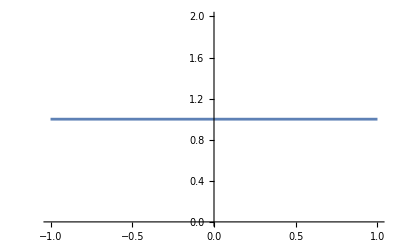

```mathematica
u=Piecewise[{{√(1/2(1+√((G^2-ds^2)/G^2))),G^2>ds^2},{√(1/2(1+I √((ds^2-G^2)/G^2))),G^2<ds^2}}];
v=Piecewise[{{√(1/2(1-√((G^2-ds^2)/G^2))),G^2>ds^2},{√(1/2(1-I √((ds^2-G^2)/G^2))),G^2<ds^2}}];
kf=0.85*π/a;
a=1;
ds=1;
Z=1;
m=-0.5;
f=1;
J=1;
Ef=50;
ke=kf;
Plot[Rehuu+Rehdu+Reeuu+Reedu+Teeuu+Teedu+Tehuu+Tehdu,{G,-2,2},PlotRange->{0,2}]
```

```mathematica
z1//Simplify(*Subscript[r, N]^(↑↑)*)
z4//Simplify(*Subscript[r, N]^(↓↑)*)
z7//Simplify(*Subscript[r, Na]^(↑↑)*)
z10//Simplify(*Subscript[r, Na]^(↓↑)*)
```

-((J^3 (f^2+m+m^2) (f^2 J+m (-2 ⅈ+J+J m)) (u^2-v^2)^2 Z^2 (-ⅈ+Z)^2+ⅇ^(8 ⅈ ke) J (-8 ⅈ (1+m)+4 J (-1+f^2+m^2)-2 ⅈ J^2 (2+m) (f^2+m+m^2)+J^3 (f^2+m+m^2)^2) (u^2-v^2)^2 Z^2 (ⅈ+Z)^2-2 ⅇ^(6 ⅈ ke) (u^2-v^2) Z (ⅈ+Z) (u^2 (-8 (1+Z^2)-8 ⅈ J m (1+Z^2)-ⅈ J^3 (3+2 m) (f^2+m+m^2) (1+2 Z^2)+J^4 (f^2+m+m^2)^2 (1+2 Z^2)+2 J^2 (-1-2 Z^2+f^2 (1+Z^2)+m^2 (1+Z^2)-m (1+2 Z^2)))+v^2 (8 Z^2+8 ⅈ J m Z^2+ⅈ J^3 (3+2 m) (f^2+m+m^2) (1+2 Z^2)-J^4 (f^2+m+m^2)^2 (1+2 Z^2)+J^2 (2-2 (-2+f^2) Z^2-2 m^2 Z^2+m (2+4 Z^2))))-2 ⅇ^(2 ⅈ ke) J^2 (u^2-v^2) Z (-ⅈ+Z) (f^4 J^2 (u^2-v^2) (1+2 Z^2)+f^2 (-2 u^2 Z^2+2 v^2 (1+Z^2)+2 J^2 m (1+m) (u^2-v^2) (1+2 Z^2)-ⅈ J (1+2 m) (u^2-v^2) (1+2 Z^2))+m (u^2 (-2-2 (2+m) Z^2+J^2 m (1+m)^2 (1+2 Z^2)-ⅈ J (1+3 m+2 m^2) (1+2 Z^2))+v^2 (-J^2 m (1+m)^2 (1+2 Z^2)+ⅈ J (1+3 m+2 m^2) (1+2 Z^2)+2 (1+m+2 Z^2+m Z^2))))+ⅇ^(4 ⅈ ke) J (f^4 J^3 (u^2-v^2)^2 (1+6 Z^2+6 Z^4)+2 f^2 J (u^4 (2-2 Z^4-ⅈ J (1+m) (1+6 Z^2+6 Z^4)+J^2 m (1+m) (1+6 Z^2+6 Z^4))-2 u^2 v^2 (-3-2 Z^2-2 Z^4-ⅈ J (1+m) (1+6 Z^2+6 Z^4)+J^2 m (1+m) (1+6 Z^2+6 Z^4))+v^4 (-2 Z^2 (2+Z^2)-ⅈ J (1+m) (1+6 Z^2+6 Z^4)+J^2 m (1+m) (1+6 Z^2+6 Z^4)))+(u^2-v^2) (-4 (-2 ⅈ+J) (u^2-v^2) Z^2 (1+Z^2)+2 J^2 (-ⅈ+J) m^3 (u^2-v^2) (1+6 Z^2+6 Z^4)+J^3 m^4 (u^2-v^2) (1+6 Z^2+6 Z^4)-2 ⅈ m (-v^2 (4 Z^4-8 ⅈ J (Z^2+Z^4)+J^2 (1+6 Z^2+6 Z^4))+u^2 (4 (1+Z^2)^2-8 ⅈ J (Z^2+Z^4)+J^2 (1+6 Z^2+6 Z^4)))+J m^2 (v^2 (4 Z^2 (2+Z^2)+4 ⅈ J (1+6 Z^2+6 Z^4)-J^2 (1+6 Z^2+6 Z^4))+u^2 (4-4 Z^4-4 ⅈ J (1+6 Z^2+6 Z^4)+J^2 (1+6 Z^2+6 Z^4))))))/(J^2 (f^2+m+m^2) (4+2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (-ⅈ+Z)^2+ⅇ^(8 ⅈ ke) J^2 (f^2+m+m^2) (4-2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (ⅈ+Z)^2-2 ⅇ^(6 ⅈ ke) J (u^2-v^2) Z (ⅈ+Z) (u^2 (4 ⅈ (1+Z^2)+2 J (1+2 f^2+2 m+2 m^2) (1+Z^2)-ⅈ J^2 (f^2+m+m^2) (1+2 Z^2)+J^3 (f^2+m+m^2)^2 (1+2 Z^2))-v^2 (4 ⅈ Z^2+2 J (1+2 m+2 m^2) Z^2+f^4 J^3 (1+2 Z^2)-ⅈ J^2 m (1+m) (1+2 Z^2)+J^3 m^2 (1+m)^2 (1+2 Z^2)+f^2 J (4 Z^2-ⅈ J (1+2 Z^2)+2 J^2 m (1+m) (1+2 Z^2))))-2 ⅇ^(2 ⅈ ke) J (u^2-v^2) Z (-ⅈ+Z) (u^2 (-4 ⅈ (1+Z^2)+2 J (1+2 f^2+2 m+2 m^2) (1+Z^2)+ⅈ J^2 (f^2+m+m^2) (1+2 Z^2)+J^3 (f^2+m+m^2)^2 (1+2 Z^2))-v^2 (-4 ⅈ Z^2+2 J (1+2 m+2 m^2) Z^2+f^4 J^3 (1+2 Z^2)+ⅈ J^2 m (1+m) (1+2 Z^2)+J^3 m^2 (1+m)^2 (1+2 Z^2)+f^2 J (4 Z^2+ⅈ J (1+2 Z^2)+2 J^2 m (1+m) (1+2 Z^2))))+ⅇ^(4 ⅈ ke) (u^4 (16 (1+Z^2)^2+J^4 (f^2+m+m^2)^2 (1+6 Z^2+6 Z^4)+4 J^2 (1+Z^2) (1+2 Z^2+2 f^2 (1+Z^2)+2 m (1+Z^2)+2 m^2 (1+Z^2)))+v^4 (16 Z^4+f^4 J^4 (1+6 Z^2+6 Z^4)+J^4 m^2 (1+m)^2 (1+6 Z^2+6 Z^4)+4 J^2 (Z^2+2 (1+m+m^2) Z^4)+2 f^2 (4 J^2 Z^4+J^4 m (1+m) (1+6 Z^2+6 Z^4)))-2 u^2 v^2 (16 (Z^2+Z^4)+J^4 (f^2+m+m^2)^2 (1+6 Z^2+6 Z^4)+J^2 (2 (1+2 Z^2)^2+f^2 (-4+8 Z^2+8 Z^4)+m (4+8 Z^2+8 Z^4)+m^2 (4+8 Z^2+8 Z^4))))))

(f J (-J^2 (f^2+m+m^2) (u^2-v^2) Z (-ⅈ+Z)+ⅇ^(6 ⅈ ke) (4-2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2) Z (ⅈ+Z)+ⅇ^(2 ⅈ ke) J (-2 ⅈ (u^2-v^2) Z (-ⅈ+Z)+f^2 J (u^2-v^2) (1-ⅈ Z+3 Z^2)+J m^2 (u^2-v^2) (1-ⅈ Z+3 Z^2)-m v^2 (J-4 Z-ⅈ J Z+3 J Z^2)+m u^2 (4 ⅈ+J-4 Z-ⅈ J Z+3 J Z^2))+ⅇ^(4 ⅈ ke) (-u^2 (-2 J (ⅈ+2 m Z+2 ⅈ Z^2)+4 (1+ⅈ Z+Z^2)+J^2 (f^2+m+m^2) (1+ⅈ Z+3 Z^2))+v^2 (-4 J m (ⅈ+Z)+4 (-1+ⅈ Z+Z^2)-2 ⅈ J (1+2 Z^2)+J^2 (f^2+m+m^2) (1+ⅈ Z+3 Z^2)))-((-J^2 (f^2+m+m^2) (u^2-v^2) Z (-ⅈ+Z)+ⅇ^(6 ⅈ ke) (4-2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2) Z (ⅈ+Z)+ⅇ^(2 ⅈ ke) (-v^2 (-4 ⅈ Z-2 J (1+2 m+ⅈ Z) Z+f^2 J^2 (1-ⅈ Z+3 Z^2)+J^2 m (1+m) (1-ⅈ Z+3 Z^2))+u^2 (-4-4 ⅈ Z-2 J (2 m+ⅈ Z) (-ⅈ+Z)+f^2 J^2 (1-ⅈ Z+3 Z^2)+J^2 m (1+m) (1-ⅈ Z+3 Z^2)))+ⅇ^(4 ⅈ ke) (-u^2 (-2 J (ⅈ+2 m Z+2 ⅈ Z^2)+4 (1+Z^2)+J^2 (f^2+m+m^2) (1+ⅈ Z+3 Z^2))+v^2 (4 Z^2-4 J m (ⅈ+Z)-2 ⅈ J (1+2 Z^2)+J^2 (f^2+m+m^2) (1+ⅈ Z+3 Z^2)))) (J^3 (f^2+m+m^2) (f^2 J+m (-2 ⅈ+J+J m)) (u^2-v^2)^2 Z^2 (-ⅈ+Z)^2+ⅇ^(8 ⅈ ke) J (-8 ⅈ (1+m)+4 J (-1+f^2+m^2)-2 ⅈ J^2 (2+m) (f^2+m+m^2)+J^3 (f^2+m+m^2)^2) (u^2-v^2)^2 Z^2 (ⅈ+Z)^2-2 ⅇ^(6 ⅈ ke) (u^2-v^2) Z (ⅈ+Z) (u^2 (-8 (1+Z^2)-8 ⅈ J m (1+Z^2)-ⅈ J^3 (3+2 m) (f^2+m+m^2) (1+2 Z^2)+J^4 (f^2+m+m^2)^2 (1+2 Z^2)+2 J^2 (-1-2 Z^2+f^2 (1+Z^2)+m^2 (1+Z^2)-m (1+2 Z^2)))+v^2 (8 Z^2+8 ⅈ J m Z^2+ⅈ J^3 (3+2 m) (f^2+m+m^2) (1+2 Z^2)-J^4 (f^2+m+m^2)^2 (1+2 Z^2)+J^2 (2-2 (-2+f^2) Z^2-2 m^2 Z^2+m (2+4 Z^2))))-2 ⅇ^(2 ⅈ ke) J^2 (u^2-v^2) Z (-ⅈ+Z) (f^4 J^2 (u^2-v^2) (1+2 Z^2)+f^2 (-2 u^2 Z^2+2 v^2 (1+Z^2)+2 J^2 m (1+m) (u^2-v^2) (1+2 Z^2)-ⅈ J (1+2 m) (u^2-v^2) (1+2 Z^2))+m (u^2 (-2-2 (2+m) Z^2+J^2 m (1+m)^2 (1+2 Z^2)-ⅈ J (1+3 m+2 m^2) (1+2 Z^2))+v^2 (-J^2 m (1+m)^2 (1+2 Z^2)+ⅈ J (1+3 m+2 m^2) (1+2 Z^2)+2 (1+m+2 Z^2+m Z^2))))+ⅇ^(4 ⅈ ke) J (f^4 J^3 (u^2-v^2)^2 (1+6 Z^2+6 Z^4)+2 f^2 J (u^4 (2-2 Z^4-ⅈ J (1+m) (1+6 Z^2+6 Z^4)+J^2 m (1+m) (1+6 Z^2+6 Z^4))-2 u^2 v^2 (-3-2 Z^2-2 Z^4-ⅈ J (1+m) (1+6 Z^2+6 Z^4)+J^2 m (1+m) (1+6 Z^2+6 Z^4))+v^4 (-2 Z^2 (2+Z^2)-ⅈ J (1+m) (1+6 Z^2+6 Z^4)+J^2 m (1+m) (1+6 Z^2+6 Z^4)))+(u^2-v^2) (-4 (-2 ⅈ+J) (u^2-v^2) Z^2 (1+Z^2)+2 J^2 (-ⅈ+J) m^3 (u^2-v^2) (1+6 Z^2+6 Z^4)+J^3 m^4 (u^2-v^2) (1+6 Z^2+6 Z^4)-2 ⅈ m (-v^2 (4 Z^4-8 ⅈ J (Z^2+Z^4)+J^2 (1+6 Z^2+6 Z^4))+u^2 (4 (1+Z^2)^2-8 ⅈ J (Z^2+Z^4)+J^2 (1+6 Z^2+6 Z^4)))+J m^2 (v^2 (4 Z^2 (2+Z^2)+4 ⅈ J (1+6 Z^2+6 Z^4)-J^2 (1+6 Z^2+6 Z^4))+u^2 (4-4 Z^4-4 ⅈ J (1+6 Z^2+6 Z^4)+J^2 (1+6 Z^2+6 Z^4)))))))/(J^2 (f^2+m+m^2) (4+2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (-ⅈ+Z)^2+ⅇ^(8 ⅈ ke) J^2 (f^2+m+m^2) (4-2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (ⅈ+Z)^2-2 ⅇ^(6 ⅈ ke) J (u^2-v^2) Z (ⅈ+Z) (u^2 (4 ⅈ (1+Z^2)+2 J (1+2 f^2+2 m+2 m^2) (1+Z^2)-ⅈ J^2 (f^2+m+m^2) (1+2 Z^2)+J^3 (f^2+m+m^2)^2 (1+2 Z^2))-v^2 (4 ⅈ Z^2+2 J (1+2 m+2 m^2) Z^2+f^4 J^3 (1+2 Z^2)-ⅈ J^2 m (1+m) (1+2 Z^2)+J^3 m^2 (1+m)^2 (1+2 Z^2)+f^2 J (4 Z^2-ⅈ J (1+2 Z^2)+2 J^2 m (1+m) (1+2 Z^2))))-2 ⅇ^(2 ⅈ ke) J (u^2-v^2) Z (-ⅈ+Z) (u^2 (-4 ⅈ (1+Z^2)+2 J (1+2 f^2+2 m+2 m^2) (1+Z^2)+ⅈ J^2 (f^2+m+m^2) (1+2 Z^2)+J^3 (f^2+m+m^2)^2 (1+2 Z^2))-v^2 (-4 ⅈ Z^2+2 J (1+2 m+2 m^2) Z^2+f^4 J^3 (1+2 Z^2)+ⅈ J^2 m (1+m) (1+2 Z^2)+J^3 m^2 (1+m)^2 (1+2 Z^2)+f^2 J (4 Z^2+ⅈ J (1+2 Z^2)+2 J^2 m (1+m) (1+2 Z^2))))+ⅇ^(4 ⅈ ke) (u^4 (16 (1+Z^2)^2+J^4 (f^2+m+m^2)^2 (1+6 Z^2+6 Z^4)+4 J^2 (1+Z^2) (1+2 Z^2+2 f^2 (1+Z^2)+2 m (1+Z^2)+2 m^2 (1+Z^2)))+v^4 (16 Z^4+f^4 J^4 (1+6 Z^2+6 Z^4)+J^4 m^2 (1+m)^2 (1+6 Z^2+6 Z^4)+4 J^2 (Z^2+2 (1+m+m^2) Z^4)+2 f^2 (4 J^2 Z^4+J^4 m (1+m) (1+6 Z^2+6 Z^4)))-2 u^2 v^2 (16 (Z^2+Z^4)+J^4 (f^2+m+m^2)^2 (1+6 Z^2+6 Z^4)+J^2 (2 (1+2 Z^2)^2+f^2 (-4+8 Z^2+8 Z^4)+m (4+8 Z^2+8 Z^4)+m^2 (4+8 Z^2+8 Z^4)))))))/(-J^2 (-2 ⅈ+J+J m) (f^2+m+m^2) (u^2-v^2) Z (-ⅈ+Z)+ⅇ^(6 ⅈ ke) J (1+m) (4-2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2) Z (ⅈ+Z)+ⅇ^(2 ⅈ ke) J (-2 ⅈ (-2 ⅈ+J) (u^2-v^2) Z (-ⅈ+Z)+J^2 m^3 (u^2-v^2) (1-ⅈ Z+3 Z^2)+2 J m^2 (u^2-v^2) (J-2 Z-ⅈ J Z-2 ⅈ Z^2+3 J Z^2)-m v^2 (4 ⅈ Z-6 ⅈ J Z (-ⅈ+Z)+J^2 (1-ⅈ Z+3 Z^2))+m u^2 (4+4 ⅈ Z-6 ⅈ J Z (-ⅈ+Z)+J^2 (1-ⅈ Z+3 Z^2))+f^2 J (-v^2 (-4 ⅈ Z^2+J (1+m) (1-ⅈ Z+3 Z^2))+u^2 (-4 ⅈ (1+Z^2)+J (1+m) (1-ⅈ Z+3 Z^2))))+ⅇ^(4 ⅈ ke) (v^2 (-8 ⅈ Z^2+4 J m Z^2+J^3 (1+m) (f^2+m+m^2) (1+ⅈ Z+3 Z^2)-2 ⅈ J^2 (f^2 (-1+ⅈ Z+Z^2)+(1+m) (1+2 Z^2+m (1-ⅈ Z+Z^2))))-u^2 (-8 ⅈ (1+Z^2)+4 J m (1+Z^2)+J^3 (1+m) (f^2+m+m^2) (1+ⅈ Z+3 Z^2)-2 ⅈ J^2 (f^2 (1+ⅈ Z+Z^2)+(1+m) (1+2 Z^2+m (1-ⅈ Z+Z^2))))))

(f J (-ⅈ (J (f^2 J+m (-2 ⅈ+J+J m)) (u^2-v^2) Z (-ⅈ+Z) (-v^2 Z+u^2 (-ⅈ+Z))+ⅇ^(6 ⅈ ke) J (f^2 J+(1+m) (-2 ⅈ+J m)) (u^2-v^2) Z (ⅈ+Z) (-u^2 Z+v^2 (ⅈ+Z))+ⅇ^(4 ⅈ ke) (v^4 (ⅈ+Z) (-4 Z^2+J^2 (f^2+m+m^2) (1+3 Z^2)-2 ⅈ J (1+m+2 Z^2+3 m Z^2))+u^4 Z (-4 (1+Z^2)+J^2 (f^2+m+m^2) (2+3 Z^2)-2 ⅈ J (1+2 Z^2+m (2+3 Z^2)))-u^2 v^2 (-4 (2 ⅈ+Z+ⅈ Z^2+2 Z^3)+J^2 (f^2+m+m^2) (ⅈ+3 Z+3 ⅈ Z^2+6 Z^3)+2 J (1-2 ⅈ Z+2 Z^2-4 ⅈ Z^3+3 m (1-ⅈ Z+Z^2-2 ⅈ Z^3))))-ⅇ^(2 ⅈ ke) (-4 (u^2-v^2) Z (-ⅈ+Z) (u^2 Z-v^2 (ⅈ+Z))+f^2 J^2 (u^2-v^2) (-v^2 Z (2+3 Z^2)+u^2 (-ⅈ+Z-3 ⅈ Z^2+3 Z^3))+J^2 m (1+m) (u^2-v^2) (-v^2 Z (2+3 Z^2)+u^2 (-ⅈ+Z-3 ⅈ Z^2+3 Z^3))-2 ⅈ J ((u^2-v^2) Z (-ⅈ+Z) (u^2 Z-v^2 (ⅈ+Z))+m (v^4 Z (2+3 Z^2)+u^4 (-ⅈ+Z-3 ⅈ Z^2+3 Z^3)-u^2 v^2 (ⅈ+3 Z-3 ⅈ Z^2+6 Z^3)))))-((ⅇ^(6 ⅈ ke) J^2 (f^2+m+m^2) (u^2-v^2) Z (ⅈ+Z) (v^2 (1-ⅈ Z)+ⅈ u^2 Z)-ⅈ (4+2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2) Z (-ⅈ+Z) (-v^2 Z+u^2 (-ⅈ+Z))+ⅈ ⅇ^(2 ⅈ ke) (u^4 (-ⅈ+Z) (4 (1+Z^2)+2 ⅈ J (1+2 Z^2)+J^2 (f^2+m+m^2) (1+3 Z^2))+v^4 Z (4 Z^2+2 ⅈ J (1+2 Z^2)+J^2 (f^2+m+m^2) (2+3 Z^2))-u^2 v^2 (4 Z (1-ⅈ Z+2 Z^2)+J (2+4 m+4 ⅈ Z+4 Z^2+8 ⅈ Z^3)+J^2 (f^2+m+m^2) (-ⅈ+3 Z-3 ⅈ Z^2+6 Z^3)))-ⅈ ⅇ^(4 ⅈ ke) (J u^4 Z (2 ⅈ (1+Z^2)+f^2 J (2+3 Z^2)+J m (1+m) (2+3 Z^2))+J v^4 (ⅈ+Z) (2 ⅈ Z^2+J m (1+m) (1+3 Z^2)+f^2 (J+3 J Z^2))-u^2 v^2 (-4 ⅈ+4 J m+2 ⅈ J Z (1+ⅈ Z+2 Z^2)+f^2 J^2 (ⅈ+3 Z+3 ⅈ Z^2+6 Z^3)+J^2 m (1+m) (ⅈ+3 Z+3 ⅈ Z^2+6 Z^3)))) (J^3 (f^2+m+m^2) (f^2 J+m (-2 ⅈ+J+J m)) (u^2-v^2)^2 Z^2 (-ⅈ+Z)^2+ⅇ^(8 ⅈ ke) J (-8 ⅈ (1+m)+4 J (-1+f^2+m^2)-2 ⅈ J^2 (2+m) (f^2+m+m^2)+J^3 (f^2+m+m^2)^2) (u^2-v^2)^2 Z^2 (ⅈ+Z)^2-2 ⅇ^(6 ⅈ ke) (u^2-v^2) Z (ⅈ+Z) (u^2 (-8 (1+Z^2)-8 ⅈ J m (1+Z^2)-ⅈ J^3 (3+2 m) (f^2+m+m^2) (1+2 Z^2)+J^4 (f^2+m+m^2)^2 (1+2 Z^2)+2 J^2 (-1-2 Z^2+f^2 (1+Z^2)+m^2 (1+Z^2)-m (1+2 Z^2)))+v^2 (8 Z^2+8 ⅈ J m Z^2+ⅈ J^3 (3+2 m) (f^2+m+m^2) (1+2 Z^2)-J^4 (f^2+m+m^2)^2 (1+2 Z^2)+J^2 (2-2 (-2+f^2) Z^2-2 m^2 Z^2+m (2+4 Z^2))))-2 ⅇ^(2 ⅈ ke) J^2 (u^2-v^2) Z (-ⅈ+Z) (f^4 J^2 (u^2-v^2) (1+2 Z^2)+f^2 (-2 u^2 Z^2+2 v^2 (1+Z^2)+2 J^2 m (1+m) (u^2-v^2) (1+2 Z^2)-ⅈ J (1+2 m) (u^2-v^2) (1+2 Z^2))+m (u^2 (-2-2 (2+m) Z^2+J^2 m (1+m)^2 (1+2 Z^2)-ⅈ J (1+3 m+2 m^2) (1+2 Z^2))+v^2 (-J^2 m (1+m)^2 (1+2 Z^2)+ⅈ J (1+3 m+2 m^2) (1+2 Z^2)+2 (1+m+2 Z^2+m Z^2))))+ⅇ^(4 ⅈ ke) J (f^4 J^3 (u^2-v^2)^2 (1+6 Z^2+6 Z^4)+2 f^2 J (u^4 (2-2 Z^4-ⅈ J (1+m) (1+6 Z^2+6 Z^4)+J^2 m (1+m) (1+6 Z^2+6 Z^4))-2 u^2 v^2 (-3-2 Z^2-2 Z^4-ⅈ J (1+m) (1+6 Z^2+6 Z^4)+J^2 m (1+m) (1+6 Z^2+6 Z^4))+v^4 (-2 Z^2 (2+Z^2)-ⅈ J (1+m) (1+6 Z^2+6 Z^4)+J^2 m (1+m) (1+6 Z^2+6 Z^4)))+(u^2-v^2) (-4 (-2 ⅈ+J) (u^2-v^2) Z^2 (1+Z^2)+2 J^2 (-ⅈ+J) m^3 (u^2-v^2) (1+6 Z^2+6 Z^4)+J^3 m^4 (u^2-v^2) (1+6 Z^2+6 Z^4)-2 ⅈ m (-v^2 (4 Z^4-8 ⅈ J (Z^2+Z^4)+J^2 (1+6 Z^2+6 Z^4))+u^2 (4 (1+Z^2)^2-8 ⅈ J (Z^2+Z^4)+J^2 (1+6 Z^2+6 Z^4)))+J m^2 (v^2 (4 Z^2 (2+Z^2)+4 ⅈ J (1+6 Z^2+6 Z^4)-J^2 (1+6 Z^2+6 Z^4))+u^2 (4-4 Z^4-4 ⅈ J (1+6 Z^2+6 Z^4)+J^2 (1+6 Z^2+6 Z^4)))))))/(J^2 (f^2+m+m^2) (4+2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (-ⅈ+Z)^2+ⅇ^(8 ⅈ ke) J^2 (f^2+m+m^2) (4-2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (ⅈ+Z)^2-2 ⅇ^(6 ⅈ ke) J (u^2-v^2) Z (ⅈ+Z) (u^2 (4 ⅈ (1+Z^2)+2 J (1+2 f^2+2 m+2 m^2) (1+Z^2)-ⅈ J^2 (f^2+m+m^2) (1+2 Z^2)+J^3 (f^2+m+m^2)^2 (1+2 Z^2))-v^2 (4 ⅈ Z^2+2 J (1+2 m+2 m^2) Z^2+f^4 J^3 (1+2 Z^2)-ⅈ J^2 m (1+m) (1+2 Z^2)+J^3 m^2 (1+m)^2 (1+2 Z^2)+f^2 J (4 Z^2-ⅈ J (1+2 Z^2)+2 J^2 m (1+m) (1+2 Z^2))))-2 ⅇ^(2 ⅈ ke) J (u^2-v^2) Z (-ⅈ+Z) (u^2 (-4 ⅈ (1+Z^2)+2 J (1+2 f^2+2 m+2 m^2) (1+Z^2)+ⅈ J^2 (f^2+m+m^2) (1+2 Z^2)+J^3 (f^2+m+m^2)^2 (1+2 Z^2))-v^2 (-4 ⅈ Z^2+2 J (1+2 m+2 m^2) Z^2+f^4 J^3 (1+2 Z^2)+ⅈ J^2 m (1+m) (1+2 Z^2)+J^3 m^2 (1+m)^2 (1+2 Z^2)+f^2 J (4 Z^2+ⅈ J (1+2 Z^2)+2 J^2 m (1+m) (1+2 Z^2))))+ⅇ^(4 ⅈ ke) (u^4 (16 (1+Z^2)^2+J^4 (f^2+m+m^2)^2 (1+6 Z^2+6 Z^4)+4 J^2 (1+Z^2) (1+2 Z^2+2 f^2 (1+Z^2)+2 m (1+Z^2)+2 m^2 (1+Z^2)))+v^4 (16 Z^4+f^4 J^4 (1+6 Z^2+6 Z^4)+J^4 m^2 (1+m)^2 (1+6 Z^2+6 Z^4)+4 J^2 (Z^2+2 (1+m+m^2) Z^4)+2 f^2 (4 J^2 Z^4+J^4 m (1+m) (1+6 Z^2+6 Z^4)))-2 u^2 v^2 (16 (Z^2+Z^4)+J^4 (f^2+m+m^2)^2 (1+6 Z^2+6 Z^4)+J^2 (2 (1+2 Z^2)^2+f^2 (-4+8 Z^2+8 Z^4)+m (4+8 Z^2+8 Z^4)+m^2 (4+8 Z^2+8 Z^4)))))))/(u v (-J^2 (-2 ⅈ+J+J m) (f^2+m+m^2) (u^2-v^2) Z (-ⅈ+Z)+ⅇ^(6 ⅈ ke) J (1+m) (4-2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2) Z (ⅈ+Z)+ⅇ^(2 ⅈ ke) J (-2 ⅈ (-2 ⅈ+J) (u^2-v^2) Z (-ⅈ+Z)+J^2 m^3 (u^2-v^2) (1-ⅈ Z+3 Z^2)+2 J m^2 (u^2-v^2) (J-2 Z-ⅈ J Z-2 ⅈ Z^2+3 J Z^2)-m v^2 (4 ⅈ Z-6 ⅈ J Z (-ⅈ+Z)+J^2 (1-ⅈ Z+3 Z^2))+m u^2 (4+4 ⅈ Z-6 ⅈ J Z (-ⅈ+Z)+J^2 (1-ⅈ Z+3 Z^2))+f^2 J (-v^2 (-4 ⅈ Z^2+J (1+m) (1-ⅈ Z+3 Z^2))+u^2 (-4 ⅈ (1+Z^2)+J (1+m) (1-ⅈ Z+3 Z^2))))+ⅇ^(4 ⅈ ke) (v^2 (-8 ⅈ Z^2+4 J m Z^2+J^3 (1+m) (f^2+m+m^2) (1+ⅈ Z+3 Z^2)-2 ⅈ J^2 (f^2 (-1+ⅈ Z+Z^2)+(1+m) (1+2 Z^2+m (1-ⅈ Z+Z^2))))-u^2 (-8 ⅈ (1+Z^2)+4 J m (1+Z^2)+J^3 (1+m) (f^2+m+m^2) (1+ⅈ Z+3 Z^2)-2 ⅈ J^2 (f^2 (1+ⅈ Z+Z^2)+(1+m) (1+2 Z^2+m (1-ⅈ Z+Z^2)))))))

(4 u v (ⅇ^(2 ⅈ ke) J (2 ⅈ (1+m)+J (f^2-(1+m)^2)) (u^2-v^2) Z (-ⅈ+Z)+ⅇ^(6 ⅈ ke) J (-2 ⅈ (1+m)+J (f^2-(1+m)^2)) (u^2-v^2) Z (ⅈ+Z)+ⅇ^(4 ⅈ ke) (u^2 (4 (1+Z^2)-J^2 (f^2-(1+m)^2) (1+2 Z^2))+v^2 (-4 Z^2+J^2 (f^2-(1+m)^2) (1+2 Z^2)))))/(J^2 (f^2+m+m^2) (4+2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (-ⅈ+Z)^2+ⅇ^(8 ⅈ ke) J^2 (f^2+m+m^2) (4-2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (ⅈ+Z)^2-2 ⅇ^(6 ⅈ ke) J (u^2-v^2) Z (ⅈ+Z) (u^2 (4 ⅈ (1+Z^2)+2 J (1+2 f^2+2 m+2 m^2) (1+Z^2)-ⅈ J^2 (f^2+m+m^2) (1+2 Z^2)+J^3 (f^2+m+m^2)^2 (1+2 Z^2))-v^2 (4 ⅈ Z^2+2 J (1+2 m+2 m^2) Z^2+f^4 J^3 (1+2 Z^2)-ⅈ J^2 m (1+m) (1+2 Z^2)+J^3 m^2 (1+m)^2 (1+2 Z^2)+f^2 J (4 Z^2-ⅈ J (1+2 Z^2)+2 J^2 m (1+m) (1+2 Z^2))))-2 ⅇ^(2 ⅈ ke) J (u^2-v^2) Z (-ⅈ+Z) (u^2 (-4 ⅈ (1+Z^2)+2 J (1+2 f^2+2 m+2 m^2) (1+Z^2)+ⅈ J^2 (f^2+m+m^2) (1+2 Z^2)+J^3 (f^2+m+m^2)^2 (1+2 Z^2))-v^2 (-4 ⅈ Z^2+2 J (1+2 m+2 m^2) Z^2+f^4 J^3 (1+2 Z^2)+ⅈ J^2 m (1+m) (1+2 Z^2)+J^3 m^2 (1+m)^2 (1+2 Z^2)+f^2 J (4 Z^2+ⅈ J (1+2 Z^2)+2 J^2 m (1+m) (1+2 Z^2))))+ⅇ^(4 ⅈ ke) (u^4 (16 (1+Z^2)^2+J^4 (f^2+m+m^2)^2 (1+6 Z^2+6 Z^4)+4 J^2 (1+Z^2) (1+2 Z^2+2 f^2 (1+Z^2)+2 m (1+Z^2)+2 m^2 (1+Z^2)))+v^4 (16 Z^4+f^4 J^4 (1+6 Z^2+6 Z^4)+J^4 m^2 (1+m)^2 (1+6 Z^2+6 Z^4)+4 J^2 (Z^2+2 (1+m+m^2) Z^4)+2 f^2 (4 J^2 Z^4+J^4 m (1+m) (1+6 Z^2+6 Z^4)))-2 u^2 v^2 (16 (Z^2+Z^4)+J^4 (f^2+m+m^2)^2 (1+6 Z^2+6 Z^4)+J^2 (2 (1+2 Z^2)^2+f^2 (-4+8 Z^2+8 Z^4)+m (4+8 Z^2+8 Z^4)+m^2 (4+8 Z^2+8 Z^4)))))

# Calculation of scattering amplitudes in N-sf-N-I-S with s-wave when up-spin electron is incident from superconductor

```mathematica
(*PS1={{u},{0},{0},{v}};
PS2={{0},{u},{-v},{0}};
PS3={{0},{-v},{u},{0}};
PS4={{v},{0},{0},{u}};*)
PS1={{u},{0},{0},{v}};
PS2={{0},{u},{-v},{0}};
PS3={{0},{-v},{u},{0}};
PS4={{v},{0},{0},{u}};
P1N={{1},{0},{0},{0}};
P2N={{0},{1},{0},{0}};
P3N={{0},{0},{1},{0}};
P4N={{0},{0},{0},{1}};
PS=PS1*Exp[-I*ke*x]+ruu*PS1*Exp[I*ke*x]+rdu*Exp[I*ke*x]PS2+rauu*PS3*Exp[-I*ke*x]+radu*PS4*Exp[-I*ke*x];
PN2=tuu*P1N*Exp[I*ke*x]+tdu*P2N*Exp[I*ke*x]+fuu*P1N*Exp[-I*ke*(x-a)]+fdu*P2N*Exp[-I*ke*(x-a)]+guu*P3N*Exp[I*ke(x-a)]+gdu*P4N*Exp[I*ke(x-a)]+huu*P3N*Exp[-I*ke*x]+hdu*P4N*Exp[-I*ke*x];
PN1=cuu*Exp[-I*ke*x]*P1N+cdu*Exp[-I*ke*x]*P2N+duu*Exp[I*ke*x]P3N+ddu*Exp[I*ke*x]*P4N;
s5=(cuu)((m/2)*P1N+(f/2)*P2N)+cdu*((f/2)*P1N+(-(m+1)/2)*P2N)+duu*((-(m+1)/2)*P3N+(f/2)*P4N)+ddu*((f/2)*P3N+((m)/2)*P4N);
n1=(PN1-PN2)/.{x->0};
n2=-I(D[PN2,x]-D[PN1,x])-(2I*J)*ke*s5/.{x->0};
n3=(PN2-PS)/.{x->a}//Simplify;
n4=(-I(D[PS,x]-D[PN2,x])+2I*Z*ke*PN2)/.{x->a};
A1=Part[n1,1,1];
A2=Part[n1,2,1];
A3=Part[n1,3,1];
A4=Part[n1,4,1];
B1=Part[n2,1,1];
B2=Part[n2,2,1];
B3=Part[n2,3,1];
B4=Part[n2,4,1];
C1=Part[n3,1,1];
C2=Part[n3,2,1];
C3=Part[n3,3,1];
C4=Part[n3,4,1];
D1=Part[n4,1,1];
D2=Part[n4,2,1];
D3=Part[n4,3,1];
D4=Part[n4,4,1];
P=Solve[{A1==0,A2==0,A3==0,A4==0,B1==0,B2==0,B3==0,B4==0,C1==0,C2==0,C3==0,C4==0,D1==0,D2==0,D3==0,D4==0},{ruu,tuu,fuu,rdu,tdu,fdu,rauu,guu,huu,radu,gdu,hdu,cuu,ddu,cdu,duu}];
z1=ruu/.P[[1]];
z2=tuu/.P[[1]];
z3=fuu/.P[[1]];
z4=rdu/.P[[1]];
z5=tdu/.P[[1]];
z6=fdu/.P[[1]];
z7=rauu/.P[[1]];
z8=guu/.P[[1]];
z9=huu/.P[[1]];
z10=radu/.P[[1]];
z11=gdu/.P[[1]];
z12=hdu/.P[[1]];
z13=cuu/.P[[1]];
z14=ddu/.P[[1]];
z15=cdu/.P[[1]];
z16=duu/.P[[1]];
(*kf=0.85*π/a;*)
a=1;
(*ds=1;
J=4.5;
Z=0.781;
Ef=50;
ke=kf;
m=-0.5;
f=1;*)
(*u=Piecewise[{{√(1/2(1+√((G^2-ds^2)/G^2))),G^2>ds^2},{√(1/2(1+I √((ds^2-G^2)/G^2))),G^2<ds^2}}];
v=Piecewise[{{√(1/2(1-√((G^2-ds^2)/G^2))),G^2>ds^2},{√(1/2(1-I √((ds^2-G^2)/G^2))),G^2<ds^2}}];
Plot[1+Rehuu+Rehdu-Reeuu-Reedu,{G,-2,2},PlotRange->{0,2}]
Plot[Rehuu+Rehdu+Reeuu+Reedu+Teeuu+Teedu+Tehuu+Tehdu,{G,-2,2},PlotRange->{0,2}]*)
```

# Probability conservation

```mathematica
u=Piecewise[{{√(1/2(1+√((G^2-ds^2)/G^2))),G^2>ds^2},{√(1/2(1+I √((ds^2-G^2)/G^2))),G^2<ds^2}}];
v=Piecewise[{{√(1/2(1-√((G^2-ds^2)/G^2))),G^2>ds^2},{√(1/2(1-I √((ds^2-G^2)/G^2))),G^2<ds^2}}];
kf=0.85*π/a;
a=1;
ds=1;
Z=1;
m=-0.5;
f=1;
J=1;
Ef=50;
ke=kf;
Plot[Rehuu+Rehdu+Reeuu+Reedu+Teeuu+Teedu+Tehuu+Tehdu,{G,-2,2},PlotRange->{0,2}]
```

-Graphics-

```mathematica
z13//Simplify(*Subscript[c, S]^(↑↑)*)
z15//Simplify(*Subscript[c, S]^(↓↑)*)
z16//Simplify(*Subscript[d, S]^(↑↑)*)
z14//Simplify(*Subscript[d, S]^(↓↑)*)
```

(2 u (u^2-v^2) (-f^2 J (-Z+ⅇ^(2 ⅈ ke) (ⅈ+Z))+((J (2 ⅈ (1+m)+J (f^2-(1+m)^2)) (u^2-v^2) Z (-ⅈ+Z)+ⅇ^(4 ⅈ ke) J (-2 ⅈ (1+m)+J (f^2-(1+m)^2)) (u^2-v^2) Z (ⅈ+Z)+ⅇ^(2 ⅈ ke) (u^2 (4 (1+Z^2)-J^2 (f^2-(1+m)^2) (1+2 Z^2))+v^2 (-4 Z^2+J^2 (f^2-(1+m)^2) (1+2 Z^2)))) (-J^2 (f^2+m+m^2) (f^2 J+m (-2 ⅈ+J+J m)) (u^2-v^2) Z^2 (-ⅈ+Z)+ⅇ^(6 ⅈ ke) J (f^2+m+m^2) (4-2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2) Z (ⅈ+Z)^2+ⅇ^(2 ⅈ ke) J Z (f^4 J^2 (u^2-v^2) (2+3 Z^2)+f^2 (-4 v^2-2 ⅈ J (1+2 m) (u^2-v^2) (1+Z^2)+2 J^2 m (1+m) (u^2-v^2) (2+3 Z^2))+m (v^2 (2 ⅈ J (1+3 m+2 m^2) (1+Z^2)+4 (1+m+Z^2)-J^2 m (1+m)^2 (2+3 Z^2))+u^2 (-4 (1+Z^2)-2 ⅈ J (1+3 m+2 m^2) (1+Z^2)+J^2 m (1+m)^2 (2+3 Z^2))))-ⅇ^(4 ⅈ ke) (ⅈ+Z) (f^4 J^3 (u^2-v^2) (1+3 Z^2)+2 f^2 J (-v^2 (2 Z^2+J^2 m (1+m) (1+3 Z^2)-ⅈ J (1+m+2 Z^2+m Z^2))+u^2 (2 (1+Z^2)+J^2 m (1+m) (1+3 Z^2)-ⅈ J (1+m+2 Z^2+m Z^2)))+m (-v^2 (-8 ⅈ Z^2+4 J m Z^2+J^3 m (1+m)^2 (1+3 Z^2)-2 ⅈ J^2 (1+m) (1+m+2 Z^2+m Z^2))+u^2 (-8 ⅈ (1+Z^2)+4 J m (1+Z^2)+J^3 m (1+m)^2 (1+3 Z^2)-2 ⅈ J^2 (1+m) (1+m+2 Z^2+m Z^2))))))/(J^2 (f^2+m+m^2) (4+2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (-ⅈ+Z)^2+ⅇ^(8 ⅈ ke) J^2 (f^2+m+m^2) (4-2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (ⅈ+Z)^2-2 ⅇ^(6 ⅈ ke) J (u^2-v^2) Z (ⅈ+Z) (u^2 (4 ⅈ (1+Z^2)+2 J (1+2 f^2+2 m+2 m^2) (1+Z^2)-ⅈ J^2 (f^2+m+m^2) (1+2 Z^2)+J^3 (f^2+m+m^2)^2 (1+2 Z^2))-v^2 (4 ⅈ Z^2+2 J (1+2 m+2 m^2) Z^2+f^4 J^3 (1+2 Z^2)-ⅈ J^2 m (1+m) (1+2 Z^2)+J^3 m^2 (1+m)^2 (1+2 Z^2)+f^2 J (4 Z^2-ⅈ J (1+2 Z^2)+2 J^2 m (1+m) (1+2 Z^2))))-2 ⅇ^(2 ⅈ ke) J (u^2-v^2) Z (-ⅈ+Z) (u^2 (-4 ⅈ (1+Z^2)+2 J (1+2 f^2+2 m+2 m^2) (1+Z^2)+ⅈ J^2 (f^2+m+m^2) (1+2 Z^2)+J^3 (f^2+m+m^2)^2 (1+2 Z^2))-v^2 (-4 ⅈ Z^2+2 J (1+2 m+2 m^2) Z^2+f^4 J^3 (1+2 Z^2)+ⅈ J^2 m (1+m) (1+2 Z^2)+J^3 m^2 (1+m)^2 (1+2 Z^2)+f^2 J (4 Z^2+ⅈ J (1+2 Z^2)+2 J^2 m (1+m) (1+2 Z^2))))+ⅇ^(4 ⅈ ke) (u^4 (16 (1+Z^2)^2+J^4 (f^2+m+m^2)^2 (1+6 Z^2+6 Z^4)+4 J^2 (1+Z^2) (1+2 Z^2+2 f^2 (1+Z^2)+2 m (1+Z^2)+2 m^2 (1+Z^2)))+v^4 (16 Z^4+f^4 J^4 (1+6 Z^2+6 Z^4)+J^4 m^2 (1+m)^2 (1+6 Z^2+6 Z^4)+4 J^2 (Z^2+2 (1+m+m^2) Z^4)+2 f^2 (4 J^2 Z^4+J^4 m (1+m) (1+6 Z^2+6 Z^4)))-2 u^2 v^2 (16 (Z^2+Z^4)+J^4 (f^2+m+m^2)^2 (1+6 Z^2+6 Z^4)+J^2 (2 (1+2 Z^2)^2+f^2 (-4+8 Z^2+8 Z^4)+m (4+8 Z^2+8 Z^4)+m^2 (4+8 Z^2+8 Z^4)))))))/(J (m (1+m) (-2 ⅈ+J+J m)+f^2 (2 ⅈ+J+J m)) (u^2-v^2) Z (-ⅈ+Z)+ⅇ^(4 ⅈ ke) J (2 ⅈ+J+J m) (f^2+m+m^2) (u^2-v^2) Z (ⅈ+Z)-ⅇ^(2 ⅈ ke) (f^2 J (-v^2 (4 ⅈ Z^2+J (1+m) (1+2 Z^2))+u^2 (4 ⅈ (1+Z^2)+J (1+m) (1+2 Z^2)))+m (-v^2 (4 Z^2+J^2 (1+m)^2 (1+2 Z^2))+u^2 (4 (1+Z^2)+J^2 (1+m)^2 (1+2 Z^2)))))

(2 f J u (u^2-v^2) (m (-Z+ⅇ^(2 ⅈ ke) (ⅈ+Z))-(((2 ⅈ+J+2 J m) (u^2-v^2) Z (-ⅈ+Z)+ⅇ^(4 ⅈ ke) (2 ⅈ+J+2 J m) (u^2-v^2) Z (ⅈ+Z)+ⅇ^(2 ⅈ ke) (v^2 (4 ⅈ Z^2+J (1+2 m) (1+2 Z^2))-u^2 (4 ⅈ (1+Z^2)+J (1+2 m) (1+2 Z^2)))) (-J^2 (f^2+m+m^2) (f^2 J+m (-2 ⅈ+J+J m)) (u^2-v^2) Z^2 (-ⅈ+Z)+ⅇ^(6 ⅈ ke) J (f^2+m+m^2) (4-2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2) Z (ⅈ+Z)^2+ⅇ^(2 ⅈ ke) J Z (f^4 J^2 (u^2-v^2) (2+3 Z^2)+f^2 (-4 v^2-2 ⅈ J (1+2 m) (u^2-v^2) (1+Z^2)+2 J^2 m (1+m) (u^2-v^2) (2+3 Z^2))+m (v^2 (2 ⅈ J (1+3 m+2 m^2) (1+Z^2)+4 (1+m+Z^2)-J^2 m (1+m)^2 (2+3 Z^2))+u^2 (-4 (1+Z^2)-2 ⅈ J (1+3 m+2 m^2) (1+Z^2)+J^2 m (1+m)^2 (2+3 Z^2))))-ⅇ^(4 ⅈ ke) (ⅈ+Z) (f^4 J^3 (u^2-v^2) (1+3 Z^2)+2 f^2 J (-v^2 (2 Z^2+J^2 m (1+m) (1+3 Z^2)-ⅈ J (1+m+2 Z^2+m Z^2))+u^2 (2 (1+Z^2)+J^2 m (1+m) (1+3 Z^2)-ⅈ J (1+m+2 Z^2+m Z^2)))+m (-v^2 (-8 ⅈ Z^2+4 J m Z^2+J^3 m (1+m)^2 (1+3 Z^2)-2 ⅈ J^2 (1+m) (1+m+2 Z^2+m Z^2))+u^2 (-8 ⅈ (1+Z^2)+4 J m (1+Z^2)+J^3 m (1+m)^2 (1+3 Z^2)-2 ⅈ J^2 (1+m) (1+m+2 Z^2+m Z^2))))))/(J^2 (f^2+m+m^2) (4+2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (-ⅈ+Z)^2+ⅇ^(8 ⅈ ke) J^2 (f^2+m+m^2) (4-2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (ⅈ+Z)^2-2 ⅇ^(6 ⅈ ke) J (u^2-v^2) Z (ⅈ+Z) (u^2 (4 ⅈ (1+Z^2)+2 J (1+2 f^2+2 m+2 m^2) (1+Z^2)-ⅈ J^2 (f^2+m+m^2) (1+2 Z^2)+J^3 (f^2+m+m^2)^2 (1+2 Z^2))-v^2 (4 ⅈ Z^2+2 J (1+2 m+2 m^2) Z^2+f^4 J^3 (1+2 Z^2)-ⅈ J^2 m (1+m) (1+2 Z^2)+J^3 m^2 (1+m)^2 (1+2 Z^2)+f^2 J (4 Z^2-ⅈ J (1+2 Z^2)+2 J^2 m (1+m) (1+2 Z^2))))-2 ⅇ^(2 ⅈ ke) J (u^2-v^2) Z (-ⅈ+Z) (u^2 (-4 ⅈ (1+Z^2)+2 J (1+2 f^2+2 m+2 m^2) (1+Z^2)+ⅈ J^2 (f^2+m+m^2) (1+2 Z^2)+J^3 (f^2+m+m^2)^2 (1+2 Z^2))-v^2 (-4 ⅈ Z^2+2 J (1+2 m+2 m^2) Z^2+f^4 J^3 (1+2 Z^2)+ⅈ J^2 m (1+m) (1+2 Z^2)+J^3 m^2 (1+m)^2 (1+2 Z^2)+f^2 J (4 Z^2+ⅈ J (1+2 Z^2)+2 J^2 m (1+m) (1+2 Z^2))))+ⅇ^(4 ⅈ ke) (u^4 (16 (1+Z^2)^2+J^4 (f^2+m+m^2)^2 (1+6 Z^2+6 Z^4)+4 J^2 (1+Z^2) (1+2 Z^2+2 f^2 (1+Z^2)+2 m (1+Z^2)+2 m^2 (1+Z^2)))+v^4 (16 Z^4+f^4 J^4 (1+6 Z^2+6 Z^4)+J^4 m^2 (1+m)^2 (1+6 Z^2+6 Z^4)+4 J^2 (Z^2+2 (1+m+m^2) Z^4)+2 f^2 (4 J^2 Z^4+J^4 m (1+m) (1+6 Z^2+6 Z^4)))-2 u^2 v^2 (16 (Z^2+Z^4)+J^4 (f^2+m+m^2)^2 (1+6 Z^2+6 Z^4)+J^2 (2 (1+2 Z^2)^2+f^2 (-4+8 Z^2+8 Z^4)+m (4+8 Z^2+8 Z^4)+m^2 (4+8 Z^2+8 Z^4)))))))/(J (m (1+m) (-2 ⅈ+J+J m)+f^2 (2 ⅈ+J+J m)) (u^2-v^2) Z (-ⅈ+Z)+ⅇ^(4 ⅈ ke) J (2 ⅈ+J+J m) (f^2+m+m^2) (u^2-v^2) Z (ⅈ+Z)-ⅇ^(2 ⅈ ke) (f^2 J (-v^2 (4 ⅈ Z^2+J (1+m) (1+2 Z^2))+u^2 (4 ⅈ (1+Z^2)+J (1+m) (1+2 Z^2)))+m (-v^2 (4 Z^2+J^2 (1+m)^2 (1+2 Z^2))+u^2 (4 (1+Z^2)+J^2 (1+m)^2 (1+2 Z^2)))))

1/v ⅇ^(-2 ⅈ ke) f J (u^2-v^2) (((ⅇ^(2 ⅈ ke) (1-ⅈ Z)+ⅈ Z) ((f^2 J+m (-2 ⅈ+J+J m)) (u^2-v^2) Z (-ⅈ+Z)+ⅇ^(4 ⅈ ke) J (f^2+m+m^2) (u^2-v^2) Z (ⅈ+Z)+ⅇ^(2 ⅈ ke) (-f^2 J (u^2-v^2) (1+2 Z^2)+m v^2 (-2 ⅈ Z^2+J (1+m) (1+2 Z^2))-m u^2 (-2 ⅈ (1+Z^2)+J (1+m) (1+2 Z^2)))))/(-J (m (1+m) (-2 ⅈ+J+J m)+f^2 (2 ⅈ+J+J m)) (u^2-v^2) Z (-ⅈ+Z)-ⅇ^(4 ⅈ ke) J (2 ⅈ+J+J m) (f^2+m+m^2) (u^2-v^2) Z (ⅈ+Z)+ⅇ^(2 ⅈ ke) (f^2 J (-v^2 (4 ⅈ Z^2+J (1+m) (1+2 Z^2))+u^2 (4 ⅈ (1+Z^2)+J (1+m) (1+2 Z^2)))+m (-v^2 (4 Z^2+J^2 (1+m)^2 (1+2 Z^2))+u^2 (4 (1+Z^2)+J^2 (1+m)^2 (1+2 Z^2)))))-(((4+2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (-ⅈ+Z)^2+ⅇ^(8 ⅈ ke) J^2 (f^2+m+m^2) (u^2-v^2)^2 Z^2 (ⅈ+Z)^2-2 ⅇ^(2 ⅈ ke) (u^2-v^2) Z (-ⅈ+Z) (-v^2 (4 Z^2+J^2 (f^2+m+m^2) (1+2 Z^2)+ⅈ J (1+3 Z^2))+u^2 (4 (1+Z^2)+J^2 (f^2+m+m^2) (1+2 Z^2)+ⅈ J (2+3 Z^2)))-2 ⅇ^(6 ⅈ ke) J (u^2-v^2) Z (ⅈ+Z) (-v^2 (ⅈ Z^2+J m (1+m) (1+2 Z^2)+f^2 (J+2 J Z^2))+u^2 (ⅈ (1+Z^2)+J m (1+m) (1+2 Z^2)+f^2 (J+2 J Z^2)))+ⅇ^(4 ⅈ ke) (v^4 (4 Z^4+2 ⅈ J Z^2 (2+3 Z^2)+f^2 J^2 (1+6 Z^2+6 Z^4)+J^2 m (1+m) (1+6 Z^2+6 Z^4))+u^4 (4 (1+Z^2)^2+2 ⅈ J (1+4 Z^2+3 Z^4)+J^2 (f^2+m+m^2) (1+6 Z^2+6 Z^4))-2 u^2 v^2 (-2+4 Z^2+4 Z^4+ⅈ J (1+6 Z^2+6 Z^4)+J^2 (f^2+m+m^2) (1+6 Z^2+6 Z^4)))) (-ⅈ J^2 (f^2+m+m^2) (f^2 J+m (-2 ⅈ+J+J m)) (u^2-v^2) Z^2 (-ⅈ+Z)+ⅈ ⅇ^(6 ⅈ ke) J (f^2+m+m^2) (4-2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2) Z (ⅈ+Z)^2+ⅈ ⅇ^(2 ⅈ ke) J Z (f^4 J^2 (u^2-v^2) (2+3 Z^2)+f^2 (-4 v^2-2 ⅈ J (1+2 m) (u^2-v^2) (1+Z^2)+2 J^2 m (1+m) (u^2-v^2) (2+3 Z^2))+m (v^2 (2 ⅈ J (1+3 m+2 m^2) (1+Z^2)+4 (1+m+Z^2)-J^2 m (1+m)^2 (2+3 Z^2))+u^2 (-4 (1+Z^2)-2 ⅈ J (1+3 m+2 m^2) (1+Z^2)+J^2 m (1+m)^2 (2+3 Z^2))))+ⅇ^(4 ⅈ ke) (1-ⅈ Z) (f^4 J^3 (u^2-v^2) (1+3 Z^2)+2 f^2 J (-v^2 (2 Z^2+J^2 m (1+m) (1+3 Z^2)-ⅈ J (1+m+2 Z^2+m Z^2))+u^2 (2 (1+Z^2)+J^2 m (1+m) (1+3 Z^2)-ⅈ J (1+m+2 Z^2+m Z^2)))+m (-v^2 (-8 ⅈ Z^2+4 J m Z^2+J^3 m (1+m)^2 (1+3 Z^2)-2 ⅈ J^2 (1+m) (1+m+2 Z^2+m Z^2))+u^2 (-8 ⅈ (1+Z^2)+4 J m (1+Z^2)+J^3 m (1+m)^2 (1+3 Z^2)-2 ⅈ J^2 (1+m) (1+m+2 Z^2+m Z^2))))))/((J (m (1+m) (-2 ⅈ+J+J m)+f^2 (2 ⅈ+J+J m)) (u^2-v^2) Z (-ⅈ+Z)+ⅇ^(4 ⅈ ke) J (2 ⅈ+J+J m) (f^2+m+m^2) (u^2-v^2) Z (ⅈ+Z)-ⅇ^(2 ⅈ ke) (f^2 J (-v^2 (4 ⅈ Z^2+J (1+m) (1+2 Z^2))+u^2 (4 ⅈ (1+Z^2)+J (1+m) (1+2 Z^2)))+m (-v^2 (4 Z^2+J^2 (1+m)^2 (1+2 Z^2))+u^2 (4 (1+Z^2)+J^2 (1+m)^2 (1+2 Z^2))))) (J^2 (f^2+m+m^2) (4+2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (-ⅈ+Z)^2+ⅇ^(8 ⅈ ke) J^2 (f^2+m+m^2) (4-2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (ⅈ+Z)^2-2 ⅇ^(6 ⅈ ke) J (u^2-v^2) Z (ⅈ+Z) (u^2 (4 ⅈ (1+Z^2)+2 J (1+2 f^2+2 m+2 m^2) (1+Z^2)-ⅈ J^2 (f^2+m+m^2) (1+2 Z^2)+J^3 (f^2+m+m^2)^2 (1+2 Z^2))-v^2 (4 ⅈ Z^2+2 J (1+2 m+2 m^2) Z^2+f^4 J^3 (1+2 Z^2)-ⅈ J^2 m (1+m) (1+2 Z^2)+J^3 m^2 (1+m)^2 (1+2 Z^2)+f^2 J (4 Z^2-ⅈ J (1+2 Z^2)+2 J^2 m (1+m) (1+2 Z^2))))-2 ⅇ^(2 ⅈ ke) J (u^2-v^2) Z (-ⅈ+Z) (u^2 (-4 ⅈ (1+Z^2)+2 J (1+2 f^2+2 m+2 m^2) (1+Z^2)+ⅈ J^2 (f^2+m+m^2) (1+2 Z^2)+J^3 (f^2+m+m^2)^2 (1+2 Z^2))-v^2 (-4 ⅈ Z^2+2 J (1+2 m+2 m^2) Z^2+f^4 J^3 (1+2 Z^2)+ⅈ J^2 m (1+m) (1+2 Z^2)+J^3 m^2 (1+m)^2 (1+2 Z^2)+f^2 J (4 Z^2+ⅈ J (1+2 Z^2)+2 J^2 m (1+m) (1+2 Z^2))))+ⅇ^(4 ⅈ ke) (u^4 (16 (1+Z^2)^2+J^4 (f^2+m+m^2)^2 (1+6 Z^2+6 Z^4)+4 J^2 (1+Z^2) (1+2 Z^2+2 f^2 (1+Z^2)+2 m (1+Z^2)+2 m^2 (1+Z^2)))+v^4 (16 Z^4+f^4 J^4 (1+6 Z^2+6 Z^4)+J^4 m^2 (1+m)^2 (1+6 Z^2+6 Z^4)+4 J^2 (Z^2+2 (1+m+m^2) Z^4)+2 f^2 (4 J^2 Z^4+J^4 m (1+m) (1+6 Z^2+6 Z^4)))-2 u^2 v^2 (16 (Z^2+Z^4)+J^4 (f^2+m+m^2)^2 (1+6 Z^2+6 Z^4)+J^2 (2 (1+2 Z^2)^2+f^2 (-4+8 Z^2+8 Z^4)+m (4+8 Z^2+8 Z^4)+m^2 (4+8 Z^2+8 Z^4)))))))

1/v ⅇ^(-2 ⅈ ke) (u^2-v^2) (((ⅇ^(2 ⅈ ke) (1-ⅈ Z)+ⅈ Z) (J (1+m) (f^2 J+m (-2 ⅈ+J+J m)) (u^2-v^2) Z (-ⅈ+Z)+ⅇ^(4 ⅈ ke) J (2 ⅈ+J+J m) (f^2+m+m^2) (u^2-v^2) Z (ⅈ+Z)-ⅇ^(2 ⅈ ke) (f^2 J (-v^2 (2 ⅈ Z^2+J (1+m) (1+2 Z^2))+u^2 (2 ⅈ (1+Z^2)+J (1+m) (1+2 Z^2)))+m (-v^2 (4 Z^2+J^2 (1+m)^2 (1+2 Z^2))+u^2 (4 (1+Z^2)+J^2 (1+m)^2 (1+2 Z^2))))))/(-J (m (1+m) (-2 ⅈ+J+J m)+f^2 (2 ⅈ+J+J m)) (u^2-v^2) Z (-ⅈ+Z)-ⅇ^(4 ⅈ ke) J (2 ⅈ+J+J m) (f^2+m+m^2) (u^2-v^2) Z (ⅈ+Z)+ⅇ^(2 ⅈ ke) (f^2 J (-v^2 (4 ⅈ Z^2+J (1+m) (1+2 Z^2))+u^2 (4 ⅈ (1+Z^2)+J (1+m) (1+2 Z^2)))+m (-v^2 (4 Z^2+J^2 (1+m)^2 (1+2 Z^2))+u^2 (4 (1+Z^2)+J^2 (1+m)^2 (1+2 Z^2)))))-(ⅈ (J^2 (f^2+m+m^2) (f^2 J+m (-2 ⅈ+J+J m)) (u^2-v^2) Z^2 (-ⅈ+Z)-ⅇ^(6 ⅈ ke) J (f^2+m+m^2) (4-2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2) Z (ⅈ+Z)^2-ⅇ^(2 ⅈ ke) J Z (f^4 J^2 (u^2-v^2) (2+3 Z^2)+f^2 (-4 v^2-2 ⅈ J (1+2 m) (u^2-v^2) (1+Z^2)+2 J^2 m (1+m) (u^2-v^2) (2+3 Z^2))+m (v^2 (2 ⅈ J (1+3 m+2 m^2) (1+Z^2)+4 (1+m+Z^2)-J^2 m (1+m)^2 (2+3 Z^2))+u^2 (-4 (1+Z^2)-2 ⅈ J (1+3 m+2 m^2) (1+Z^2)+J^2 m (1+m)^2 (2+3 Z^2))))+ⅇ^(4 ⅈ ke) (ⅈ+Z) (f^4 J^3 (u^2-v^2) (1+3 Z^2)+2 f^2 J (-v^2 (2 Z^2+J^2 m (1+m) (1+3 Z^2)-ⅈ J (1+m+2 Z^2+m Z^2))+u^2 (2 (1+Z^2)+J^2 m (1+m) (1+3 Z^2)-ⅈ J (1+m+2 Z^2+m Z^2)))+m (-v^2 (-8 ⅈ Z^2+4 J m Z^2+J^3 m (1+m)^2 (1+3 Z^2)-2 ⅈ J^2 (1+m) (1+m+2 Z^2+m Z^2))+u^2 (-8 ⅈ (1+Z^2)+4 J m (1+Z^2)+J^3 m (1+m)^2 (1+3 Z^2)-2 ⅈ J^2 (1+m) (1+m+2 Z^2+m Z^2))))) (-J (1+m) (4+2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (-ⅈ+Z)^2-ⅇ^(8 ⅈ ke) J^2 (2 ⅈ+J+J m) (f^2+m+m^2) (u^2-v^2)^2 Z^2 (ⅈ+Z)^2+2 ⅇ^(2 ⅈ ke) (u^2-v^2) Z (-ⅈ+Z) (-v^2 (4 ⅈ Z^2+2 J (1+2 m) Z^2+J^3 (1+m) (f^2+m+m^2) (1+2 Z^2)+ⅈ J^2 (1+m+(3+f^2) Z^2+4 m Z^2+m^2 Z^2))+u^2 (4 ⅈ (1+Z^2)+2 J (1+2 m) (1+Z^2)+J^3 (1+m) (f^2+m+m^2) (1+2 Z^2)+ⅈ J^2 (f^2 (1+Z^2)+(1+m) (2+m+3 Z^2+m Z^2))))-ⅇ^(4 ⅈ ke) (u^4 (8 ⅈ (1+Z^2)^2+4 J (1+Z^2) (m-Z^2+m Z^2)+2 ⅈ J^2 (f^2+(1+m)^2) (1+4 Z^2+3 Z^4)+J^3 (1+m) (f^2+m+m^2) (1+6 Z^2+6 Z^4))-2 u^2 v^2 (8 ⅈ (Z^2+Z^4)+J^3 (1+m) (f^2+m+m^2) (1+6 Z^2+6 Z^4)+ⅈ J^2 (f^2+(1+m)^2) (1+6 Z^2+6 Z^4)+2 J (-2 (Z^2+Z^4)+m (1+2 Z^2+2 Z^4)))+v^4 (8 ⅈ Z^4+2 ⅈ J^2 (1+m)^2 Z^2 (2+3 Z^2)+4 J Z^2 (-1+(-1+m) Z^2)+J^3 m (1+m)^2 (1+6 Z^2+6 Z^4)+f^2 J^2 (2 ⅈ Z^2 (2+3 Z^2)+J (1+m) (1+6 Z^2+6 Z^4))))+2 ⅇ^(6 ⅈ ke) J (u^2-v^2) Z (ⅈ+Z) (-v^2 (-2 Z^2+J^2 m (1+m)^2 (1+2 Z^2)+ⅈ J (1+m) (m+Z^2+3 m Z^2)+f^2 J (J (1+m) (1+2 Z^2)+ⅈ (1+3 Z^2)))+u^2 (-2 (1+Z^2)+J^2 (1+m) (f^2+m+m^2) (1+2 Z^2)+ⅈ J (f^2 (2+3 Z^2)+(1+m) (1+Z^2+m (2+3 Z^2)))))))/((J (m (1+m) (-2 ⅈ+J+J m)+f^2 (2 ⅈ+J+J m)) (u^2-v^2) Z (-ⅈ+Z)+ⅇ^(4 ⅈ ke) J (2 ⅈ+J+J m) (f^2+m+m^2) (u^2-v^2) Z (ⅈ+Z)-ⅇ^(2 ⅈ ke) (f^2 J (-v^2 (4 ⅈ Z^2+J (1+m) (1+2 Z^2))+u^2 (4 ⅈ (1+Z^2)+J (1+m) (1+2 Z^2)))+m (-v^2 (4 Z^2+J^2 (1+m)^2 (1+2 Z^2))+u^2 (4 (1+Z^2)+J^2 (1+m)^2 (1+2 Z^2))))) (J^2 (f^2+m+m^2) (4+2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (-ⅈ+Z)^2+ⅇ^(8 ⅈ ke) J^2 (f^2+m+m^2) (4-2 ⅈ J+J^2 (f^2+m+m^2)) (u^2-v^2)^2 Z^2 (ⅈ+Z)^2-2 ⅇ^(6 ⅈ ke) J (u^2-v^2) Z (ⅈ+Z) (u^2 (4 ⅈ (1+Z^2)+2 J (1+2 f^2+2 m+2 m^2) (1+Z^2)-ⅈ J^2 (f^2+m+m^2) (1+2 Z^2)+J^3 (f^2+m+m^2)^2 (1+2 Z^2))-v^2 (4 ⅈ Z^2+2 J (1+2 m+2 m^2) Z^2+f^4 J^3 (1+2 Z^2)-ⅈ J^2 m (1+m) (1+2 Z^2)+J^3 m^2 (1+m)^2 (1+2 Z^2)+f^2 J (4 Z^2-ⅈ J (1+2 Z^2)+2 J^2 m (1+m) (1+2 Z^2))))-2 ⅇ^(2 ⅈ ke) J (u^2-v^2) Z (-ⅈ+Z) (u^2 (-4 ⅈ (1+Z^2)+2 J (1+2 f^2+2 m+2 m^2) (1+Z^2)+ⅈ J^2 (f^2+m+m^2) (1+2 Z^2)+J^3 (f^2+m+m^2)^2 (1+2 Z^2))-v^2 (-4 ⅈ Z^2+2 J (1+2 m+2 m^2) Z^2+f^4 J^3 (1+2 Z^2)+ⅈ J^2 m (1+m) (1+2 Z^2)+J^3 m^2 (1+m)^2 (1+2 Z^2)+f^2 J (4 Z^2+ⅈ J (1+2 Z^2)+2 J^2 m (1+m) (1+2 Z^2))))+ⅇ^(4 ⅈ ke) (u^4 (16 (1+Z^2)^2+J^4 (f^2+m+m^2)^2 (1+6 Z^2+6 Z^4)+4 J^2 (1+Z^2) (1+2 Z^2+2 f^2 (1+Z^2)+2 m (1+Z^2)+2 m^2 (1+Z^2)))+v^4 (16 Z^4+f^4 J^4 (1+6 Z^2+6 Z^4)+J^4 m^2 (1+m)^2 (1+6 Z^2+6 Z^4)+4 J^2 (Z^2+2 (1+m+m^2) Z^4)+2 f^2 (4 J^2 Z^4+J^4 m (1+m) (1+6 Z^2+6 Z^4)))-2 u^2 v^2 (16 (Z^2+Z^4)+J^4 (f^2+m+m^2)^2 (1+6 Z^2+6 Z^4)+J^2 (2 (1+2 Z^2)^2+f^2 (-4+8 Z^2+8 Z^4)+m (4+8 Z^2+8 Z^4)+m^2 (4+8 Z^2+8 Z^4)))))))

# Expression for scattering amplitudes in N-sf-N-I-S for s-wave required in the calculation of quantum shot noise and \Delta_T noise

```mathematica
reeuu(*Subscript[r, N]^(↑↑)*)=-((J^3  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J  (-8  I  (1+m)+4  J  (-1+f^2+m^2)-2  I  J^2  (2+m)  (f^2+m+m^2)+J^3  (f^2+m+m^2)^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  (u^2-v^2)  Z  (I+Z)  (u^2  (-8  (1+Z^2)-8  I  J  m  (1+Z^2)-I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)+J^4  (f^2+m+m^2)^2  (1+2  Z^2)+2  J^2  (-1-2  Z^2+f^2  (1+Z^2)+m^2  (1+Z^2)-m  (1+2  Z^2)))+v^2  (8  Z^2+8  I  J  m  Z^2+I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)-J^4  (f^2+m+m^2)^2  (1+2  Z^2)+J^2  (2-2  (-2+f^2)  Z^2-2  m^2  Z^2+m  (2+4  Z^2))))-2  E^(2  I  ke)  J^2  (u^2-v^2)  Z  (-I+Z)  (f^4  J^2  (u^2-v^2)  (1+2  Z^2)+f^2  (-2  u^2  Z^2+2  v^2  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (1+2  Z^2)-I  J  (1+2  m)  (u^2-v^2)  (1+2  Z^2))+m  (u^2  (-2-2  (2+m)  Z^2+J^2  m  (1+m)^2  (1+2  Z^2)-I  J  (1+3  m+2  m^2)  (1+2  Z^2))+v^2  (-J^2  m  (1+m)^2  (1+2  Z^2)+I  J  (1+3  m+2  m^2)  (1+2  Z^2)+2  (1+m+2  Z^2+m  Z^2))))+E^(4  I  ke)  J  (f^4  J^3  (u^2-v^2)^2  (1+6  Z^2+6  Z^4)+2  f^2  J  (u^4  (2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (-3-2  Z^2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))+v^4  (-2  Z^2  (2+Z^2)-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4)))+(u^2-v^2)  (-4  (-2  I+J)  (u^2-v^2)  Z^2  (1+Z^2)+2  J^2  (-I+J)  m^3  (u^2-v^2)  (1+6  Z^2+6  Z^4)+J^3  m^4  (u^2-v^2)  (1+6  Z^2+6  Z^4)-2  I  m  (-v^2  (4  Z^4-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4))+u^2  (4  (1+Z^2)^2-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4)))+J  m^2  (v^2  (4  Z^2  (2+Z^2)+4  I  J  (1+6  Z^2+6  Z^4)-J^2  (1+6  Z^2+6  Z^4))+u^2  (4-4  Z^4-4  I  J  (1+6  Z^2+6  Z^4)+J^2  (1+6  Z^2+6  Z^4))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4))))));
reedu(*Subscript[r, N]^(↓↑)*)=(f  J  (-J^2  (f^2+m+m^2)  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  J  (-2  I  (u^2-v^2)  Z  (-I+Z)+f^2  J  (u^2-v^2)  (1-I  Z+3  Z^2)+J  m^2  (u^2-v^2)  (1-I  Z+3  Z^2)-m  v^2  (J-4  Z-I  J  Z+3  J  Z^2)+m  u^2  (4  I+J-4  Z-I  J  Z+3  J  Z^2))+E^(4  I  ke)  (-u^2  (-2  J  (I+2  m  Z+2  I  Z^2)+4  (1+I  Z+Z^2)+J^2  (f^2+m+m^2)  (1+I  Z+3  Z^2))+v^2  (-4  J  m  (I+Z)+4  (-1+I  Z+Z^2)-2  I  J  (1+2  Z^2)+J^2  (f^2+m+m^2)  (1+I  Z+3  Z^2)))-((-J^2  (f^2+m+m^2)  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (-v^2  (-4  I  Z-2  J  (1+2  m+I  Z)  Z+f^2  J^2  (1-I  Z+3  Z^2)+J^2  m  (1+m)  (1-I  Z+3  Z^2))+u^2  (-4-4  I  Z-2  J  (2  m+I  Z)  (-I+Z)+f^2  J^2  (1-I  Z+3  Z^2)+J^2  m  (1+m)  (1-I  Z+3  Z^2)))+E^(4  I  ke)  (-u^2  (-2  J  (I+2  m  Z+2  I  Z^2)+4  (1+Z^2)+J^2  (f^2+m+m^2)  (1+I  Z+3  Z^2))+v^2  (4  Z^2-4  J  m  (I+Z)-2  I  J  (1+2  Z^2)+J^2  (f^2+m+m^2)  (1+I  Z+3  Z^2))))  (J^3  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J  (-8  I  (1+m)+4  J  (-1+f^2+m^2)-2  I  J^2  (2+m)  (f^2+m+m^2)+J^3  (f^2+m+m^2)^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  (u^2-v^2)  Z  (I+Z)  (u^2  (-8  (1+Z^2)-8  I  J  m  (1+Z^2)-I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)+J^4  (f^2+m+m^2)^2  (1+2  Z^2)+2  J^2  (-1-2  Z^2+f^2  (1+Z^2)+m^2  (1+Z^2)-m  (1+2  Z^2)))+v^2  (8  Z^2+8  I  J  m  Z^2+I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)-J^4  (f^2+m+m^2)^2  (1+2  Z^2)+J^2  (2-2  (-2+f^2)  Z^2-2  m^2  Z^2+m  (2+4  Z^2))))-2  E^(2  I  ke)  J^2  (u^2-v^2)  Z  (-I+Z)  (f^4  J^2  (u^2-v^2)  (1+2  Z^2)+f^2  (-2  u^2  Z^2+2  v^2  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (1+2  Z^2)-I  J  (1+2  m)  (u^2-v^2)  (1+2  Z^2))+m  (u^2  (-2-2  (2+m)  Z^2+J^2  m  (1+m)^2  (1+2  Z^2)-I  J  (1+3  m+2  m^2)  (1+2  Z^2))+v^2  (-J^2  m  (1+m)^2  (1+2  Z^2)+I  J  (1+3  m+2  m^2)  (1+2  Z^2)+2  (1+m+2  Z^2+m  Z^2))))+E^(4  I  ke)  J  (f^4  J^3  (u^2-v^2)^2  (1+6  Z^2+6  Z^4)+2  f^2  J  (u^4  (2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (-3-2  Z^2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))+v^4  (-2  Z^2  (2+Z^2)-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4)))+(u^2-v^2)  (-4  (-2  I+J)  (u^2-v^2)  Z^2  (1+Z^2)+2  J^2  (-I+J)  m^3  (u^2-v^2)  (1+6  Z^2+6  Z^4)+J^3  m^4  (u^2-v^2)  (1+6  Z^2+6  Z^4)-2  I  m  (-v^2  (4  Z^4-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4))+u^2  (4  (1+Z^2)^2-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4)))+J  m^2  (v^2  (4  Z^2  (2+Z^2)+4  I  J  (1+6  Z^2+6  Z^4)-J^2  (1+6  Z^2+6  Z^4))+u^2  (4-4  Z^4-4  I  J  (1+6  Z^2+6  Z^4)+J^2  (1+6  Z^2+6  Z^4)))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))))/(-J^2  (-2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  J  (1+m)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  J  (-2  I  (-2  I+J)  (u^2-v^2)  Z  (-I+Z)+J^2  m^3  (u^2-v^2)  (1-I  Z+3  Z^2)+2  J  m^2  (u^2-v^2)  (J-2  Z-I  J  Z-2  I  Z^2+3  J  Z^2)-m  v^2  (4  I  Z-6  I  J  Z  (-I+Z)+J^2  (1-I  Z+3  Z^2))+m  u^2  (4+4  I  Z-6  I  J  Z  (-I+Z)+J^2  (1-I  Z+3  Z^2))+f^2  J  (-v^2  (-4  I  Z^2+J  (1+m)  (1-I  Z+3  Z^2))+u^2  (-4  I  (1+Z^2)+J  (1+m)  (1-I  Z+3  Z^2))))+E^(4  I  ke)  (v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  (1+m)  (f^2+m+m^2)  (1+I  Z+3  Z^2)-2  I  J^2  (f^2  (-1+I  Z+Z^2)+(1+m)  (1+2  Z^2+m  (1-I  Z+Z^2))))-u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  (1+m)  (f^2+m+m^2)  (1+I  Z+3  Z^2)-2  I  J^2  (f^2  (1+I  Z+Z^2)+(1+m)  (1+2  Z^2+m  (1-I  Z+Z^2))))));
rheuu(*Subscript[r, Na]^(↑↑)*)=(f  J  (-I  (J  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)  (-v^2  Z+u^2  (-I+Z))+E^(6  I  ke)  J  (f^2  J+(1+m)  (-2  I+J  m))  (u^2-v^2)  Z  (I+Z)  (-u^2  Z+v^2  (I+Z))+E^(4  I  ke)  (v^4  (I+Z)  (-4  Z^2+J^2  (f^2+m+m^2)  (1+3  Z^2)-2  I  J  (1+m+2  Z^2+3  m  Z^2))+u^4  Z  (-4  (1+Z^2)+J^2  (f^2+m+m^2)  (2+3  Z^2)-2  I  J  (1+2  Z^2+m  (2+3  Z^2)))-u^2  v^2  (-4  (2  I+Z+I  Z^2+2  Z^3)+J^2  (f^2+m+m^2)  (I+3  Z+3  I  Z^2+6  Z^3)+2  J  (1-2  I  Z+2  Z^2-4  I  Z^3+3  m  (1-I  Z+Z^2-2  I  Z^3))))-E^(2  I  ke)  (-4  (u^2-v^2)  Z  (-I+Z)  (u^2  Z-v^2  (I+Z))+f^2  J^2  (u^2-v^2)  (-v^2  Z  (2+3  Z^2)+u^2  (-I+Z-3  I  Z^2+3  Z^3))+J^2  m  (1+m)  (u^2-v^2)  (-v^2  Z  (2+3  Z^2)+u^2  (-I+Z-3  I  Z^2+3  Z^3))-2  I  J  ((u^2-v^2)  Z  (-I+Z)  (u^2  Z-v^2  (I+Z))+m  (v^4  Z  (2+3  Z^2)+u^4  (-I+Z-3  I  Z^2+3  Z^3)-u^2  v^2  (I+3  Z-3  I  Z^2+6  Z^3)))))-((E^(6  I  ke)  J^2  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)  (v^2  (1-I  Z)+I  u^2  Z)-I  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (-I+Z)  (-v^2  Z+u^2  (-I+Z))+I  E^(2  I  ke)  (u^4  (-I+Z)  (4  (1+Z^2)+2  I  J  (1+2  Z^2)+J^2  (f^2+m+m^2)  (1+3  Z^2))+v^4  Z  (4  Z^2+2  I  J  (1+2  Z^2)+J^2  (f^2+m+m^2)  (2+3  Z^2))-u^2  v^2  (4  Z  (1-I  Z+2  Z^2)+J  (2+4  m+4  I  Z+4  Z^2+8  I  Z^3)+J^2  (f^2+m+m^2)  (-I+3  Z-3  I  Z^2+6  Z^3)))-I  E^(4  I  ke)  (J  u^4  Z  (2  I  (1+Z^2)+f^2  J  (2+3  Z^2)+J  m  (1+m)  (2+3  Z^2))+J  v^4  (I+Z)  (2  I  Z^2+J  m  (1+m)  (1+3  Z^2)+f^2  (J+3  J  Z^2))-u^2  v^2  (-4  I+4  J  m+2  I  J  Z  (1+I  Z+2  Z^2)+f^2  J^2  (I+3  Z+3  I  Z^2+6  Z^3)+J^2  m  (1+m)  (I+3  Z+3  I  Z^2+6  Z^3))))  (J^3  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J  (-8  I  (1+m)+4  J  (-1+f^2+m^2)-2  I  J^2  (2+m)  (f^2+m+m^2)+J^3  (f^2+m+m^2)^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  (u^2-v^2)  Z  (I+Z)  (u^2  (-8  (1+Z^2)-8  I  J  m  (1+Z^2)-I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)+J^4  (f^2+m+m^2)^2  (1+2  Z^2)+2  J^2  (-1-2  Z^2+f^2  (1+Z^2)+m^2  (1+Z^2)-m  (1+2  Z^2)))+v^2  (8  Z^2+8  I  J  m  Z^2+I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)-J^4  (f^2+m+m^2)^2  (1+2  Z^2)+J^2  (2-2  (-2+f^2)  Z^2-2  m^2  Z^2+m  (2+4  Z^2))))-2  E^(2  I  ke)  J^2  (u^2-v^2)  Z  (-I+Z)  (f^4  J^2  (u^2-v^2)  (1+2  Z^2)+f^2  (-2  u^2  Z^2+2  v^2  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (1+2  Z^2)-I  J  (1+2  m)  (u^2-v^2)  (1+2  Z^2))+m  (u^2  (-2-2  (2+m)  Z^2+J^2  m  (1+m)^2  (1+2  Z^2)-I  J  (1+3  m+2  m^2)  (1+2  Z^2))+v^2  (-J^2  m  (1+m)^2  (1+2  Z^2)+I  J  (1+3  m+2  m^2)  (1+2  Z^2)+2  (1+m+2  Z^2+m  Z^2))))+E^(4  I  ke)  J  (f^4  J^3  (u^2-v^2)^2  (1+6  Z^2+6  Z^4)+2  f^2  J  (u^4  (2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (-3-2  Z^2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))+v^4  (-2  Z^2  (2+Z^2)-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4)))+(u^2-v^2)  (-4  (-2  I+J)  (u^2-v^2)  Z^2  (1+Z^2)+2  J^2  (-I+J)  m^3  (u^2-v^2)  (1+6  Z^2+6  Z^4)+J^3  m^4  (u^2-v^2)  (1+6  Z^2+6  Z^4)-2  I  m  (-v^2  (4  Z^4-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4))+u^2  (4  (1+Z^2)^2-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4)))+J  m^2  (v^2  (4  Z^2  (2+Z^2)+4  I  J  (1+6  Z^2+6  Z^4)-J^2  (1+6  Z^2+6  Z^4))+u^2  (4-4  Z^4-4  I  J  (1+6  Z^2+6  Z^4)+J^2  (1+6  Z^2+6  Z^4)))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))))/(u  v  (-J^2  (-2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  J  (1+m)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  J  (-2  I  (-2  I+J)  (u^2-v^2)  Z  (-I+Z)+J^2  m^3  (u^2-v^2)  (1-I  Z+3  Z^2)+2  J  m^2  (u^2-v^2)  (J-2  Z-I  J  Z-2  I  Z^2+3  J  Z^2)-m  v^2  (4  I  Z-6  I  J  Z  (-I+Z)+J^2  (1-I  Z+3  Z^2))+m  u^2  (4+4  I  Z-6  I  J  Z  (-I+Z)+J^2  (1-I  Z+3  Z^2))+f^2  J  (-v^2  (-4  I  Z^2+J  (1+m)  (1-I  Z+3  Z^2))+u^2  (-4  I  (1+Z^2)+J  (1+m)  (1-I  Z+3  Z^2))))+E^(4  I  ke)  (v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  (1+m)  (f^2+m+m^2)  (1+I  Z+3  Z^2)-2  I  J^2  (f^2  (-1+I  Z+Z^2)+(1+m)  (1+2  Z^2+m  (1-I  Z+Z^2))))-u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  (1+m)  (f^2+m+m^2)  (1+I  Z+3  Z^2)-2  I  J^2  (f^2  (1+I  Z+Z^2)+(1+m)  (1+2  Z^2+m  (1-I  Z+Z^2)))))));
rhedu(*Subscript[r, Na]^(↓↑)*)=(4  u  v  (E^(2  I  ke)  J  (2  I  (1+m)+J  (f^2-(1+m)^2))  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  J  (-2  I  (1+m)+J  (f^2-(1+m)^2))  (u^2-v^2)  Z  (I+Z)+E^(4  I  ke)  (u^2  (4  (1+Z^2)-J^2  (f^2-(1+m)^2)  (1+2  Z^2))+v^2  (-4  Z^2+J^2  (f^2-(1+m)^2)  (1+2  Z^2)))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))));
teeuu(*Subscript[c, S]^(↑↑)*)=(2  u  Sqrt[Abs[u]^2-Abs[v]^2]  (-f^2  J  (-Z+E^(2  I  ke)  (I+Z))+((J  (2  I  (1+m)+J  (f^2-(1+m)^2))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (-2  I  (1+m)+J  (f^2-(1+m)^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (u^2  (4  (1+Z^2)-J^2  (f^2-(1+m)^2)  (1+2  Z^2))+v^2  (-4  Z^2+J^2  (f^2-(1+m)^2)  (1+2  Z^2))))  (-J^2  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z^2  (-I+Z)+E^(6  I  ke)  J  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)^2+E^(2  I  ke)  J  Z  (f^4  J^2  (u^2-v^2)  (2+3  Z^2)+f^2  (-4  v^2-2  I  J  (1+2  m)  (u^2-v^2)  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (2+3  Z^2))+m  (v^2  (2  I  J  (1+3  m+2  m^2)  (1+Z^2)+4  (1+m+Z^2)-J^2  m  (1+m)^2  (2+3  Z^2))+u^2  (-4  (1+Z^2)-2  I  J  (1+3  m+2  m^2)  (1+Z^2)+J^2  m  (1+m)^2  (2+3  Z^2))))-E^(4  I  ke)  (I+Z)  (f^4  J^3  (u^2-v^2)  (1+3  Z^2)+2  f^2  J  (-v^2  (2  Z^2+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2))+u^2  (2  (1+Z^2)+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2)))+m  (-v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))+u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))))/(J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))));
teedu(*Subscript[c, s]^(↓↑)*)=(2  f  J  u  Sqrt[Abs[u]^2-Abs[v]^2]  (m  (-Z+E^(2  I  ke)  (I+Z))-(((2  I+J+2  J  m)  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  (2  I+J+2  J  m)  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (v^2  (4  I  Z^2+J  (1+2  m)  (1+2  Z^2))-u^2  (4  I  (1+Z^2)+J  (1+2  m)  (1+2  Z^2))))  (-J^2  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z^2  (-I+Z)+E^(6  I  ke)  J  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)^2+E^(2  I  ke)  J  Z  (f^4  J^2  (u^2-v^2)  (2+3  Z^2)+f^2  (-4  v^2-2  I  J  (1+2  m)  (u^2-v^2)  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (2+3  Z^2))+m  (v^2  (2  I  J  (1+3  m+2  m^2)  (1+Z^2)+4  (1+m+Z^2)-J^2  m  (1+m)^2  (2+3  Z^2))+u^2  (-4  (1+Z^2)-2  I  J  (1+3  m+2  m^2)  (1+Z^2)+J^2  m  (1+m)^2  (2+3  Z^2))))-E^(4  I  ke)  (I+Z)  (f^4  J^3  (u^2-v^2)  (1+3  Z^2)+2  f^2  J  (-v^2  (2  Z^2+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2))+u^2  (2  (1+Z^2)+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2)))+m  (-v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))+u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))))/(J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))));
theuu(*Subscript[d, S]^(↑↑)*)=(1/v) E^(-2  I  ke)  f  J  Sqrt[Abs[u]^2-Abs[v]^2]  (((E^(2  I  ke)  (1-I  Z)+I  Z)  ((f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (-f^2  J  (u^2-v^2)  (1+2  Z^2)+m  v^2  (-2  I  Z^2+J  (1+m)  (1+2  Z^2))-m  u^2  (-2  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))))/(-J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)-E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))))-(((4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(2  I  ke)  (u^2-v^2)  Z  (-I+Z)  (-v^2  (4  Z^2+J^2  (f^2+m+m^2)  (1+2  Z^2)+I  J  (1+3  Z^2))+u^2  (4  (1+Z^2)+J^2  (f^2+m+m^2)  (1+2  Z^2)+I  J  (2+3  Z^2)))-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (-v^2  (I  Z^2+J  m  (1+m)  (1+2  Z^2)+f^2  (J+2  J  Z^2))+u^2  (I  (1+Z^2)+J  m  (1+m)  (1+2  Z^2)+f^2  (J+2  J  Z^2)))+E^(4  I  ke)  (v^4  (4  Z^4+2  I  J  Z^2  (2+3  Z^2)+f^2  J^2  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))+u^4  (4  (1+Z^2)^2+2  I  J  (1+4  Z^2+3  Z^4)+J^2  (f^2+m+m^2)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (-2+4  Z^2+4  Z^4+I  J  (1+6  Z^2+6  Z^4)+J^2  (f^2+m+m^2)  (1+6  Z^2+6  Z^4))))  (-I  J^2  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z^2  (-I+Z)+I  E^(6  I  ke)  J  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)^2+I  E^(2  I  ke)  J  Z  (f^4  J^2  (u^2-v^2)  (2+3  Z^2)+f^2  (-4  v^2-2  I  J  (1+2  m)  (u^2-v^2)  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (2+3  Z^2))+m  (v^2  (2  I  J  (1+3  m+2  m^2)  (1+Z^2)+4  (1+m+Z^2)-J^2  m  (1+m)^2  (2+3  Z^2))+u^2  (-4  (1+Z^2)-2  I  J  (1+3  m+2  m^2)  (1+Z^2)+J^2  m  (1+m)^2  (2+3  Z^2))))+E^(4  I  ke)  (1-I  Z)  (f^4  J^3  (u^2-v^2)  (1+3  Z^2)+2  f^2  J  (-v^2  (2  Z^2+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2))+u^2  (2  (1+Z^2)+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2)))+m  (-v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))+u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))))))/((J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))))  (J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))));
thedu(*Subscript[d, S]^(↓↑)*)=(1/v) E^(-2  I  ke)  Sqrt[Abs[u]^2-Abs[v]^2]  (((E^(2  I  ke)  (1-I  Z)+I  Z)  (J  (1+m)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (2  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (2  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2))))))/(-J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)-E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))))-((-I  J^2  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z^2  (-I+Z)+I  E^(6  I  ke)  J  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)^2+I  E^(2  I  ke)  J  Z  (f^4  J^2  (u^2-v^2)  (2+3  Z^2)+f^2  (-4  v^2-2  I  J  (1+2  m)  (u^2-v^2)  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (2+3  Z^2))+m  (v^2  (2  I  J  (1+3  m+2  m^2)  (1+Z^2)+4  (1+m+Z^2)-J^2  m  (1+m)^2  (2+3  Z^2))+u^2  (-4  (1+Z^2)-2  I  J  (1+3  m+2  m^2)  (1+Z^2)+J^2  m  (1+m)^2  (2+3  Z^2))))+E^(4  I  ke)  (1-I  Z)  (f^4  J^3  (u^2-v^2)  (1+3  Z^2)+2  f^2  J  (-v^2  (2  Z^2+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2))+u^2  (2  (1+Z^2)+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2)))+m  (-v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))+u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2)))))  (J  (1+m)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(2  I  ke)  (u^2-v^2)  Z  (-I+Z)  (-v^2  (4  I  Z^2+2  J  (1+2  m)  Z^2+J^3  (1+m)  (f^2+m+m^2)  (1+2  Z^2)+I  J^2  (1+m+(3+f^2)  Z^2+4  m  Z^2+m^2  Z^2))+u^2  (4  I  (1+Z^2)+2  J  (1+2  m)  (1+Z^2)+J^3  (1+m)  (f^2+m+m^2)  (1+2  Z^2)+I  J^2  (f^2  (1+Z^2)+(1+m)  (2+m+3  Z^2+m  Z^2))))+E^(4  I  ke)  (u^4  (8  I  (1+Z^2)^2+4  J  (1+Z^2)  (m-Z^2+m  Z^2)+2  I  J^2  (f^2+(1+m)^2)  (1+4  Z^2+3  Z^4)+J^3  (1+m)  (f^2+m+m^2)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (8  I  (Z^2+Z^4)+J^3  (1+m)  (f^2+m+m^2)  (1+6  Z^2+6  Z^4)+I  J^2  (f^2+(1+m)^2)  (1+6  Z^2+6  Z^4)+2  J  (-2  (Z^2+Z^4)+m  (1+2  Z^2+2  Z^4)))+v^4  (8  I  Z^4+2  I  J^2  (1+m)^2  Z^2  (2+3  Z^2)+4  J  Z^2  (-1+(-1+m)  Z^2)+J^3  m  (1+m)^2  (1+6  Z^2+6  Z^4)+f^2  J^2  (2  I  Z^2  (2+3  Z^2)+J  (1+m)  (1+6  Z^2+6  Z^4))))-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (-v^2  (-2  Z^2+J^2  m  (1+m)^2  (1+2  Z^2)+I  J  (1+m)  (m+Z^2+3  m  Z^2)+f^2  J  (J  (1+m)  (1+2  Z^2)+I  (1+3  Z^2)))+u^2  (-2  (1+Z^2)+J^2  (1+m)  (f^2+m+m^2)  (1+2  Z^2)+I  J  (f^2  (2+3  Z^2)+(1+m)  (1+Z^2+m  (2+3  Z^2)))))))/((J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))))  (J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))));
```

# Calculation of Delta-T and quantum shot noise in s-wave with J

```mathematica
reeuu=-((J^3  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J  (-8  I  (1+m)+4  J  (-1+f^2+m^2)-2  I  J^2  (2+m)  (f^2+m+m^2)+J^3  (f^2+m+m^2)^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  (u^2-v^2)  Z  (I+Z)  (u^2  (-8  (1+Z^2)-8  I  J  m  (1+Z^2)-I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)+J^4  (f^2+m+m^2)^2  (1+2  Z^2)+2  J^2  (-1-2  Z^2+f^2  (1+Z^2)+m^2  (1+Z^2)-m  (1+2  Z^2)))+v^2  (8  Z^2+8  I  J  m  Z^2+I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)-J^4  (f^2+m+m^2)^2  (1+2  Z^2)+J^2  (2-2  (-2+f^2)  Z^2-2  m^2  Z^2+m  (2+4  Z^2))))-2  E^(2  I  ke)  J^2  (u^2-v^2)  Z  (-I+Z)  (f^4  J^2  (u^2-v^2)  (1+2  Z^2)+f^2  (-2  u^2  Z^2+2  v^2  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (1+2  Z^2)-I  J  (1+2  m)  (u^2-v^2)  (1+2  Z^2))+m  (u^2  (-2-2  (2+m)  Z^2+J^2  m  (1+m)^2  (1+2  Z^2)-I  J  (1+3  m+2  m^2)  (1+2  Z^2))+v^2  (-J^2  m  (1+m)^2  (1+2  Z^2)+I  J  (1+3  m+2  m^2)  (1+2  Z^2)+2  (1+m+2  Z^2+m  Z^2))))+E^(4  I  ke)  J  (f^4  J^3  (u^2-v^2)^2  (1+6  Z^2+6  Z^4)+2  f^2  J  (u^4  (2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (-3-2  Z^2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))+v^4  (-2  Z^2  (2+Z^2)-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4)))+(u^2-v^2)  (-4  (-2  I+J)  (u^2-v^2)  Z^2  (1+Z^2)+2  J^2  (-I+J)  m^3  (u^2-v^2)  (1+6  Z^2+6  Z^4)+J^3  m^4  (u^2-v^2)  (1+6  Z^2+6  Z^4)-2  I  m  (-v^2  (4  Z^4-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4))+u^2  (4  (1+Z^2)^2-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4)))+J  m^2  (v^2  (4  Z^2  (2+Z^2)+4  I  J  (1+6  Z^2+6  Z^4)-J^2  (1+6  Z^2+6  Z^4))+u^2  (4-4  Z^4-4  I  J  (1+6  Z^2+6  Z^4)+J^2  (1+6  Z^2+6  Z^4))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4))))));
reedu=(f  J  (-J^2  (f^2+m+m^2)  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  J  (-2  I  (u^2-v^2)  Z  (-I+Z)+f^2  J  (u^2-v^2)  (1-I  Z+3  Z^2)+J  m^2  (u^2-v^2)  (1-I  Z+3  Z^2)-m  v^2  (J-4  Z-I  J  Z+3  J  Z^2)+m  u^2  (4  I+J-4  Z-I  J  Z+3  J  Z^2))+E^(4  I  ke)  (-u^2  (-2  J  (I+2  m  Z+2  I  Z^2)+4  (1+I  Z+Z^2)+J^2  (f^2+m+m^2)  (1+I  Z+3  Z^2))+v^2  (-4  J  m  (I+Z)+4  (-1+I  Z+Z^2)-2  I  J  (1+2  Z^2)+J^2  (f^2+m+m^2)  (1+I  Z+3  Z^2)))-((-J^2  (f^2+m+m^2)  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (-v^2  (-4  I  Z-2  J  (1+2  m+I  Z)  Z+f^2  J^2  (1-I  Z+3  Z^2)+J^2  m  (1+m)  (1-I  Z+3  Z^2))+u^2  (-4-4  I  Z-2  J  (2  m+I  Z)  (-I+Z)+f^2  J^2  (1-I  Z+3  Z^2)+J^2  m  (1+m)  (1-I  Z+3  Z^2)))+E^(4  I  ke)  (-u^2  (-2  J  (I+2  m  Z+2  I  Z^2)+4  (1+Z^2)+J^2  (f^2+m+m^2)  (1+I  Z+3  Z^2))+v^2  (4  Z^2-4  J  m  (I+Z)-2  I  J  (1+2  Z^2)+J^2  (f^2+m+m^2)  (1+I  Z+3  Z^2))))  (J^3  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J  (-8  I  (1+m)+4  J  (-1+f^2+m^2)-2  I  J^2  (2+m)  (f^2+m+m^2)+J^3  (f^2+m+m^2)^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  (u^2-v^2)  Z  (I+Z)  (u^2  (-8  (1+Z^2)-8  I  J  m  (1+Z^2)-I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)+J^4  (f^2+m+m^2)^2  (1+2  Z^2)+2  J^2  (-1-2  Z^2+f^2  (1+Z^2)+m^2  (1+Z^2)-m  (1+2  Z^2)))+v^2  (8  Z^2+8  I  J  m  Z^2+I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)-J^4  (f^2+m+m^2)^2  (1+2  Z^2)+J^2  (2-2  (-2+f^2)  Z^2-2  m^2  Z^2+m  (2+4  Z^2))))-2  E^(2  I  ke)  J^2  (u^2-v^2)  Z  (-I+Z)  (f^4  J^2  (u^2-v^2)  (1+2  Z^2)+f^2  (-2  u^2  Z^2+2  v^2  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (1+2  Z^2)-I  J  (1+2  m)  (u^2-v^2)  (1+2  Z^2))+m  (u^2  (-2-2  (2+m)  Z^2+J^2  m  (1+m)^2  (1+2  Z^2)-I  J  (1+3  m+2  m^2)  (1+2  Z^2))+v^2  (-J^2  m  (1+m)^2  (1+2  Z^2)+I  J  (1+3  m+2  m^2)  (1+2  Z^2)+2  (1+m+2  Z^2+m  Z^2))))+E^(4  I  ke)  J  (f^4  J^3  (u^2-v^2)^2  (1+6  Z^2+6  Z^4)+2  f^2  J  (u^4  (2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (-3-2  Z^2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))+v^4  (-2  Z^2  (2+Z^2)-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4)))+(u^2-v^2)  (-4  (-2  I+J)  (u^2-v^2)  Z^2  (1+Z^2)+2  J^2  (-I+J)  m^3  (u^2-v^2)  (1+6  Z^2+6  Z^4)+J^3  m^4  (u^2-v^2)  (1+6  Z^2+6  Z^4)-2  I  m  (-v^2  (4  Z^4-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4))+u^2  (4  (1+Z^2)^2-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4)))+J  m^2  (v^2  (4  Z^2  (2+Z^2)+4  I  J  (1+6  Z^2+6  Z^4)-J^2  (1+6  Z^2+6  Z^4))+u^2  (4-4  Z^4-4  I  J  (1+6  Z^2+6  Z^4)+J^2  (1+6  Z^2+6  Z^4)))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))))/(-J^2  (-2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  J  (1+m)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  J  (-2  I  (-2  I+J)  (u^2-v^2)  Z  (-I+Z)+J^2  m^3  (u^2-v^2)  (1-I  Z+3  Z^2)+2  J  m^2  (u^2-v^2)  (J-2  Z-I  J  Z-2  I  Z^2+3  J  Z^2)-m  v^2  (4  I  Z-6  I  J  Z  (-I+Z)+J^2  (1-I  Z+3  Z^2))+m  u^2  (4+4  I  Z-6  I  J  Z  (-I+Z)+J^2  (1-I  Z+3  Z^2))+f^2  J  (-v^2  (-4  I  Z^2+J  (1+m)  (1-I  Z+3  Z^2))+u^2  (-4  I  (1+Z^2)+J  (1+m)  (1-I  Z+3  Z^2))))+E^(4  I  ke)  (v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  (1+m)  (f^2+m+m^2)  (1+I  Z+3  Z^2)-2  I  J^2  (f^2  (-1+I  Z+Z^2)+(1+m)  (1+2  Z^2+m  (1-I  Z+Z^2))))-u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  (1+m)  (f^2+m+m^2)  (1+I  Z+3  Z^2)-2  I  J^2  (f^2  (1+I  Z+Z^2)+(1+m)  (1+2  Z^2+m  (1-I  Z+Z^2))))));
rheuu=(f  J  (-I  (J  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)  (-v^2  Z+u^2  (-I+Z))+E^(6  I  ke)  J  (f^2  J+(1+m)  (-2  I+J  m))  (u^2-v^2)  Z  (I+Z)  (-u^2  Z+v^2  (I+Z))+E^(4  I  ke)  (v^4  (I+Z)  (-4  Z^2+J^2  (f^2+m+m^2)  (1+3  Z^2)-2  I  J  (1+m+2  Z^2+3  m  Z^2))+u^4  Z  (-4  (1+Z^2)+J^2  (f^2+m+m^2)  (2+3  Z^2)-2  I  J  (1+2  Z^2+m  (2+3  Z^2)))-u^2  v^2  (-4  (2  I+Z+I  Z^2+2  Z^3)+J^2  (f^2+m+m^2)  (I+3  Z+3  I  Z^2+6  Z^3)+2  J  (1-2  I  Z+2  Z^2-4  I  Z^3+3  m  (1-I  Z+Z^2-2  I  Z^3))))-E^(2  I  ke)  (-4  (u^2-v^2)  Z  (-I+Z)  (u^2  Z-v^2  (I+Z))+f^2  J^2  (u^2-v^2)  (-v^2  Z  (2+3  Z^2)+u^2  (-I+Z-3  I  Z^2+3  Z^3))+J^2  m  (1+m)  (u^2-v^2)  (-v^2  Z  (2+3  Z^2)+u^2  (-I+Z-3  I  Z^2+3  Z^3))-2  I  J  ((u^2-v^2)  Z  (-I+Z)  (u^2  Z-v^2  (I+Z))+m  (v^4  Z  (2+3  Z^2)+u^4  (-I+Z-3  I  Z^2+3  Z^3)-u^2  v^2  (I+3  Z-3  I  Z^2+6  Z^3)))))-((E^(6  I  ke)  J^2  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)  (v^2  (1-I  Z)+I  u^2  Z)-I  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (-I+Z)  (-v^2  Z+u^2  (-I+Z))+I  E^(2  I  ke)  (u^4  (-I+Z)  (4  (1+Z^2)+2  I  J  (1+2  Z^2)+J^2  (f^2+m+m^2)  (1+3  Z^2))+v^4  Z  (4  Z^2+2  I  J  (1+2  Z^2)+J^2  (f^2+m+m^2)  (2+3  Z^2))-u^2  v^2  (4  Z  (1-I  Z+2  Z^2)+J  (2+4  m+4  I  Z+4  Z^2+8  I  Z^3)+J^2  (f^2+m+m^2)  (-I+3  Z-3  I  Z^2+6  Z^3)))-I  E^(4  I  ke)  (J  u^4  Z  (2  I  (1+Z^2)+f^2  J  (2+3  Z^2)+J  m  (1+m)  (2+3  Z^2))+J  v^4  (I+Z)  (2  I  Z^2+J  m  (1+m)  (1+3  Z^2)+f^2  (J+3  J  Z^2))-u^2  v^2  (-4  I+4  J  m+2  I  J  Z  (1+I  Z+2  Z^2)+f^2  J^2  (I+3  Z+3  I  Z^2+6  Z^3)+J^2  m  (1+m)  (I+3  Z+3  I  Z^2+6  Z^3))))  (J^3  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J  (-8  I  (1+m)+4  J  (-1+f^2+m^2)-2  I  J^2  (2+m)  (f^2+m+m^2)+J^3  (f^2+m+m^2)^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  (u^2-v^2)  Z  (I+Z)  (u^2  (-8  (1+Z^2)-8  I  J  m  (1+Z^2)-I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)+J^4  (f^2+m+m^2)^2  (1+2  Z^2)+2  J^2  (-1-2  Z^2+f^2  (1+Z^2)+m^2  (1+Z^2)-m  (1+2  Z^2)))+v^2  (8  Z^2+8  I  J  m  Z^2+I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)-J^4  (f^2+m+m^2)^2  (1+2  Z^2)+J^2  (2-2  (-2+f^2)  Z^2-2  m^2  Z^2+m  (2+4  Z^2))))-2  E^(2  I  ke)  J^2  (u^2-v^2)  Z  (-I+Z)  (f^4  J^2  (u^2-v^2)  (1+2  Z^2)+f^2  (-2  u^2  Z^2+2  v^2  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (1+2  Z^2)-I  J  (1+2  m)  (u^2-v^2)  (1+2  Z^2))+m  (u^2  (-2-2  (2+m)  Z^2+J^2  m  (1+m)^2  (1+2  Z^2)-I  J  (1+3  m+2  m^2)  (1+2  Z^2))+v^2  (-J^2  m  (1+m)^2  (1+2  Z^2)+I  J  (1+3  m+2  m^2)  (1+2  Z^2)+2  (1+m+2  Z^2+m  Z^2))))+E^(4  I  ke)  J  (f^4  J^3  (u^2-v^2)^2  (1+6  Z^2+6  Z^4)+2  f^2  J  (u^4  (2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (-3-2  Z^2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))+v^4  (-2  Z^2  (2+Z^2)-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4)))+(u^2-v^2)  (-4  (-2  I+J)  (u^2-v^2)  Z^2  (1+Z^2)+2  J^2  (-I+J)  m^3  (u^2-v^2)  (1+6  Z^2+6  Z^4)+J^3  m^4  (u^2-v^2)  (1+6  Z^2+6  Z^4)-2  I  m  (-v^2  (4  Z^4-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4))+u^2  (4  (1+Z^2)^2-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4)))+J  m^2  (v^2  (4  Z^2  (2+Z^2)+4  I  J  (1+6  Z^2+6  Z^4)-J^2  (1+6  Z^2+6  Z^4))+u^2  (4-4  Z^4-4  I  J  (1+6  Z^2+6  Z^4)+J^2  (1+6  Z^2+6  Z^4)))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))))/(u  v  (-J^2  (-2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  J  (1+m)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  J  (-2  I  (-2  I+J)  (u^2-v^2)  Z  (-I+Z)+J^2  m^3  (u^2-v^2)  (1-I  Z+3  Z^2)+2  J  m^2  (u^2-v^2)  (J-2  Z-I  J  Z-2  I  Z^2+3  J  Z^2)-m  v^2  (4  I  Z-6  I  J  Z  (-I+Z)+J^2  (1-I  Z+3  Z^2))+m  u^2  (4+4  I  Z-6  I  J  Z  (-I+Z)+J^2  (1-I  Z+3  Z^2))+f^2  J  (-v^2  (-4  I  Z^2+J  (1+m)  (1-I  Z+3  Z^2))+u^2  (-4  I  (1+Z^2)+J  (1+m)  (1-I  Z+3  Z^2))))+E^(4  I  ke)  (v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  (1+m)  (f^2+m+m^2)  (1+I  Z+3  Z^2)-2  I  J^2  (f^2  (-1+I  Z+Z^2)+(1+m)  (1+2  Z^2+m  (1-I  Z+Z^2))))-u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  (1+m)  (f^2+m+m^2)  (1+I  Z+3  Z^2)-2  I  J^2  (f^2  (1+I  Z+Z^2)+(1+m)  (1+2  Z^2+m  (1-I  Z+Z^2)))))));
rhedu=(4  u  v  (E^(2  I  ke)  J  (2  I  (1+m)+J  (f^2-(1+m)^2))  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  J  (-2  I  (1+m)+J  (f^2-(1+m)^2))  (u^2-v^2)  Z  (I+Z)+E^(4  I  ke)  (u^2  (4  (1+Z^2)-J^2  (f^2-(1+m)^2)  (1+2  Z^2))+v^2  (-4  Z^2+J^2  (f^2-(1+m)^2)  (1+2  Z^2)))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))));
teeuu=(2  u  Sqrt[Abs[u]^2-Abs[v]^2]  (-f^2  J  (-Z+E^(2  I  ke)  (I+Z))+((J  (2  I  (1+m)+J  (f^2-(1+m)^2))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (-2  I  (1+m)+J  (f^2-(1+m)^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (u^2  (4  (1+Z^2)-J^2  (f^2-(1+m)^2)  (1+2  Z^2))+v^2  (-4  Z^2+J^2  (f^2-(1+m)^2)  (1+2  Z^2))))  (-J^2  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z^2  (-I+Z)+E^(6  I  ke)  J  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)^2+E^(2  I  ke)  J  Z  (f^4  J^2  (u^2-v^2)  (2+3  Z^2)+f^2  (-4  v^2-2  I  J  (1+2  m)  (u^2-v^2)  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (2+3  Z^2))+m  (v^2  (2  I  J  (1+3  m+2  m^2)  (1+Z^2)+4  (1+m+Z^2)-J^2  m  (1+m)^2  (2+3  Z^2))+u^2  (-4  (1+Z^2)-2  I  J  (1+3  m+2  m^2)  (1+Z^2)+J^2  m  (1+m)^2  (2+3  Z^2))))-E^(4  I  ke)  (I+Z)  (f^4  J^3  (u^2-v^2)  (1+3  Z^2)+2  f^2  J  (-v^2  (2  Z^2+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2))+u^2  (2  (1+Z^2)+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2)))+m  (-v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))+u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))))/(J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))));
teedu=(2  f  J  u  Sqrt[Abs[u]^2-Abs[v]^2]  (m  (-Z+E^(2  I  ke)  (I+Z))-(((2  I+J+2  J  m)  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  (2  I+J+2  J  m)  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (v^2  (4  I  Z^2+J  (1+2  m)  (1+2  Z^2))-u^2  (4  I  (1+Z^2)+J  (1+2  m)  (1+2  Z^2))))  (-J^2  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z^2  (-I+Z)+E^(6  I  ke)  J  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)^2+E^(2  I  ke)  J  Z  (f^4  J^2  (u^2-v^2)  (2+3  Z^2)+f^2  (-4  v^2-2  I  J  (1+2  m)  (u^2-v^2)  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (2+3  Z^2))+m  (v^2  (2  I  J  (1+3  m+2  m^2)  (1+Z^2)+4  (1+m+Z^2)-J^2  m  (1+m)^2  (2+3  Z^2))+u^2  (-4  (1+Z^2)-2  I  J  (1+3  m+2  m^2)  (1+Z^2)+J^2  m  (1+m)^2  (2+3  Z^2))))-E^(4  I  ke)  (I+Z)  (f^4  J^3  (u^2-v^2)  (1+3  Z^2)+2  f^2  J  (-v^2  (2  Z^2+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2))+u^2  (2  (1+Z^2)+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2)))+m  (-v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))+u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))))/(J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))));
theuu=(1/v) E^(-2  I  ke)  f  J  Sqrt[Abs[u]^2-Abs[v]^2]  (((E^(2  I  ke)  (1-I  Z)+I  Z)  ((f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (-f^2  J  (u^2-v^2)  (1+2  Z^2)+m  v^2  (-2  I  Z^2+J  (1+m)  (1+2  Z^2))-m  u^2  (-2  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))))/(-J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)-E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))))-(((4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(2  I  ke)  (u^2-v^2)  Z  (-I+Z)  (-v^2  (4  Z^2+J^2  (f^2+m+m^2)  (1+2  Z^2)+I  J  (1+3  Z^2))+u^2  (4  (1+Z^2)+J^2  (f^2+m+m^2)  (1+2  Z^2)+I  J  (2+3  Z^2)))-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (-v^2  (I  Z^2+J  m  (1+m)  (1+2  Z^2)+f^2  (J+2  J  Z^2))+u^2  (I  (1+Z^2)+J  m  (1+m)  (1+2  Z^2)+f^2  (J+2  J  Z^2)))+E^(4  I  ke)  (v^4  (4  Z^4+2  I  J  Z^2  (2+3  Z^2)+f^2  J^2  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))+u^4  (4  (1+Z^2)^2+2  I  J  (1+4  Z^2+3  Z^4)+J^2  (f^2+m+m^2)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (-2+4  Z^2+4  Z^4+I  J  (1+6  Z^2+6  Z^4)+J^2  (f^2+m+m^2)  (1+6  Z^2+6  Z^4))))  (-I  J^2  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z^2  (-I+Z)+I  E^(6  I  ke)  J  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)^2+I  E^(2  I  ke)  J  Z  (f^4  J^2  (u^2-v^2)  (2+3  Z^2)+f^2  (-4  v^2-2  I  J  (1+2  m)  (u^2-v^2)  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (2+3  Z^2))+m  (v^2  (2  I  J  (1+3  m+2  m^2)  (1+Z^2)+4  (1+m+Z^2)-J^2  m  (1+m)^2  (2+3  Z^2))+u^2  (-4  (1+Z^2)-2  I  J  (1+3  m+2  m^2)  (1+Z^2)+J^2  m  (1+m)^2  (2+3  Z^2))))+E^(4  I  ke)  (1-I  Z)  (f^4  J^3  (u^2-v^2)  (1+3  Z^2)+2  f^2  J  (-v^2  (2  Z^2+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2))+u^2  (2  (1+Z^2)+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2)))+m  (-v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))+u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))))))/((J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))))  (J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))));
thedu=(1/v) E^(-2  I  ke)  Sqrt[Abs[u]^2-Abs[v]^2]  (((E^(2  I  ke)  (1-I  Z)+I  Z)  (J  (1+m)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (2  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (2  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2))))))/(-J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)-E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))))-((-I  J^2  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z^2  (-I+Z)+I  E^(6  I  ke)  J  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)^2+I  E^(2  I  ke)  J  Z  (f^4  J^2  (u^2-v^2)  (2+3  Z^2)+f^2  (-4  v^2-2  I  J  (1+2  m)  (u^2-v^2)  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (2+3  Z^2))+m  (v^2  (2  I  J  (1+3  m+2  m^2)  (1+Z^2)+4  (1+m+Z^2)-J^2  m  (1+m)^2  (2+3  Z^2))+u^2  (-4  (1+Z^2)-2  I  J  (1+3  m+2  m^2)  (1+Z^2)+J^2  m  (1+m)^2  (2+3  Z^2))))+E^(4  I  ke)  (1-I  Z)  (f^4  J^3  (u^2-v^2)  (1+3  Z^2)+2  f^2  J  (-v^2  (2  Z^2+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2))+u^2  (2  (1+Z^2)+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2)))+m  (-v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))+u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2)))))  (J  (1+m)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(2  I  ke)  (u^2-v^2)  Z  (-I+Z)  (-v^2  (4  I  Z^2+2  J  (1+2  m)  Z^2+J^3  (1+m)  (f^2+m+m^2)  (1+2  Z^2)+I  J^2  (1+m+(3+f^2)  Z^2+4  m  Z^2+m^2  Z^2))+u^2  (4  I  (1+Z^2)+2  J  (1+2  m)  (1+Z^2)+J^3  (1+m)  (f^2+m+m^2)  (1+2  Z^2)+I  J^2  (f^2  (1+Z^2)+(1+m)  (2+m+3  Z^2+m  Z^2))))+E^(4  I  ke)  (u^4  (8  I  (1+Z^2)^2+4  J  (1+Z^2)  (m-Z^2+m  Z^2)+2  I  J^2  (f^2+(1+m)^2)  (1+4  Z^2+3  Z^4)+J^3  (1+m)  (f^2+m+m^2)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (8  I  (Z^2+Z^4)+J^3  (1+m)  (f^2+m+m^2)  (1+6  Z^2+6  Z^4)+I  J^2  (f^2+(1+m)^2)  (1+6  Z^2+6  Z^4)+2  J  (-2  (Z^2+Z^4)+m  (1+2  Z^2+2  Z^4)))+v^4  (8  I  Z^4+2  I  J^2  (1+m)^2  Z^2  (2+3  Z^2)+4  J  Z^2  (-1+(-1+m)  Z^2)+J^3  m  (1+m)^2  (1+6  Z^2+6  Z^4)+f^2  J^2  (2  I  Z^2  (2+3  Z^2)+J  (1+m)  (1+6  Z^2+6  Z^4))))-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (-v^2  (-2  Z^2+J^2  m  (1+m)^2  (1+2  Z^2)+I  J  (1+m)  (m+Z^2+3  m  Z^2)+f^2  J  (J  (1+m)  (1+2  Z^2)+I  (1+3  Z^2)))+u^2  (-2  (1+Z^2)+J^2  (1+m)  (f^2+m+m^2)  (1+2  Z^2)+I  J  (f^2  (2+3  Z^2)+(1+m)  (1+Z^2+m  (2+3  Z^2)))))))/((J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))))  (J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))));
ke=Piecewise[{{kf √(1+G/Gf),G>0},{kf √(1-G/Gf),G<0}}];
Gf=100*ds;
kf=0.25*π;
a=1;
ds=1.76*18;
Z=3;
kb=1;
T1=dt+T/2;
T2=dt-T/2;
dt=5;
T=0.0*dt;
u=Piecewise[{{Sqrt[1/2 (1+Sqrt[(G^2-ds^2)/G^2])],G^2>ds^2},{Sqrt[1/2 (1+I Sqrt[(ds^2-G^2)/G^2])],G^2<ds^2}}];
v=Piecewise[{{Sqrt[1/2 (1-Sqrt[(G^2-ds^2)/G^2])],G^2>ds^2},{Sqrt[1/2 (1-I Sqrt[(ds^2-G^2)/G^2])],G^2<ds^2}}];
SetSharedVariable[list1]
list1={};
ParallelDo[{V1=0.30*ds;
f1e=1/(1+Exp[(G-V1)/(kb*T1)]);
f1h=1/(1+Exp[(G+V1)/(kb*T1)]);
f2e=1/(1+Exp[G/(kb*T2)]);
Qsh11NS1=NIntegrate[(((Abs[reeuu]^2+Abs[reedu]^2+Abs[rheuu]^2+Abs[rhedu]^2)(Abs[teeuu]^2+Abs[teedu]^2+Abs[theuu]^2+Abs[thedu]^2)+4(Re[teeuu*Conjugate[teedu]]+Re[theuu*Conjugate[thedu]])(Re[reeuu*Conjugate[reedu]]+Re[rheuu*Conjugate[rhedu]])+4Abs[rheuu]^2Abs[reedu]^2+4Abs[rhedu]^2Abs[reeuu]^2-8Re[reedu*Conjugate[rheuu]*rhedu*Conjugate[reeuu]])(f1e-f2e)^2)/.{f->1,m->-1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100]+NIntegrate[((2*Abs[rhedu]^2*Abs[reedu]^2+2*Abs[rheuu]^2*Abs[reeuu]^2+4*Re[rheuu*reeuu*Conjugate[rhedu]*Conjugate[reedu]])(f1e-f1h)^2)/.{f->1,m->-1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100];
Qsh11NS2=NIntegrate[(((Abs[reeuu]^2+Abs[reedu]^2+Abs[rheuu]^2+Abs[rhedu]^2)(Abs[teeuu]^2+Abs[teedu]^2+Abs[theuu]^2+Abs[thedu]^2)+4(Re[teeuu*Conjugate[teedu]]+Re[theuu*Conjugate[thedu]])(Re[reeuu*Conjugate[reedu]]+Re[rheuu*Conjugate[rhedu]])+4Abs[rheuu]^2Abs[reedu]^2+4Abs[rhedu]^2Abs[reeuu]^2-8Re[reedu*Conjugate[rheuu]*rhedu*Conjugate[reeuu]]) (f1e-f2e)^2)/.{f->0,m->1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100]+NIntegrate[((2*Abs[rhedu]^2*Abs[reedu]^2+2*Abs[rheuu]^2*Abs[reeuu]^2+4*Re[rheuu*reeuu*Conjugate[rhedu]*Conjugate[reedu]])(f1e-f1h)^2)/.{f->0,m->1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100];
Q11NSchsh=(Qsh11NS1+Qsh11NS2)/2;
Qsh11NS3=NIntegrate[(((Abs[reeuu]^2+Abs[reedu]^2+Abs[rheuu]^2+Abs[rhedu]^2)(Abs[teeuu]^2+Abs[teedu]^2+Abs[theuu]^2+Abs[thedu]^2)-4(Re[teeuu*Conjugate[teedu]]+Re[theuu*Conjugate[thedu]])(Re[reeuu*Conjugate[reedu]]+Re[rheuu*Conjugate[rhedu]])-4Abs[rheuu]^2Abs[reedu]^2-4Abs[rhedu]^2Abs[reeuu]^2+8Re[reedu*Conjugate[rheuu]*rhedu*Conjugate[reeuu]])(f1e-f2e)^2)/.{f->1,m->-1/2},{G,V1-100*dt,V1+100*dt},MaxRecursion->100]+NIntegrate[((2*(Abs[rhedu]^2+Abs[rheuu]^2)*(Abs[reedu]^2+Abs[reeuu]^2)-8Re[reeuu*Conjugate[reedu]]Re[rheuu*Conjugate[rhedu]])(f1e-f1h)^2)/.{f->1,m->-1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100];
Qsh11NS4=NIntegrate[(((Abs[reeuu]^2+Abs[reedu]^2+Abs[rheuu]^2+Abs[rhedu]^2)(Abs[teeuu]^2+Abs[teedu]^2+Abs[theuu]^2+Abs[thedu]^2)-4(Re[teeuu*Conjugate[teedu]]+Re[theuu*Conjugate[thedu]])(Re[reeuu*Conjugate[reedu]]+Re[rheuu*Conjugate[rhedu]])-4Abs[rheuu]^2Abs[reedu]^2-4Abs[rhedu]^2Abs[reeuu]^2+8Re[reedu*Conjugate[rheuu]*rhedu*Conjugate[reeuu]])(f1e-f2e)^2)/.{f->0,m->1/2},{G,V1-100*dt,V1+100*dt},MaxRecursion->100]+NIntegrate[((2*(Abs[rhedu]^2+Abs[rheuu]^2)*(Abs[reedu]^2+Abs[reeuu]^2)-8Re[reeuu*Conjugate[reedu]]Re[rheuu*Conjugate[rhedu]])(f1e-f1h)^2)/.{f->0,m->1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100];
Q11NSspsh=(Qsh11NS3+Qsh11NS4)/2;
list=AppendTo[list1,{J,Re[Q11NSchsh]/(dt),Re[Q11NSspsh]/(dt)}];
},{J,-10.1,10.1,0.2}];//AbsoluteTiming
listn=Sort[list1];
Export["NSfSVZ3.dat",listn]
```

{420.653,Null}

NSfSVZ3.dat

# Delta-T noise with temperature bias for s-wave

```mathematica
reeuu=-((J^3  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J  (-8  I  (1+m)+4  J  (-1+f^2+m^2)-2  I  J^2  (2+m)  (f^2+m+m^2)+J^3  (f^2+m+m^2)^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  (u^2-v^2)  Z  (I+Z)  (u^2  (-8  (1+Z^2)-8  I  J  m  (1+Z^2)-I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)+J^4  (f^2+m+m^2)^2  (1+2  Z^2)+2  J^2  (-1-2  Z^2+f^2  (1+Z^2)+m^2  (1+Z^2)-m  (1+2  Z^2)))+v^2  (8  Z^2+8  I  J  m  Z^2+I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)-J^4  (f^2+m+m^2)^2  (1+2  Z^2)+J^2  (2-2  (-2+f^2)  Z^2-2  m^2  Z^2+m  (2+4  Z^2))))-2  E^(2  I  ke)  J^2  (u^2-v^2)  Z  (-I+Z)  (f^4  J^2  (u^2-v^2)  (1+2  Z^2)+f^2  (-2  u^2  Z^2+2  v^2  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (1+2  Z^2)-I  J  (1+2  m)  (u^2-v^2)  (1+2  Z^2))+m  (u^2  (-2-2  (2+m)  Z^2+J^2  m  (1+m)^2  (1+2  Z^2)-I  J  (1+3  m+2  m^2)  (1+2  Z^2))+v^2  (-J^2  m  (1+m)^2  (1+2  Z^2)+I  J  (1+3  m+2  m^2)  (1+2  Z^2)+2  (1+m+2  Z^2+m  Z^2))))+E^(4  I  ke)  J  (f^4  J^3  (u^2-v^2)^2  (1+6  Z^2+6  Z^4)+2  f^2  J  (u^4  (2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (-3-2  Z^2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))+v^4  (-2  Z^2  (2+Z^2)-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4)))+(u^2-v^2)  (-4  (-2  I+J)  (u^2-v^2)  Z^2  (1+Z^2)+2  J^2  (-I+J)  m^3  (u^2-v^2)  (1+6  Z^2+6  Z^4)+J^3  m^4  (u^2-v^2)  (1+6  Z^2+6  Z^4)-2  I  m  (-v^2  (4  Z^4-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4))+u^2  (4  (1+Z^2)^2-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4)))+J  m^2  (v^2  (4  Z^2  (2+Z^2)+4  I  J  (1+6  Z^2+6  Z^4)-J^2  (1+6  Z^2+6  Z^4))+u^2  (4-4  Z^4-4  I  J  (1+6  Z^2+6  Z^4)+J^2  (1+6  Z^2+6  Z^4))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4))))));
reedu=(f  J  (-J^2  (f^2+m+m^2)  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  J  (-2  I  (u^2-v^2)  Z  (-I+Z)+f^2  J  (u^2-v^2)  (1-I  Z+3  Z^2)+J  m^2  (u^2-v^2)  (1-I  Z+3  Z^2)-m  v^2  (J-4  Z-I  J  Z+3  J  Z^2)+m  u^2  (4  I+J-4  Z-I  J  Z+3  J  Z^2))+E^(4  I  ke)  (-u^2  (-2  J  (I+2  m  Z+2  I  Z^2)+4  (1+I  Z+Z^2)+J^2  (f^2+m+m^2)  (1+I  Z+3  Z^2))+v^2  (-4  J  m  (I+Z)+4  (-1+I  Z+Z^2)-2  I  J  (1+2  Z^2)+J^2  (f^2+m+m^2)  (1+I  Z+3  Z^2)))-((-J^2  (f^2+m+m^2)  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (-v^2  (-4  I  Z-2  J  (1+2  m+I  Z)  Z+f^2  J^2  (1-I  Z+3  Z^2)+J^2  m  (1+m)  (1-I  Z+3  Z^2))+u^2  (-4-4  I  Z-2  J  (2  m+I  Z)  (-I+Z)+f^2  J^2  (1-I  Z+3  Z^2)+J^2  m  (1+m)  (1-I  Z+3  Z^2)))+E^(4  I  ke)  (-u^2  (-2  J  (I+2  m  Z+2  I  Z^2)+4  (1+Z^2)+J^2  (f^2+m+m^2)  (1+I  Z+3  Z^2))+v^2  (4  Z^2-4  J  m  (I+Z)-2  I  J  (1+2  Z^2)+J^2  (f^2+m+m^2)  (1+I  Z+3  Z^2))))  (J^3  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J  (-8  I  (1+m)+4  J  (-1+f^2+m^2)-2  I  J^2  (2+m)  (f^2+m+m^2)+J^3  (f^2+m+m^2)^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  (u^2-v^2)  Z  (I+Z)  (u^2  (-8  (1+Z^2)-8  I  J  m  (1+Z^2)-I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)+J^4  (f^2+m+m^2)^2  (1+2  Z^2)+2  J^2  (-1-2  Z^2+f^2  (1+Z^2)+m^2  (1+Z^2)-m  (1+2  Z^2)))+v^2  (8  Z^2+8  I  J  m  Z^2+I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)-J^4  (f^2+m+m^2)^2  (1+2  Z^2)+J^2  (2-2  (-2+f^2)  Z^2-2  m^2  Z^2+m  (2+4  Z^2))))-2  E^(2  I  ke)  J^2  (u^2-v^2)  Z  (-I+Z)  (f^4  J^2  (u^2-v^2)  (1+2  Z^2)+f^2  (-2  u^2  Z^2+2  v^2  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (1+2  Z^2)-I  J  (1+2  m)  (u^2-v^2)  (1+2  Z^2))+m  (u^2  (-2-2  (2+m)  Z^2+J^2  m  (1+m)^2  (1+2  Z^2)-I  J  (1+3  m+2  m^2)  (1+2  Z^2))+v^2  (-J^2  m  (1+m)^2  (1+2  Z^2)+I  J  (1+3  m+2  m^2)  (1+2  Z^2)+2  (1+m+2  Z^2+m  Z^2))))+E^(4  I  ke)  J  (f^4  J^3  (u^2-v^2)^2  (1+6  Z^2+6  Z^4)+2  f^2  J  (u^4  (2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (-3-2  Z^2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))+v^4  (-2  Z^2  (2+Z^2)-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4)))+(u^2-v^2)  (-4  (-2  I+J)  (u^2-v^2)  Z^2  (1+Z^2)+2  J^2  (-I+J)  m^3  (u^2-v^2)  (1+6  Z^2+6  Z^4)+J^3  m^4  (u^2-v^2)  (1+6  Z^2+6  Z^4)-2  I  m  (-v^2  (4  Z^4-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4))+u^2  (4  (1+Z^2)^2-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4)))+J  m^2  (v^2  (4  Z^2  (2+Z^2)+4  I  J  (1+6  Z^2+6  Z^4)-J^2  (1+6  Z^2+6  Z^4))+u^2  (4-4  Z^4-4  I  J  (1+6  Z^2+6  Z^4)+J^2  (1+6  Z^2+6  Z^4)))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))))/(-J^2  (-2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  J  (1+m)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  J  (-2  I  (-2  I+J)  (u^2-v^2)  Z  (-I+Z)+J^2  m^3  (u^2-v^2)  (1-I  Z+3  Z^2)+2  J  m^2  (u^2-v^2)  (J-2  Z-I  J  Z-2  I  Z^2+3  J  Z^2)-m  v^2  (4  I  Z-6  I  J  Z  (-I+Z)+J^2  (1-I  Z+3  Z^2))+m  u^2  (4+4  I  Z-6  I  J  Z  (-I+Z)+J^2  (1-I  Z+3  Z^2))+f^2  J  (-v^2  (-4  I  Z^2+J  (1+m)  (1-I  Z+3  Z^2))+u^2  (-4  I  (1+Z^2)+J  (1+m)  (1-I  Z+3  Z^2))))+E^(4  I  ke)  (v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  (1+m)  (f^2+m+m^2)  (1+I  Z+3  Z^2)-2  I  J^2  (f^2  (-1+I  Z+Z^2)+(1+m)  (1+2  Z^2+m  (1-I  Z+Z^2))))-u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  (1+m)  (f^2+m+m^2)  (1+I  Z+3  Z^2)-2  I  J^2  (f^2  (1+I  Z+Z^2)+(1+m)  (1+2  Z^2+m  (1-I  Z+Z^2))))));
rheuu=(f  J  (-I  (J  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)  (-v^2  Z+u^2  (-I+Z))+E^(6  I  ke)  J  (f^2  J+(1+m)  (-2  I+J  m))  (u^2-v^2)  Z  (I+Z)  (-u^2  Z+v^2  (I+Z))+E^(4  I  ke)  (v^4  (I+Z)  (-4  Z^2+J^2  (f^2+m+m^2)  (1+3  Z^2)-2  I  J  (1+m+2  Z^2+3  m  Z^2))+u^4  Z  (-4  (1+Z^2)+J^2  (f^2+m+m^2)  (2+3  Z^2)-2  I  J  (1+2  Z^2+m  (2+3  Z^2)))-u^2  v^2  (-4  (2  I+Z+I  Z^2+2  Z^3)+J^2  (f^2+m+m^2)  (I+3  Z+3  I  Z^2+6  Z^3)+2  J  (1-2  I  Z+2  Z^2-4  I  Z^3+3  m  (1-I  Z+Z^2-2  I  Z^3))))-E^(2  I  ke)  (-4  (u^2-v^2)  Z  (-I+Z)  (u^2  Z-v^2  (I+Z))+f^2  J^2  (u^2-v^2)  (-v^2  Z  (2+3  Z^2)+u^2  (-I+Z-3  I  Z^2+3  Z^3))+J^2  m  (1+m)  (u^2-v^2)  (-v^2  Z  (2+3  Z^2)+u^2  (-I+Z-3  I  Z^2+3  Z^3))-2  I  J  ((u^2-v^2)  Z  (-I+Z)  (u^2  Z-v^2  (I+Z))+m  (v^4  Z  (2+3  Z^2)+u^4  (-I+Z-3  I  Z^2+3  Z^3)-u^2  v^2  (I+3  Z-3  I  Z^2+6  Z^3)))))-((E^(6  I  ke)  J^2  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)  (v^2  (1-I  Z)+I  u^2  Z)-I  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (-I+Z)  (-v^2  Z+u^2  (-I+Z))+I  E^(2  I  ke)  (u^4  (-I+Z)  (4  (1+Z^2)+2  I  J  (1+2  Z^2)+J^2  (f^2+m+m^2)  (1+3  Z^2))+v^4  Z  (4  Z^2+2  I  J  (1+2  Z^2)+J^2  (f^2+m+m^2)  (2+3  Z^2))-u^2  v^2  (4  Z  (1-I  Z+2  Z^2)+J  (2+4  m+4  I  Z+4  Z^2+8  I  Z^3)+J^2  (f^2+m+m^2)  (-I+3  Z-3  I  Z^2+6  Z^3)))-I  E^(4  I  ke)  (J  u^4  Z  (2  I  (1+Z^2)+f^2  J  (2+3  Z^2)+J  m  (1+m)  (2+3  Z^2))+J  v^4  (I+Z)  (2  I  Z^2+J  m  (1+m)  (1+3  Z^2)+f^2  (J+3  J  Z^2))-u^2  v^2  (-4  I+4  J  m+2  I  J  Z  (1+I  Z+2  Z^2)+f^2  J^2  (I+3  Z+3  I  Z^2+6  Z^3)+J^2  m  (1+m)  (I+3  Z+3  I  Z^2+6  Z^3))))  (J^3  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J  (-8  I  (1+m)+4  J  (-1+f^2+m^2)-2  I  J^2  (2+m)  (f^2+m+m^2)+J^3  (f^2+m+m^2)^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  (u^2-v^2)  Z  (I+Z)  (u^2  (-8  (1+Z^2)-8  I  J  m  (1+Z^2)-I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)+J^4  (f^2+m+m^2)^2  (1+2  Z^2)+2  J^2  (-1-2  Z^2+f^2  (1+Z^2)+m^2  (1+Z^2)-m  (1+2  Z^2)))+v^2  (8  Z^2+8  I  J  m  Z^2+I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)-J^4  (f^2+m+m^2)^2  (1+2  Z^2)+J^2  (2-2  (-2+f^2)  Z^2-2  m^2  Z^2+m  (2+4  Z^2))))-2  E^(2  I  ke)  J^2  (u^2-v^2)  Z  (-I+Z)  (f^4  J^2  (u^2-v^2)  (1+2  Z^2)+f^2  (-2  u^2  Z^2+2  v^2  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (1+2  Z^2)-I  J  (1+2  m)  (u^2-v^2)  (1+2  Z^2))+m  (u^2  (-2-2  (2+m)  Z^2+J^2  m  (1+m)^2  (1+2  Z^2)-I  J  (1+3  m+2  m^2)  (1+2  Z^2))+v^2  (-J^2  m  (1+m)^2  (1+2  Z^2)+I  J  (1+3  m+2  m^2)  (1+2  Z^2)+2  (1+m+2  Z^2+m  Z^2))))+E^(4  I  ke)  J  (f^4  J^3  (u^2-v^2)^2  (1+6  Z^2+6  Z^4)+2  f^2  J  (u^4  (2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (-3-2  Z^2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))+v^4  (-2  Z^2  (2+Z^2)-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4)))+(u^2-v^2)  (-4  (-2  I+J)  (u^2-v^2)  Z^2  (1+Z^2)+2  J^2  (-I+J)  m^3  (u^2-v^2)  (1+6  Z^2+6  Z^4)+J^3  m^4  (u^2-v^2)  (1+6  Z^2+6  Z^4)-2  I  m  (-v^2  (4  Z^4-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4))+u^2  (4  (1+Z^2)^2-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4)))+J  m^2  (v^2  (4  Z^2  (2+Z^2)+4  I  J  (1+6  Z^2+6  Z^4)-J^2  (1+6  Z^2+6  Z^4))+u^2  (4-4  Z^4-4  I  J  (1+6  Z^2+6  Z^4)+J^2  (1+6  Z^2+6  Z^4)))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))))/(u  v  (-J^2  (-2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  J  (1+m)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  J  (-2  I  (-2  I+J)  (u^2-v^2)  Z  (-I+Z)+J^2  m^3  (u^2-v^2)  (1-I  Z+3  Z^2)+2  J  m^2  (u^2-v^2)  (J-2  Z-I  J  Z-2  I  Z^2+3  J  Z^2)-m  v^2  (4  I  Z-6  I  J  Z  (-I+Z)+J^2  (1-I  Z+3  Z^2))+m  u^2  (4+4  I  Z-6  I  J  Z  (-I+Z)+J^2  (1-I  Z+3  Z^2))+f^2  J  (-v^2  (-4  I  Z^2+J  (1+m)  (1-I  Z+3  Z^2))+u^2  (-4  I  (1+Z^2)+J  (1+m)  (1-I  Z+3  Z^2))))+E^(4  I  ke)  (v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  (1+m)  (f^2+m+m^2)  (1+I  Z+3  Z^2)-2  I  J^2  (f^2  (-1+I  Z+Z^2)+(1+m)  (1+2  Z^2+m  (1-I  Z+Z^2))))-u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  (1+m)  (f^2+m+m^2)  (1+I  Z+3  Z^2)-2  I  J^2  (f^2  (1+I  Z+Z^2)+(1+m)  (1+2  Z^2+m  (1-I  Z+Z^2)))))));
rhedu=(4  u  v  (E^(2  I  ke)  J  (2  I  (1+m)+J  (f^2-(1+m)^2))  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  J  (-2  I  (1+m)+J  (f^2-(1+m)^2))  (u^2-v^2)  Z  (I+Z)+E^(4  I  ke)  (u^2  (4  (1+Z^2)-J^2  (f^2-(1+m)^2)  (1+2  Z^2))+v^2  (-4  Z^2+J^2  (f^2-(1+m)^2)  (1+2  Z^2)))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))));
teeuu=(2  u  Sqrt[Abs[u]^2-Abs[v]^2]  (-f^2  J  (-Z+E^(2  I  ke)  (I+Z))+((J  (2  I  (1+m)+J  (f^2-(1+m)^2))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (-2  I  (1+m)+J  (f^2-(1+m)^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (u^2  (4  (1+Z^2)-J^2  (f^2-(1+m)^2)  (1+2  Z^2))+v^2  (-4  Z^2+J^2  (f^2-(1+m)^2)  (1+2  Z^2))))  (-J^2  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z^2  (-I+Z)+E^(6  I  ke)  J  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)^2+E^(2  I  ke)  J  Z  (f^4  J^2  (u^2-v^2)  (2+3  Z^2)+f^2  (-4  v^2-2  I  J  (1+2  m)  (u^2-v^2)  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (2+3  Z^2))+m  (v^2  (2  I  J  (1+3  m+2  m^2)  (1+Z^2)+4  (1+m+Z^2)-J^2  m  (1+m)^2  (2+3  Z^2))+u^2  (-4  (1+Z^2)-2  I  J  (1+3  m+2  m^2)  (1+Z^2)+J^2  m  (1+m)^2  (2+3  Z^2))))-E^(4  I  ke)  (I+Z)  (f^4  J^3  (u^2-v^2)  (1+3  Z^2)+2  f^2  J  (-v^2  (2  Z^2+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2))+u^2  (2  (1+Z^2)+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2)))+m  (-v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))+u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))))/(J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))));
teedu=(2  f  J  u  Sqrt[Abs[u]^2-Abs[v]^2]  (m  (-Z+E^(2  I  ke)  (I+Z))-(((2  I+J+2  J  m)  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  (2  I+J+2  J  m)  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (v^2  (4  I  Z^2+J  (1+2  m)  (1+2  Z^2))-u^2  (4  I  (1+Z^2)+J  (1+2  m)  (1+2  Z^2))))  (-J^2  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z^2  (-I+Z)+E^(6  I  ke)  J  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)^2+E^(2  I  ke)  J  Z  (f^4  J^2  (u^2-v^2)  (2+3  Z^2)+f^2  (-4  v^2-2  I  J  (1+2  m)  (u^2-v^2)  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (2+3  Z^2))+m  (v^2  (2  I  J  (1+3  m+2  m^2)  (1+Z^2)+4  (1+m+Z^2)-J^2  m  (1+m)^2  (2+3  Z^2))+u^2  (-4  (1+Z^2)-2  I  J  (1+3  m+2  m^2)  (1+Z^2)+J^2  m  (1+m)^2  (2+3  Z^2))))-E^(4  I  ke)  (I+Z)  (f^4  J^3  (u^2-v^2)  (1+3  Z^2)+2  f^2  J  (-v^2  (2  Z^2+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2))+u^2  (2  (1+Z^2)+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2)))+m  (-v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))+u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))))/(J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))));
theuu=(1/v) E^(-2  I  ke)  f  J  Sqrt[Abs[u]^2-Abs[v]^2]  (((E^(2  I  ke)  (1-I  Z)+I  Z)  ((f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (-f^2  J  (u^2-v^2)  (1+2  Z^2)+m  v^2  (-2  I  Z^2+J  (1+m)  (1+2  Z^2))-m  u^2  (-2  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))))/(-J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)-E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))))-(((4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(2  I  ke)  (u^2-v^2)  Z  (-I+Z)  (-v^2  (4  Z^2+J^2  (f^2+m+m^2)  (1+2  Z^2)+I  J  (1+3  Z^2))+u^2  (4  (1+Z^2)+J^2  (f^2+m+m^2)  (1+2  Z^2)+I  J  (2+3  Z^2)))-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (-v^2  (I  Z^2+J  m  (1+m)  (1+2  Z^2)+f^2  (J+2  J  Z^2))+u^2  (I  (1+Z^2)+J  m  (1+m)  (1+2  Z^2)+f^2  (J+2  J  Z^2)))+E^(4  I  ke)  (v^4  (4  Z^4+2  I  J  Z^2  (2+3  Z^2)+f^2  J^2  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))+u^4  (4  (1+Z^2)^2+2  I  J  (1+4  Z^2+3  Z^4)+J^2  (f^2+m+m^2)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (-2+4  Z^2+4  Z^4+I  J  (1+6  Z^2+6  Z^4)+J^2  (f^2+m+m^2)  (1+6  Z^2+6  Z^4))))  (-I  J^2  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z^2  (-I+Z)+I  E^(6  I  ke)  J  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)^2+I  E^(2  I  ke)  J  Z  (f^4  J^2  (u^2-v^2)  (2+3  Z^2)+f^2  (-4  v^2-2  I  J  (1+2  m)  (u^2-v^2)  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (2+3  Z^2))+m  (v^2  (2  I  J  (1+3  m+2  m^2)  (1+Z^2)+4  (1+m+Z^2)-J^2  m  (1+m)^2  (2+3  Z^2))+u^2  (-4  (1+Z^2)-2  I  J  (1+3  m+2  m^2)  (1+Z^2)+J^2  m  (1+m)^2  (2+3  Z^2))))+E^(4  I  ke)  (1-I  Z)  (f^4  J^3  (u^2-v^2)  (1+3  Z^2)+2  f^2  J  (-v^2  (2  Z^2+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2))+u^2  (2  (1+Z^2)+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2)))+m  (-v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))+u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))))))/((J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))))  (J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))));
thedu=(1/v) E^(-2  I  ke)  Sqrt[Abs[u]^2-Abs[v]^2]  (((E^(2  I  ke)  (1-I  Z)+I  Z)  (J  (1+m)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (2  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (2  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2))))))/(-J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)-E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))))-((-I  J^2  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z^2  (-I+Z)+I  E^(6  I  ke)  J  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)^2+I  E^(2  I  ke)  J  Z  (f^4  J^2  (u^2-v^2)  (2+3  Z^2)+f^2  (-4  v^2-2  I  J  (1+2  m)  (u^2-v^2)  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (2+3  Z^2))+m  (v^2  (2  I  J  (1+3  m+2  m^2)  (1+Z^2)+4  (1+m+Z^2)-J^2  m  (1+m)^2  (2+3  Z^2))+u^2  (-4  (1+Z^2)-2  I  J  (1+3  m+2  m^2)  (1+Z^2)+J^2  m  (1+m)^2  (2+3  Z^2))))+E^(4  I  ke)  (1-I  Z)  (f^4  J^3  (u^2-v^2)  (1+3  Z^2)+2  f^2  J  (-v^2  (2  Z^2+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2))+u^2  (2  (1+Z^2)+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2)))+m  (-v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))+u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2)))))  (J  (1+m)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(2  I  ke)  (u^2-v^2)  Z  (-I+Z)  (-v^2  (4  I  Z^2+2  J  (1+2  m)  Z^2+J^3  (1+m)  (f^2+m+m^2)  (1+2  Z^2)+I  J^2  (1+m+(3+f^2)  Z^2+4  m  Z^2+m^2  Z^2))+u^2  (4  I  (1+Z^2)+2  J  (1+2  m)  (1+Z^2)+J^3  (1+m)  (f^2+m+m^2)  (1+2  Z^2)+I  J^2  (f^2  (1+Z^2)+(1+m)  (2+m+3  Z^2+m  Z^2))))+E^(4  I  ke)  (u^4  (8  I  (1+Z^2)^2+4  J  (1+Z^2)  (m-Z^2+m  Z^2)+2  I  J^2  (f^2+(1+m)^2)  (1+4  Z^2+3  Z^4)+J^3  (1+m)  (f^2+m+m^2)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (8  I  (Z^2+Z^4)+J^3  (1+m)  (f^2+m+m^2)  (1+6  Z^2+6  Z^4)+I  J^2  (f^2+(1+m)^2)  (1+6  Z^2+6  Z^4)+2  J  (-2  (Z^2+Z^4)+m  (1+2  Z^2+2  Z^4)))+v^4  (8  I  Z^4+2  I  J^2  (1+m)^2  Z^2  (2+3  Z^2)+4  J  Z^2  (-1+(-1+m)  Z^2)+J^3  m  (1+m)^2  (1+6  Z^2+6  Z^4)+f^2  J^2  (2  I  Z^2  (2+3  Z^2)+J  (1+m)  (1+6  Z^2+6  Z^4))))-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (-v^2  (-2  Z^2+J^2  m  (1+m)^2  (1+2  Z^2)+I  J  (1+m)  (m+Z^2+3  m  Z^2)+f^2  J  (J  (1+m)  (1+2  Z^2)+I  (1+3  Z^2)))+u^2  (-2  (1+Z^2)+J^2  (1+m)  (f^2+m+m^2)  (1+2  Z^2)+I  J  (f^2  (2+3  Z^2)+(1+m)  (1+Z^2+m  (2+3  Z^2)))))))/((J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))))  (J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))));
ke=Piecewise[{{kf Sqrt[1+G/Gf],G>0},{kf Sqrt[1-G/Gf],G<0}}];
Gf=100*ds;
kf=0.25*π;
a=1;
ds=1.76*18;
Z=3;
kb=1;
T1=dt+T/2;
T2=dt-T/2;
dt=5;
J=1.7;
T=x*dt;
u=Piecewise[{{Sqrt[1/2 (1+Sqrt[(G^2-ds^2)/G^2])],G^2>ds^2},{Sqrt[1/2 (1+I Sqrt[(ds^2-G^2)/G^2])],G^2<ds^2}}];
v=Piecewise[{{Sqrt[1/2 (1-Sqrt[(G^2-ds^2)/G^2])],G^2>ds^2},{Sqrt[1/2 (1-I Sqrt[(ds^2-G^2)/G^2])],G^2<ds^2}}];
SetSharedVariable[list1]
list1={};
ParallelDo[{V1=0.00*ds;
f1e=1/(1+Exp[(G-V1)/(kb*T1)]);
f1h=1/(1+Exp[(G+V1)/(kb*T1)]);
f2e=1/(1+Exp[G/(kb*T2)]);
Qsh11NS1=NIntegrate[(((Abs[reeuu]^2+Abs[reedu]^2+Abs[rheuu]^2+Abs[rhedu]^2) (Abs[teeuu]^2+Abs[teedu]^2+Abs[theuu]^2+Abs[thedu]^2)+4 (Re[teeuu*Conjugate[teedu]]+Re[theuu*Conjugate[thedu]]) (Re[reeuu*Conjugate[reedu]]+Re[rheuu*Conjugate[rhedu]])+4 Abs[rheuu]^2 Abs[reedu]^2+4 Abs[rhedu]^2 Abs[reeuu]^2-8 Re[reedu*Conjugate[rheuu]*rhedu*Conjugate[reeuu]]) (f1e-f2e)^2)/. {f->1,m->-1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100]+NIntegrate[((2*Abs[rhedu]^2*Abs[reedu]^2+2*Abs[rheuu]^2*Abs[reeuu]^2+4*Re[rheuu*reeuu*Conjugate[rhedu]*Conjugate[reedu]]) (f1e-f1h)^2)/. {f->1,m->-1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100];
Qsh11NS2=NIntegrate[(((Abs[reeuu]^2+Abs[reedu]^2+Abs[rheuu]^2+Abs[rhedu]^2) (Abs[teeuu]^2+Abs[teedu]^2+Abs[theuu]^2+Abs[thedu]^2)+4 (Re[teeuu*Conjugate[teedu]]+Re[theuu*Conjugate[thedu]]) (Re[reeuu*Conjugate[reedu]]+Re[rheuu*Conjugate[rhedu]])+4 Abs[rheuu]^2 Abs[reedu]^2+4 Abs[rhedu]^2 Abs[reeuu]^2-8 Re[reedu*Conjugate[rheuu]*rhedu*Conjugate[reeuu]]) (f1e-f2e)^2)/. {f->0,m->1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100]+NIntegrate[((2*Abs[rhedu]^2*Abs[reedu]^2+2*Abs[rheuu]^2*Abs[reeuu]^2+4*Re[rheuu*reeuu*Conjugate[rhedu]*Conjugate[reedu]]) (f1e-f1h)^2)/. {f->0,m->1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100];
Q11NSchsh=(Qsh11NS1+Qsh11NS2)/2;
Qsh11NS3=NIntegrate[(((Abs[reeuu]^2+Abs[reedu]^2+Abs[rheuu]^2+Abs[rhedu]^2) (Abs[teeuu]^2+Abs[teedu]^2+Abs[theuu]^2+Abs[thedu]^2)-4 (Re[teeuu*Conjugate[teedu]]+Re[theuu*Conjugate[thedu]]) (Re[reeuu*Conjugate[reedu]]+Re[rheuu*Conjugate[rhedu]])-4 Abs[rheuu]^2 Abs[reedu]^2-4 Abs[rhedu]^2 Abs[reeuu]^2+8 Re[reedu*Conjugate[rheuu]*rhedu*Conjugate[reeuu]]) (f1e-f2e)^2)/. {f->1,m->-1/2},{G,V1-100*dt,V1+100*dt},MaxRecursion->100]+NIntegrate[((2*(Abs[rhedu]^2+Abs[rheuu]^2)*(Abs[reedu]^2+Abs[reeuu]^2)-8 Re[reeuu*Conjugate[reedu]] Re[rheuu*Conjugate[rhedu]]) (f1e-f1h)^2)/. {f->1,m->-1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100];
Qsh11NS4=NIntegrate[(((Abs[reeuu]^2+Abs[reedu]^2+Abs[rheuu]^2+Abs[rhedu]^2) (Abs[teeuu]^2+Abs[teedu]^2+Abs[theuu]^2+Abs[thedu]^2)-4 (Re[teeuu*Conjugate[teedu]]+Re[theuu*Conjugate[thedu]]) (Re[reeuu*Conjugate[reedu]]+Re[rheuu*Conjugate[rhedu]])-4 Abs[rheuu]^2 Abs[reedu]^2-4 Abs[rhedu]^2 Abs[reeuu]^2+8 Re[reedu*Conjugate[rheuu]*rhedu*Conjugate[reeuu]]) (f1e-f2e)^2)/. {f->0,m->1/2},{G,V1-100*dt,V1+100*dt},MaxRecursion->100]+NIntegrate[((2*(Abs[rhedu]^2+Abs[rheuu]^2)*(Abs[reedu]^2+Abs[reeuu]^2)-8 Re[reeuu*Conjugate[reedu]] Re[rheuu*Conjugate[rhedu]]) (f1e-f1h)^2)/. {f->0,m->1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100];
Q11NSspsh=(Qsh11NS3+Qsh11NS4)/2;
list=AppendTo[list1,{x,Re[Q11NSchsh]/(dt),Re[Q11NSspsh]/(dt)}];},{x,0,0.1,0.01}];//AbsoluteTiming
listn=Sort[list1];
Export["NSfSTZ3.dat",listn]
```

{34.0242,Null}

NSfSTZ3.dat

# Different correlations in s-wave

```mathematica
reeuu=-((J^3  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J  (-8  I  (1+m)+4  J  (-1+f^2+m^2)-2  I  J^2  (2+m)  (f^2+m+m^2)+J^3  (f^2+m+m^2)^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  (u^2-v^2)  Z  (I+Z)  (u^2  (-8  (1+Z^2)-8  I  J  m  (1+Z^2)-I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)+J^4  (f^2+m+m^2)^2  (1+2  Z^2)+2  J^2  (-1-2  Z^2+f^2  (1+Z^2)+m^2  (1+Z^2)-m  (1+2  Z^2)))+v^2  (8  Z^2+8  I  J  m  Z^2+I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)-J^4  (f^2+m+m^2)^2  (1+2  Z^2)+J^2  (2-2  (-2+f^2)  Z^2-2  m^2  Z^2+m  (2+4  Z^2))))-2  E^(2  I  ke)  J^2  (u^2-v^2)  Z  (-I+Z)  (f^4  J^2  (u^2-v^2)  (1+2  Z^2)+f^2  (-2  u^2  Z^2+2  v^2  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (1+2  Z^2)-I  J  (1+2  m)  (u^2-v^2)  (1+2  Z^2))+m  (u^2  (-2-2  (2+m)  Z^2+J^2  m  (1+m)^2  (1+2  Z^2)-I  J  (1+3  m+2  m^2)  (1+2  Z^2))+v^2  (-J^2  m  (1+m)^2  (1+2  Z^2)+I  J  (1+3  m+2  m^2)  (1+2  Z^2)+2  (1+m+2  Z^2+m  Z^2))))+E^(4  I  ke)  J  (f^4  J^3  (u^2-v^2)^2  (1+6  Z^2+6  Z^4)+2  f^2  J  (u^4  (2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (-3-2  Z^2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))+v^4  (-2  Z^2  (2+Z^2)-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4)))+(u^2-v^2)  (-4  (-2  I+J)  (u^2-v^2)  Z^2  (1+Z^2)+2  J^2  (-I+J)  m^3  (u^2-v^2)  (1+6  Z^2+6  Z^4)+J^3  m^4  (u^2-v^2)  (1+6  Z^2+6  Z^4)-2  I  m  (-v^2  (4  Z^4-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4))+u^2  (4  (1+Z^2)^2-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4)))+J  m^2  (v^2  (4  Z^2  (2+Z^2)+4  I  J  (1+6  Z^2+6  Z^4)-J^2  (1+6  Z^2+6  Z^4))+u^2  (4-4  Z^4-4  I  J  (1+6  Z^2+6  Z^4)+J^2  (1+6  Z^2+6  Z^4))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4))))));
reedu=(f  J  (-J^2  (f^2+m+m^2)  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  J  (-2  I  (u^2-v^2)  Z  (-I+Z)+f^2  J  (u^2-v^2)  (1-I  Z+3  Z^2)+J  m^2  (u^2-v^2)  (1-I  Z+3  Z^2)-m  v^2  (J-4  Z-I  J  Z+3  J  Z^2)+m  u^2  (4  I+J-4  Z-I  J  Z+3  J  Z^2))+E^(4  I  ke)  (-u^2  (-2  J  (I+2  m  Z+2  I  Z^2)+4  (1+I  Z+Z^2)+J^2  (f^2+m+m^2)  (1+I  Z+3  Z^2))+v^2  (-4  J  m  (I+Z)+4  (-1+I  Z+Z^2)-2  I  J  (1+2  Z^2)+J^2  (f^2+m+m^2)  (1+I  Z+3  Z^2)))-((-J^2  (f^2+m+m^2)  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (-v^2  (-4  I  Z-2  J  (1+2  m+I  Z)  Z+f^2  J^2  (1-I  Z+3  Z^2)+J^2  m  (1+m)  (1-I  Z+3  Z^2))+u^2  (-4-4  I  Z-2  J  (2  m+I  Z)  (-I+Z)+f^2  J^2  (1-I  Z+3  Z^2)+J^2  m  (1+m)  (1-I  Z+3  Z^2)))+E^(4  I  ke)  (-u^2  (-2  J  (I+2  m  Z+2  I  Z^2)+4  (1+Z^2)+J^2  (f^2+m+m^2)  (1+I  Z+3  Z^2))+v^2  (4  Z^2-4  J  m  (I+Z)-2  I  J  (1+2  Z^2)+J^2  (f^2+m+m^2)  (1+I  Z+3  Z^2))))  (J^3  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J  (-8  I  (1+m)+4  J  (-1+f^2+m^2)-2  I  J^2  (2+m)  (f^2+m+m^2)+J^3  (f^2+m+m^2)^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  (u^2-v^2)  Z  (I+Z)  (u^2  (-8  (1+Z^2)-8  I  J  m  (1+Z^2)-I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)+J^4  (f^2+m+m^2)^2  (1+2  Z^2)+2  J^2  (-1-2  Z^2+f^2  (1+Z^2)+m^2  (1+Z^2)-m  (1+2  Z^2)))+v^2  (8  Z^2+8  I  J  m  Z^2+I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)-J^4  (f^2+m+m^2)^2  (1+2  Z^2)+J^2  (2-2  (-2+f^2)  Z^2-2  m^2  Z^2+m  (2+4  Z^2))))-2  E^(2  I  ke)  J^2  (u^2-v^2)  Z  (-I+Z)  (f^4  J^2  (u^2-v^2)  (1+2  Z^2)+f^2  (-2  u^2  Z^2+2  v^2  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (1+2  Z^2)-I  J  (1+2  m)  (u^2-v^2)  (1+2  Z^2))+m  (u^2  (-2-2  (2+m)  Z^2+J^2  m  (1+m)^2  (1+2  Z^2)-I  J  (1+3  m+2  m^2)  (1+2  Z^2))+v^2  (-J^2  m  (1+m)^2  (1+2  Z^2)+I  J  (1+3  m+2  m^2)  (1+2  Z^2)+2  (1+m+2  Z^2+m  Z^2))))+E^(4  I  ke)  J  (f^4  J^3  (u^2-v^2)^2  (1+6  Z^2+6  Z^4)+2  f^2  J  (u^4  (2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (-3-2  Z^2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))+v^4  (-2  Z^2  (2+Z^2)-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4)))+(u^2-v^2)  (-4  (-2  I+J)  (u^2-v^2)  Z^2  (1+Z^2)+2  J^2  (-I+J)  m^3  (u^2-v^2)  (1+6  Z^2+6  Z^4)+J^3  m^4  (u^2-v^2)  (1+6  Z^2+6  Z^4)-2  I  m  (-v^2  (4  Z^4-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4))+u^2  (4  (1+Z^2)^2-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4)))+J  m^2  (v^2  (4  Z^2  (2+Z^2)+4  I  J  (1+6  Z^2+6  Z^4)-J^2  (1+6  Z^2+6  Z^4))+u^2  (4-4  Z^4-4  I  J  (1+6  Z^2+6  Z^4)+J^2  (1+6  Z^2+6  Z^4)))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))))/(-J^2  (-2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  J  (1+m)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  J  (-2  I  (-2  I+J)  (u^2-v^2)  Z  (-I+Z)+J^2  m^3  (u^2-v^2)  (1-I  Z+3  Z^2)+2  J  m^2  (u^2-v^2)  (J-2  Z-I  J  Z-2  I  Z^2+3  J  Z^2)-m  v^2  (4  I  Z-6  I  J  Z  (-I+Z)+J^2  (1-I  Z+3  Z^2))+m  u^2  (4+4  I  Z-6  I  J  Z  (-I+Z)+J^2  (1-I  Z+3  Z^2))+f^2  J  (-v^2  (-4  I  Z^2+J  (1+m)  (1-I  Z+3  Z^2))+u^2  (-4  I  (1+Z^2)+J  (1+m)  (1-I  Z+3  Z^2))))+E^(4  I  ke)  (v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  (1+m)  (f^2+m+m^2)  (1+I  Z+3  Z^2)-2  I  J^2  (f^2  (-1+I  Z+Z^2)+(1+m)  (1+2  Z^2+m  (1-I  Z+Z^2))))-u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  (1+m)  (f^2+m+m^2)  (1+I  Z+3  Z^2)-2  I  J^2  (f^2  (1+I  Z+Z^2)+(1+m)  (1+2  Z^2+m  (1-I  Z+Z^2))))));
rheuu=(f  J  (-I  (J  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)  (-v^2  Z+u^2  (-I+Z))+E^(6  I  ke)  J  (f^2  J+(1+m)  (-2  I+J  m))  (u^2-v^2)  Z  (I+Z)  (-u^2  Z+v^2  (I+Z))+E^(4  I  ke)  (v^4  (I+Z)  (-4  Z^2+J^2  (f^2+m+m^2)  (1+3  Z^2)-2  I  J  (1+m+2  Z^2+3  m  Z^2))+u^4  Z  (-4  (1+Z^2)+J^2  (f^2+m+m^2)  (2+3  Z^2)-2  I  J  (1+2  Z^2+m  (2+3  Z^2)))-u^2  v^2  (-4  (2  I+Z+I  Z^2+2  Z^3)+J^2  (f^2+m+m^2)  (I+3  Z+3  I  Z^2+6  Z^3)+2  J  (1-2  I  Z+2  Z^2-4  I  Z^3+3  m  (1-I  Z+Z^2-2  I  Z^3))))-E^(2  I  ke)  (-4  (u^2-v^2)  Z  (-I+Z)  (u^2  Z-v^2  (I+Z))+f^2  J^2  (u^2-v^2)  (-v^2  Z  (2+3  Z^2)+u^2  (-I+Z-3  I  Z^2+3  Z^3))+J^2  m  (1+m)  (u^2-v^2)  (-v^2  Z  (2+3  Z^2)+u^2  (-I+Z-3  I  Z^2+3  Z^3))-2  I  J  ((u^2-v^2)  Z  (-I+Z)  (u^2  Z-v^2  (I+Z))+m  (v^4  Z  (2+3  Z^2)+u^4  (-I+Z-3  I  Z^2+3  Z^3)-u^2  v^2  (I+3  Z-3  I  Z^2+6  Z^3)))))-((E^(6  I  ke)  J^2  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)  (v^2  (1-I  Z)+I  u^2  Z)-I  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (-I+Z)  (-v^2  Z+u^2  (-I+Z))+I  E^(2  I  ke)  (u^4  (-I+Z)  (4  (1+Z^2)+2  I  J  (1+2  Z^2)+J^2  (f^2+m+m^2)  (1+3  Z^2))+v^4  Z  (4  Z^2+2  I  J  (1+2  Z^2)+J^2  (f^2+m+m^2)  (2+3  Z^2))-u^2  v^2  (4  Z  (1-I  Z+2  Z^2)+J  (2+4  m+4  I  Z+4  Z^2+8  I  Z^3)+J^2  (f^2+m+m^2)  (-I+3  Z-3  I  Z^2+6  Z^3)))-I  E^(4  I  ke)  (J  u^4  Z  (2  I  (1+Z^2)+f^2  J  (2+3  Z^2)+J  m  (1+m)  (2+3  Z^2))+J  v^4  (I+Z)  (2  I  Z^2+J  m  (1+m)  (1+3  Z^2)+f^2  (J+3  J  Z^2))-u^2  v^2  (-4  I+4  J  m+2  I  J  Z  (1+I  Z+2  Z^2)+f^2  J^2  (I+3  Z+3  I  Z^2+6  Z^3)+J^2  m  (1+m)  (I+3  Z+3  I  Z^2+6  Z^3))))  (J^3  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J  (-8  I  (1+m)+4  J  (-1+f^2+m^2)-2  I  J^2  (2+m)  (f^2+m+m^2)+J^3  (f^2+m+m^2)^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  (u^2-v^2)  Z  (I+Z)  (u^2  (-8  (1+Z^2)-8  I  J  m  (1+Z^2)-I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)+J^4  (f^2+m+m^2)^2  (1+2  Z^2)+2  J^2  (-1-2  Z^2+f^2  (1+Z^2)+m^2  (1+Z^2)-m  (1+2  Z^2)))+v^2  (8  Z^2+8  I  J  m  Z^2+I  J^3  (3+2  m)  (f^2+m+m^2)  (1+2  Z^2)-J^4  (f^2+m+m^2)^2  (1+2  Z^2)+J^2  (2-2  (-2+f^2)  Z^2-2  m^2  Z^2+m  (2+4  Z^2))))-2  E^(2  I  ke)  J^2  (u^2-v^2)  Z  (-I+Z)  (f^4  J^2  (u^2-v^2)  (1+2  Z^2)+f^2  (-2  u^2  Z^2+2  v^2  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (1+2  Z^2)-I  J  (1+2  m)  (u^2-v^2)  (1+2  Z^2))+m  (u^2  (-2-2  (2+m)  Z^2+J^2  m  (1+m)^2  (1+2  Z^2)-I  J  (1+3  m+2  m^2)  (1+2  Z^2))+v^2  (-J^2  m  (1+m)^2  (1+2  Z^2)+I  J  (1+3  m+2  m^2)  (1+2  Z^2)+2  (1+m+2  Z^2+m  Z^2))))+E^(4  I  ke)  J  (f^4  J^3  (u^2-v^2)^2  (1+6  Z^2+6  Z^4)+2  f^2  J  (u^4  (2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (-3-2  Z^2-2  Z^4-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))+v^4  (-2  Z^2  (2+Z^2)-I  J  (1+m)  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4)))+(u^2-v^2)  (-4  (-2  I+J)  (u^2-v^2)  Z^2  (1+Z^2)+2  J^2  (-I+J)  m^3  (u^2-v^2)  (1+6  Z^2+6  Z^4)+J^3  m^4  (u^2-v^2)  (1+6  Z^2+6  Z^4)-2  I  m  (-v^2  (4  Z^4-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4))+u^2  (4  (1+Z^2)^2-8  I  J  (Z^2+Z^4)+J^2  (1+6  Z^2+6  Z^4)))+J  m^2  (v^2  (4  Z^2  (2+Z^2)+4  I  J  (1+6  Z^2+6  Z^4)-J^2  (1+6  Z^2+6  Z^4))+u^2  (4-4  Z^4-4  I  J  (1+6  Z^2+6  Z^4)+J^2  (1+6  Z^2+6  Z^4)))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))))/(u  v  (-J^2  (-2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  J  (1+m)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  J  (-2  I  (-2  I+J)  (u^2-v^2)  Z  (-I+Z)+J^2  m^3  (u^2-v^2)  (1-I  Z+3  Z^2)+2  J  m^2  (u^2-v^2)  (J-2  Z-I  J  Z-2  I  Z^2+3  J  Z^2)-m  v^2  (4  I  Z-6  I  J  Z  (-I+Z)+J^2  (1-I  Z+3  Z^2))+m  u^2  (4+4  I  Z-6  I  J  Z  (-I+Z)+J^2  (1-I  Z+3  Z^2))+f^2  J  (-v^2  (-4  I  Z^2+J  (1+m)  (1-I  Z+3  Z^2))+u^2  (-4  I  (1+Z^2)+J  (1+m)  (1-I  Z+3  Z^2))))+E^(4  I  ke)  (v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  (1+m)  (f^2+m+m^2)  (1+I  Z+3  Z^2)-2  I  J^2  (f^2  (-1+I  Z+Z^2)+(1+m)  (1+2  Z^2+m  (1-I  Z+Z^2))))-u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  (1+m)  (f^2+m+m^2)  (1+I  Z+3  Z^2)-2  I  J^2  (f^2  (1+I  Z+Z^2)+(1+m)  (1+2  Z^2+m  (1-I  Z+Z^2)))))));
rhedu=(4  u  v  (E^(2  I  ke)  J  (2  I  (1+m)+J  (f^2-(1+m)^2))  (u^2-v^2)  Z  (-I+Z)+E^(6  I  ke)  J  (-2  I  (1+m)+J  (f^2-(1+m)^2))  (u^2-v^2)  Z  (I+Z)+E^(4  I  ke)  (u^2  (4  (1+Z^2)-J^2  (f^2-(1+m)^2)  (1+2  Z^2))+v^2  (-4  Z^2+J^2  (f^2-(1+m)^2)  (1+2  Z^2)))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))));
teeuu=(2  u  Sqrt[Abs[u]^2-Abs[v]^2]  (-f^2  J  (-Z+E^(2  I  ke)  (I+Z))+((J  (2  I  (1+m)+J  (f^2-(1+m)^2))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (-2  I  (1+m)+J  (f^2-(1+m)^2))  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (u^2  (4  (1+Z^2)-J^2  (f^2-(1+m)^2)  (1+2  Z^2))+v^2  (-4  Z^2+J^2  (f^2-(1+m)^2)  (1+2  Z^2))))  (-J^2  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z^2  (-I+Z)+E^(6  I  ke)  J  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)^2+E^(2  I  ke)  J  Z  (f^4  J^2  (u^2-v^2)  (2+3  Z^2)+f^2  (-4  v^2-2  I  J  (1+2  m)  (u^2-v^2)  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (2+3  Z^2))+m  (v^2  (2  I  J  (1+3  m+2  m^2)  (1+Z^2)+4  (1+m+Z^2)-J^2  m  (1+m)^2  (2+3  Z^2))+u^2  (-4  (1+Z^2)-2  I  J  (1+3  m+2  m^2)  (1+Z^2)+J^2  m  (1+m)^2  (2+3  Z^2))))-E^(4  I  ke)  (I+Z)  (f^4  J^3  (u^2-v^2)  (1+3  Z^2)+2  f^2  J  (-v^2  (2  Z^2+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2))+u^2  (2  (1+Z^2)+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2)))+m  (-v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))+u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))))/(J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))));
teedu=(2  f  J  u  Sqrt[Abs[u]^2-Abs[v]^2]  (m  (-Z+E^(2  I  ke)  (I+Z))-(((2  I+J+2  J  m)  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  (2  I+J+2  J  m)  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (v^2  (4  I  Z^2+J  (1+2  m)  (1+2  Z^2))-u^2  (4  I  (1+Z^2)+J  (1+2  m)  (1+2  Z^2))))  (-J^2  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z^2  (-I+Z)+E^(6  I  ke)  J  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)^2+E^(2  I  ke)  J  Z  (f^4  J^2  (u^2-v^2)  (2+3  Z^2)+f^2  (-4  v^2-2  I  J  (1+2  m)  (u^2-v^2)  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (2+3  Z^2))+m  (v^2  (2  I  J  (1+3  m+2  m^2)  (1+Z^2)+4  (1+m+Z^2)-J^2  m  (1+m)^2  (2+3  Z^2))+u^2  (-4  (1+Z^2)-2  I  J  (1+3  m+2  m^2)  (1+Z^2)+J^2  m  (1+m)^2  (2+3  Z^2))))-E^(4  I  ke)  (I+Z)  (f^4  J^3  (u^2-v^2)  (1+3  Z^2)+2  f^2  J  (-v^2  (2  Z^2+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2))+u^2  (2  (1+Z^2)+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2)))+m  (-v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))+u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))))))/(J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))))/(J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))));
theuu=(1/v) E^(-2  I  ke)  f  J  Sqrt[Abs[u]^2-Abs[v]^2]  (((E^(2  I  ke)  (1-I  Z)+I  Z)  ((f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (-f^2  J  (u^2-v^2)  (1+2  Z^2)+m  v^2  (-2  I  Z^2+J  (1+m)  (1+2  Z^2))-m  u^2  (-2  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))))/(-J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)-E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))))-(((4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(2  I  ke)  (u^2-v^2)  Z  (-I+Z)  (-v^2  (4  Z^2+J^2  (f^2+m+m^2)  (1+2  Z^2)+I  J  (1+3  Z^2))+u^2  (4  (1+Z^2)+J^2  (f^2+m+m^2)  (1+2  Z^2)+I  J  (2+3  Z^2)))-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (-v^2  (I  Z^2+J  m  (1+m)  (1+2  Z^2)+f^2  (J+2  J  Z^2))+u^2  (I  (1+Z^2)+J  m  (1+m)  (1+2  Z^2)+f^2  (J+2  J  Z^2)))+E^(4  I  ke)  (v^4  (4  Z^4+2  I  J  Z^2  (2+3  Z^2)+f^2  J^2  (1+6  Z^2+6  Z^4)+J^2  m  (1+m)  (1+6  Z^2+6  Z^4))+u^4  (4  (1+Z^2)^2+2  I  J  (1+4  Z^2+3  Z^4)+J^2  (f^2+m+m^2)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (-2+4  Z^2+4  Z^4+I  J  (1+6  Z^2+6  Z^4)+J^2  (f^2+m+m^2)  (1+6  Z^2+6  Z^4))))  (-I  J^2  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z^2  (-I+Z)+I  E^(6  I  ke)  J  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)^2+I  E^(2  I  ke)  J  Z  (f^4  J^2  (u^2-v^2)  (2+3  Z^2)+f^2  (-4  v^2-2  I  J  (1+2  m)  (u^2-v^2)  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (2+3  Z^2))+m  (v^2  (2  I  J  (1+3  m+2  m^2)  (1+Z^2)+4  (1+m+Z^2)-J^2  m  (1+m)^2  (2+3  Z^2))+u^2  (-4  (1+Z^2)-2  I  J  (1+3  m+2  m^2)  (1+Z^2)+J^2  m  (1+m)^2  (2+3  Z^2))))+E^(4  I  ke)  (1-I  Z)  (f^4  J^3  (u^2-v^2)  (1+3  Z^2)+2  f^2  J  (-v^2  (2  Z^2+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2))+u^2  (2  (1+Z^2)+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2)))+m  (-v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))+u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))))))/((J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))))  (J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))));
thedu=(1/v) E^(-2  I  ke)  Sqrt[Abs[u]^2-Abs[v]^2]  (((E^(2  I  ke)  (1-I  Z)+I  Z)  (J  (1+m)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (2  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (2  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2))))))/(-J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)-E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)+E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))))-((-I  J^2  (f^2+m+m^2)  (f^2  J+m  (-2  I+J+J  m))  (u^2-v^2)  Z^2  (-I+Z)+I  E^(6  I  ke)  J  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)  Z  (I+Z)^2+I  E^(2  I  ke)  J  Z  (f^4  J^2  (u^2-v^2)  (2+3  Z^2)+f^2  (-4  v^2-2  I  J  (1+2  m)  (u^2-v^2)  (1+Z^2)+2  J^2  m  (1+m)  (u^2-v^2)  (2+3  Z^2))+m  (v^2  (2  I  J  (1+3  m+2  m^2)  (1+Z^2)+4  (1+m+Z^2)-J^2  m  (1+m)^2  (2+3  Z^2))+u^2  (-4  (1+Z^2)-2  I  J  (1+3  m+2  m^2)  (1+Z^2)+J^2  m  (1+m)^2  (2+3  Z^2))))+E^(4  I  ke)  (1-I  Z)  (f^4  J^3  (u^2-v^2)  (1+3  Z^2)+2  f^2  J  (-v^2  (2  Z^2+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2))+u^2  (2  (1+Z^2)+J^2  m  (1+m)  (1+3  Z^2)-I  J  (1+m+2  Z^2+m  Z^2)))+m  (-v^2  (-8  I  Z^2+4  J  m  Z^2+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2))+u^2  (-8  I  (1+Z^2)+4  J  m  (1+Z^2)+J^3  m  (1+m)^2  (1+3  Z^2)-2  I  J^2  (1+m)  (1+m+2  Z^2+m  Z^2)))))  (J  (1+m)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(2  I  ke)  (u^2-v^2)  Z  (-I+Z)  (-v^2  (4  I  Z^2+2  J  (1+2  m)  Z^2+J^3  (1+m)  (f^2+m+m^2)  (1+2  Z^2)+I  J^2  (1+m+(3+f^2)  Z^2+4  m  Z^2+m^2  Z^2))+u^2  (4  I  (1+Z^2)+2  J  (1+2  m)  (1+Z^2)+J^3  (1+m)  (f^2+m+m^2)  (1+2  Z^2)+I  J^2  (f^2  (1+Z^2)+(1+m)  (2+m+3  Z^2+m  Z^2))))+E^(4  I  ke)  (u^4  (8  I  (1+Z^2)^2+4  J  (1+Z^2)  (m-Z^2+m  Z^2)+2  I  J^2  (f^2+(1+m)^2)  (1+4  Z^2+3  Z^4)+J^3  (1+m)  (f^2+m+m^2)  (1+6  Z^2+6  Z^4))-2  u^2  v^2  (8  I  (Z^2+Z^4)+J^3  (1+m)  (f^2+m+m^2)  (1+6  Z^2+6  Z^4)+I  J^2  (f^2+(1+m)^2)  (1+6  Z^2+6  Z^4)+2  J  (-2  (Z^2+Z^4)+m  (1+2  Z^2+2  Z^4)))+v^4  (8  I  Z^4+2  I  J^2  (1+m)^2  Z^2  (2+3  Z^2)+4  J  Z^2  (-1+(-1+m)  Z^2)+J^3  m  (1+m)^2  (1+6  Z^2+6  Z^4)+f^2  J^2  (2  I  Z^2  (2+3  Z^2)+J  (1+m)  (1+6  Z^2+6  Z^4))))-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (-v^2  (-2  Z^2+J^2  m  (1+m)^2  (1+2  Z^2)+I  J  (1+m)  (m+Z^2+3  m  Z^2)+f^2  J  (J  (1+m)  (1+2  Z^2)+I  (1+3  Z^2)))+u^2  (-2  (1+Z^2)+J^2  (1+m)  (f^2+m+m^2)  (1+2  Z^2)+I  J  (f^2  (2+3  Z^2)+(1+m)  (1+Z^2+m  (2+3  Z^2)))))))/((J  (m  (1+m)  (-2  I+J+J  m)+f^2  (2  I+J+J  m))  (u^2-v^2)  Z  (-I+Z)+E^(4  I  ke)  J  (2  I+J+J  m)  (f^2+m+m^2)  (u^2-v^2)  Z  (I+Z)-E^(2  I  ke)  (f^2  J  (-v^2  (4  I  Z^2+J  (1+m)  (1+2  Z^2))+u^2  (4  I  (1+Z^2)+J  (1+m)  (1+2  Z^2)))+m  (-v^2  (4  Z^2+J^2  (1+m)^2  (1+2  Z^2))+u^2  (4  (1+Z^2)+J^2  (1+m)^2  (1+2  Z^2)))))  (J^2  (f^2+m+m^2)  (4+2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (-I+Z)^2+E^(8  I  ke)  J^2  (f^2+m+m^2)  (4-2  I  J+J^2  (f^2+m+m^2))  (u^2-v^2)^2  Z^2  (I+Z)^2-2  E^(6  I  ke)  J  (u^2-v^2)  Z  (I+Z)  (u^2  (4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)-I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)-I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2-I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))-2  E^(2  I  ke)  J  (u^2-v^2)  Z  (-I+Z)  (u^2  (-4  I  (1+Z^2)+2  J  (1+2  f^2+2  m+2  m^2)  (1+Z^2)+I  J^2  (f^2+m+m^2)  (1+2  Z^2)+J^3  (f^2+m+m^2)^2  (1+2  Z^2))-v^2  (-4  I  Z^2+2  J  (1+2  m+2  m^2)  Z^2+f^4  J^3  (1+2  Z^2)+I  J^2  m  (1+m)  (1+2  Z^2)+J^3  m^2  (1+m)^2  (1+2  Z^2)+f^2  J  (4  Z^2+I  J  (1+2  Z^2)+2  J^2  m  (1+m)  (1+2  Z^2))))+E^(4  I  ke)  (u^4  (16  (1+Z^2)^2+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+4  J^2  (1+Z^2)  (1+2  Z^2+2  f^2  (1+Z^2)+2  m  (1+Z^2)+2  m^2  (1+Z^2)))+v^4  (16  Z^4+f^4  J^4  (1+6  Z^2+6  Z^4)+J^4  m^2  (1+m)^2  (1+6  Z^2+6  Z^4)+4  J^2  (Z^2+2  (1+m+m^2)  Z^4)+2  f^2  (4  J^2  Z^4+J^4  m  (1+m)  (1+6  Z^2+6  Z^4)))-2  u^2  v^2  (16  (Z^2+Z^4)+J^4  (f^2+m+m^2)^2  (1+6  Z^2+6  Z^4)+J^2  (2  (1+2  Z^2)^2+f^2  (-4+8  Z^2+8  Z^4)+m  (4+8  Z^2+8  Z^4)+m^2  (4+8  Z^2+8  Z^4)))))));
ke=kf;
Gf=100*ds;
kf=0.25*π;
a=1;
ds=1.76*18;
Z=3;
kb=1;
T1=dt+T/2;
T2=dt-T/2;
dt=5;
J=1.7;
T=x*dt;
u=Piecewise[{{Sqrt[1/2 (1+Sqrt[(G^2-ds^2)/G^2])],G^2>ds^2},{Sqrt[1/2 (1+I Sqrt[(ds^2-G^2)/G^2])],G^2<ds^2}}];
v=Piecewise[{{Sqrt[1/2 (1-Sqrt[(G^2-ds^2)/G^2])],G^2>ds^2},{Sqrt[1/2 (1-I Sqrt[(ds^2-G^2)/G^2])],G^2<ds^2}}];
SetSharedVariable[list1]
list1={};
ParallelDo[{V1=0.00*ds;
f1e=1/(1+Exp[(G-V1)/(kb*T1)]);
f1h=1/(1+Exp[(G+V1)/(kb*T1)]);
f2e=1/(1+Exp[G/(kb*T2)]);
Qsh11uuNS1=NIntegrate[(((Abs[reeuu]^2+Abs[reedu]^2+Abs[rheuu]^2+Abs[rhedu]^2) (Abs[teeuu]^2+Abs[teedu]^2+Abs[theuu]^2+Abs[thedu]^2)) (f1e-f2e)^2)/. {f->1,m->-1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100];
Qsh11uuNS2=NIntegrate[(((Abs[reeuu]^2+Abs[reedu]^2+Abs[rheuu]^2+Abs[rhedu]^2) (Abs[teeuu]^2+Abs[teedu]^2+Abs[theuu]^2+Abs[thedu]^2)) (f1e-f2e)^2)/. {f->0,m->1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100];
Qsh11uu=Qsh11uuNS1+Qsh11uuNS2;
Qsh11udNS1=NIntegrate[((4 (Re[teeuu*Conjugate[teedu]]+Re[theuu*Conjugate[thedu]]) (Re[reeuu*Conjugate[reedu]]+Re[rheuu*Conjugate[rhedu]])+4 Abs[rheuu]^2 Abs[reedu]^2+4 Abs[rhedu]^2 Abs[reeuu]^2-8 Re[reedu*Conjugate[rheuu]*rhedu*Conjugate[reeuu]]) (f1e-f2e)^2)/. {f->1,m->-1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100];
Qsh11udNS2=NIntegrate[((4 (Re[teeuu*Conjugate[teedu]]+Re[theuu*Conjugate[thedu]]) (Re[reeuu*Conjugate[reedu]]+Re[rheuu*Conjugate[rhedu]])+4 Abs[rheuu]^2 Abs[reedu]^2+4 Abs[rhedu]^2 Abs[reeuu]^2-8 Re[reedu*Conjugate[rheuu]*rhedu*Conjugate[reeuu]]) (f1e-f2e)^2)/. {f->1,m->-1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100];
Qsh11ud=Qsh11udNS1+Qsh11udNS2;
list=AppendTo[list1,{x,Re[Qsh11uu]/(dt),Re[Qsh11ud]/(dt)}];},{x,0,0.1,0.01}];//AbsoluteTiming
listn=Sort[list1];
Export["NSfSDTZ3.dat",listn]
```

{32.1195,Null}

NSfSDTZ3.dat

# Different correlations for Delta-T in s-wave

```mathematica
data1=Import["NSfSDTZ0.dat"][[All,{1,2}]];
data2=Import["NSfSDTZ1.dat"][[All,{1,2}]];
data3=Import["NSfSDTZ3.dat"][[All,{1,2}]];
(*data2=Import["YSR0.5.dat"][[All,{1,3}]];
data3=Import["YSR1.dat"][[All,{1,3}]];*)
A1=Legended[ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{{0,0.1},{0,0.00000072}},AxesOrigin->{0,0},Frame->True,RotateLabel->True,FrameLabel->{Style["",45,Black],Style[Rotate["",270 Degree],45,Black]},FrameTicksStyle->Directive["Label",Black,35],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Purple]},ImageSize->850,FrameTicks->{{{{0.000,"0.00000"},{0.00000036,"0.00036"},{0.00000072,"0.00072"}},None},{{{0.05,"0.05"},{0.1,"0.10"},{0,"0.00"}},None}},LabelStyle->Directive[Black,15],GridLinesStyle->Directive[AbsoluteThickness[5],Magenta]],{Placed[Style["× 10^-3",45,Black],{{0.15,1.0}}]}]
data1=Import["NSfSDTZ0.dat"][[All,{1,3}]];
data2=Import["NSfSDTZ1.dat"][[All,{1,3}]];
data3=Import["NSfSDTZ3.dat"][[All,{1,3}]];
(*data2=Import["YSR0.5.dat"][[All,{1,3}]];
data3=Import["YSR1.dat"][[All,{1,3}]];*)
A2=Legended[ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{{0,0.1},{0.000,0.004}},AxesOrigin->{0,0},Frame->True,RotateLabel->True,FrameLabel->{Style["""",45,Black],Style[Rotate["",270 Degree],45,Black]},FrameTicksStyle->Directive["Label",Black,35],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Purple]},ImageSize->850,FrameTicks->{{{{0.00,"0.00"},{0.002,"2.00"},{0.004,"4.00"}},None},{{{0.05,"0.05"},{0.1,"0.10"},{0,"0.00"}},None}},LabelStyle->Directive[Black,15],GridLinesStyle->Directive[AbsoluteThickness[5],Magenta]],{Placed[Style["× 10^-3",45,Black],{{0.15,1.0}}]}]
A5=Legended[GraphicsGrid[{{A1,A2}},ImageSize->3500],Placed[LineLegend[{Directive[Red,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5]],Directive[Green,AbsoluteThickness[5]]},{Style["",Black,45],Style["",Black,45],Style["",Black,45]},LegendFunction->(Framed[#,RoundingRadius->10,FrameMargins->{{30,30},{20,20}}]&),LegendLayout->{"Row",1},(*Forces 3 legends in one row*)LegendMarkerSize->{80,15},(*Enlarges markers for clarity*)LegendMargins->20 (*Increases spacing inside the legend box*)],Below]]
Export["C:\\Users\\DELL\\Downloads\\fig6.pdf",A5,"PDF"]
```

-Graphics-

-Graphics-

-Graphics-

C:\Users\DELL\Downloads\fig6.pdf

# Plot of Delta-T noise in s-wave with temperature bias

```mathematica
data1=Import["NSfSTZ0.dat"][[All,{1,2}]];
data2=Import["NSfSTZ1.dat"][[All,{1,2}]];
data3=Import["NSfSTZ3.dat"][[All,{1,2}]];
(*data2=Import["YSR0.5.dat"][[All,{1,3}]];
data3=Import["YSR1.dat"][[All,{1,3}]];*)
A1=Legended[ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{{0,0.1},{0,0.0020}},AxesOrigin->{0,0},Frame->True,RotateLabel->True,FrameLabel->{Style["",45,Black],Style[Rotate["",270 Degree],45,Black]},FrameTicksStyle->Directive["Label",Black,35],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Purple]},ImageSize->850,FrameTicks->{{{{0.0010,"1.00"},{0.002,"2.00"},{0,"0.00"}},None},{{{0.05,"0.05"},{0.1,"0.10"},{0,"0.00"}},None}},LabelStyle->Directive[Black,15],GridLinesStyle->Directive[AbsoluteThickness[5],Magenta]],{Placed[Style["× 10^-3",45,Black],{{0.15,1.0}}]}]
data1=Import["NSfSTZ0.dat"][[All,{1,3}]];
data2=Import["NSfSTZ1.dat"][[All,{1,3}]];
data3=Import["NSfSTZ3.dat"][[All,{1,3}]];
(*data2=Import["YSR0.5.dat"][[All,{1,3}]];
data3=Import["YSR1.dat"][[All,{1,3}]];*)
A2=Legended[ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{{0,0.1},{0.000,-0.002}},AxesOrigin->{0,0},Frame->True,RotateLabel->True,FrameLabel->{Style["""",45,Black],Style[Rotate["",270 Degree],45,Black]},FrameTicksStyle->Directive["Label",Black,35],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Purple]},ImageSize->850,FrameTicks->{{{{0.00,"0.00"},{-0.001,"-1.00"},{-0.002,"-2.00"}},None},{{{0.05,"0.05"},{0.1,"0.10"},{0,"0.00"}},None}},LabelStyle->Directive[Black,15],GridLinesStyle->Directive[AbsoluteThickness[5],Magenta]],{Placed[Style["× 10^-3",45,Black],{{0.15,1.0}}]}]
A5=Legended[GraphicsGrid[{{A1,A2}},ImageSize->3500],Placed[LineLegend[{Directive[Red,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5]],Directive[Green,AbsoluteThickness[5]]},{Style["",Black,45],Style["",Black,45],Style["",Black,45]},LegendFunction->(Framed[#,RoundingRadius->10,FrameMargins->{{30,30},{20,20}}]&),LegendLayout->{"Row",1},(*Forces 3 legends in one row*)LegendMarkerSize->{80,15},(*Enlarges markers for clarity*)LegendMargins->20 (*Increases spacing inside the legend box*)],Below]]
Export["C:\\Users\\DELL\\Downloads\\fig5.pdf",A5,"PDF"]
```

-Graphics-

-Graphics-

-Graphics-

C:\Users\DELL\Downloads\fig5.pdf

# Calculation od Delta-T noise and quantum shot noise 3D plot

```mathematica
reeuu=-((J^3   (f^2+m+m^2)   (f^2   J+m   (-2   I+J+J   m))   (u^2-v^2)^2   Z^2   (-I+Z)^2+E^(8   I   ke)   J   (-8   I   (1+m)+4   J   (-1+f^2+m^2)-2   I   J^2   (2+m)   (f^2+m+m^2)+J^3   (f^2+m+m^2)^2)   (u^2-v^2)^2   Z^2   (I+Z)^2-2   E^(6   I   ke)   (u^2-v^2)   Z   (I+Z)   (u^2   (-8   (1+Z^2)-8   I   J   m   (1+Z^2)-I   J^3   (3+2   m)   (f^2+m+m^2)   (1+2   Z^2)+J^4   (f^2+m+m^2)^2   (1+2   Z^2)+2   J^2   (-1-2   Z^2+f^2   (1+Z^2)+m^2   (1+Z^2)-m   (1+2   Z^2)))+v^2   (8   Z^2+8   I   J   m   Z^2+I   J^3   (3+2   m)   (f^2+m+m^2)   (1+2   Z^2)-J^4   (f^2+m+m^2)^2   (1+2   Z^2)+J^2   (2-2   (-2+f^2)   Z^2-2   m^2   Z^2+m   (2+4   Z^2))))-2   E^(2   I   ke)   J^2   (u^2-v^2)   Z   (-I+Z)   (f^4   J^2   (u^2-v^2)   (1+2   Z^2)+f^2   (-2   u^2   Z^2+2   v^2   (1+Z^2)+2   J^2   m   (1+m)   (u^2-v^2)   (1+2   Z^2)-I   J   (1+2   m)   (u^2-v^2)   (1+2   Z^2))+m   (u^2   (-2-2   (2+m)   Z^2+J^2   m   (1+m)^2   (1+2   Z^2)-I   J   (1+3   m+2   m^2)   (1+2   Z^2))+v^2   (-J^2   m   (1+m)^2   (1+2   Z^2)+I   J   (1+3   m+2   m^2)   (1+2   Z^2)+2   (1+m+2   Z^2+m   Z^2))))+E^(4   I   ke)   J   (f^4   J^3   (u^2-v^2)^2   (1+6   Z^2+6   Z^4)+2   f^2   J   (u^4   (2-2   Z^4-I   J   (1+m)   (1+6   Z^2+6   Z^4)+J^2   m   (1+m)   (1+6   Z^2+6   Z^4))-2   u^2   v^2   (-3-2   Z^2-2   Z^4-I   J   (1+m)   (1+6   Z^2+6   Z^4)+J^2   m   (1+m)   (1+6   Z^2+6   Z^4))+v^4   (-2   Z^2   (2+Z^2)-I   J   (1+m)   (1+6   Z^2+6   Z^4)+J^2   m   (1+m)   (1+6   Z^2+6   Z^4)))+(u^2-v^2)   (-4   (-2   I+J)   (u^2-v^2)   Z^2   (1+Z^2)+2   J^2   (-I+J)   m^3   (u^2-v^2)   (1+6   Z^2+6   Z^4)+J^3   m^4   (u^2-v^2)   (1+6   Z^2+6   Z^4)-2   I   m   (-v^2   (4   Z^4-8   I   J   (Z^2+Z^4)+J^2   (1+6   Z^2+6   Z^4))+u^2   (4   (1+Z^2)^2-8   I   J   (Z^2+Z^4)+J^2   (1+6   Z^2+6   Z^4)))+J   m^2   (v^2   (4   Z^2   (2+Z^2)+4   I   J   (1+6   Z^2+6   Z^4)-J^2   (1+6   Z^2+6   Z^4))+u^2   (4-4   Z^4-4   I   J   (1+6   Z^2+6   Z^4)+J^2   (1+6   Z^2+6   Z^4))))))/(J^2   (f^2+m+m^2)   (4+2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (-I+Z)^2+E^(8   I   ke)   J^2   (f^2+m+m^2)   (4-2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (I+Z)^2-2   E^(6   I   ke)   J   (u^2-v^2)   Z   (I+Z)   (u^2   (4   I   (1+Z^2)+2   J   (1+2   f^2+2   m+2   m^2)   (1+Z^2)-I   J^2   (f^2+m+m^2)   (1+2   Z^2)+J^3   (f^2+m+m^2)^2   (1+2   Z^2))-v^2   (4   I   Z^2+2   J   (1+2   m+2   m^2)   Z^2+f^4   J^3   (1+2   Z^2)-I   J^2   m   (1+m)   (1+2   Z^2)+J^3   m^2   (1+m)^2   (1+2   Z^2)+f^2   J   (4   Z^2-I   J   (1+2   Z^2)+2   J^2   m   (1+m)   (1+2   Z^2))))-2   E^(2   I   ke)   J   (u^2-v^2)   Z   (-I+Z)   (u^2   (-4   I   (1+Z^2)+2   J   (1+2   f^2+2   m+2   m^2)   (1+Z^2)+I   J^2   (f^2+m+m^2)   (1+2   Z^2)+J^3   (f^2+m+m^2)^2   (1+2   Z^2))-v^2   (-4   I   Z^2+2   J   (1+2   m+2   m^2)   Z^2+f^4   J^3   (1+2   Z^2)+I   J^2   m   (1+m)   (1+2   Z^2)+J^3   m^2   (1+m)^2   (1+2   Z^2)+f^2   J   (4   Z^2+I   J   (1+2   Z^2)+2   J^2   m   (1+m)   (1+2   Z^2))))+E^(4   I   ke)   (u^4   (16   (1+Z^2)^2+J^4   (f^2+m+m^2)^2   (1+6   Z^2+6   Z^4)+4   J^2   (1+Z^2)   (1+2   Z^2+2   f^2   (1+Z^2)+2   m   (1+Z^2)+2   m^2   (1+Z^2)))+v^4   (16   Z^4+f^4   J^4   (1+6   Z^2+6   Z^4)+J^4   m^2   (1+m)^2   (1+6   Z^2+6   Z^4)+4   J^2   (Z^2+2   (1+m+m^2)   Z^4)+2   f^2   (4   J^2   Z^4+J^4   m   (1+m)   (1+6   Z^2+6   Z^4)))-2   u^2   v^2   (16   (Z^2+Z^4)+J^4   (f^2+m+m^2)^2   (1+6   Z^2+6   Z^4)+J^2   (2   (1+2   Z^2)^2+f^2   (-4+8   Z^2+8   Z^4)+m   (4+8   Z^2+8   Z^4)+m^2   (4+8   Z^2+8   Z^4))))));
reedu=(f   J   (-J^2   (f^2+m+m^2)   (u^2-v^2)   Z   (-I+Z)+E^(6   I   ke)   (4-2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)   Z   (I+Z)+E^(2   I   ke)   J   (-2   I   (u^2-v^2)   Z   (-I+Z)+f^2   J   (u^2-v^2)   (1-I   Z+3   Z^2)+J   m^2   (u^2-v^2)   (1-I   Z+3   Z^2)-m   v^2   (J-4   Z-I   J   Z+3   J   Z^2)+m   u^2   (4   I+J-4   Z-I   J   Z+3   J   Z^2))+E^(4   I   ke)   (-u^2   (-2   J   (I+2   m   Z+2   I   Z^2)+4   (1+I   Z+Z^2)+J^2   (f^2+m+m^2)   (1+I   Z+3   Z^2))+v^2   (-4   J   m   (I+Z)+4   (-1+I   Z+Z^2)-2   I   J   (1+2   Z^2)+J^2   (f^2+m+m^2)   (1+I   Z+3   Z^2)))-((-J^2   (f^2+m+m^2)   (u^2-v^2)   Z   (-I+Z)+E^(6   I   ke)   (4-2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)   Z   (I+Z)+E^(2   I   ke)   (-v^2   (-4   I   Z-2   J   (1+2   m+I   Z)   Z+f^2   J^2   (1-I   Z+3   Z^2)+J^2   m   (1+m)   (1-I   Z+3   Z^2))+u^2   (-4-4   I   Z-2   J   (2   m+I   Z)   (-I+Z)+f^2   J^2   (1-I   Z+3   Z^2)+J^2   m   (1+m)   (1-I   Z+3   Z^2)))+E^(4   I   ke)   (-u^2   (-2   J   (I+2   m   Z+2   I   Z^2)+4   (1+Z^2)+J^2   (f^2+m+m^2)   (1+I   Z+3   Z^2))+v^2   (4   Z^2-4   J   m   (I+Z)-2   I   J   (1+2   Z^2)+J^2   (f^2+m+m^2)   (1+I   Z+3   Z^2))))   (J^3   (f^2+m+m^2)   (f^2   J+m   (-2   I+J+J   m))   (u^2-v^2)^2   Z^2   (-I+Z)^2+E^(8   I   ke)   J   (-8   I   (1+m)+4   J   (-1+f^2+m^2)-2   I   J^2   (2+m)   (f^2+m+m^2)+J^3   (f^2+m+m^2)^2)   (u^2-v^2)^2   Z^2   (I+Z)^2-2   E^(6   I   ke)   (u^2-v^2)   Z   (I+Z)   (u^2   (-8   (1+Z^2)-8   I   J   m   (1+Z^2)-I   J^3   (3+2   m)   (f^2+m+m^2)   (1+2   Z^2)+J^4   (f^2+m+m^2)^2   (1+2   Z^2)+2   J^2   (-1-2   Z^2+f^2   (1+Z^2)+m^2   (1+Z^2)-m   (1+2   Z^2)))+v^2   (8   Z^2+8   I   J   m   Z^2+I   J^3   (3+2   m)   (f^2+m+m^2)   (1+2   Z^2)-J^4   (f^2+m+m^2)^2   (1+2   Z^2)+J^2   (2-2   (-2+f^2)   Z^2-2   m^2   Z^2+m   (2+4   Z^2))))-2   E^(2   I   ke)   J^2   (u^2-v^2)   Z   (-I+Z)   (f^4   J^2   (u^2-v^2)   (1+2   Z^2)+f^2   (-2   u^2   Z^2+2   v^2   (1+Z^2)+2   J^2   m   (1+m)   (u^2-v^2)   (1+2   Z^2)-I   J   (1+2   m)   (u^2-v^2)   (1+2   Z^2))+m   (u^2   (-2-2   (2+m)   Z^2+J^2   m   (1+m)^2   (1+2   Z^2)-I   J   (1+3   m+2   m^2)   (1+2   Z^2))+v^2   (-J^2   m   (1+m)^2   (1+2   Z^2)+I   J   (1+3   m+2   m^2)   (1+2   Z^2)+2   (1+m+2   Z^2+m   Z^2))))+E^(4   I   ke)   J   (f^4   J^3   (u^2-v^2)^2   (1+6   Z^2+6   Z^4)+2   f^2   J   (u^4   (2-2   Z^4-I   J   (1+m)   (1+6   Z^2+6   Z^4)+J^2   m   (1+m)   (1+6   Z^2+6   Z^4))-2   u^2   v^2   (-3-2   Z^2-2   Z^4-I   J   (1+m)   (1+6   Z^2+6   Z^4)+J^2   m   (1+m)   (1+6   Z^2+6   Z^4))+v^4   (-2   Z^2   (2+Z^2)-I   J   (1+m)   (1+6   Z^2+6   Z^4)+J^2   m   (1+m)   (1+6   Z^2+6   Z^4)))+(u^2-v^2)   (-4   (-2   I+J)   (u^2-v^2)   Z^2   (1+Z^2)+2   J^2   (-I+J)   m^3   (u^2-v^2)   (1+6   Z^2+6   Z^4)+J^3   m^4   (u^2-v^2)   (1+6   Z^2+6   Z^4)-2   I   m   (-v^2   (4   Z^4-8   I   J   (Z^2+Z^4)+J^2   (1+6   Z^2+6   Z^4))+u^2   (4   (1+Z^2)^2-8   I   J   (Z^2+Z^4)+J^2   (1+6   Z^2+6   Z^4)))+J   m^2   (v^2   (4   Z^2   (2+Z^2)+4   I   J   (1+6   Z^2+6   Z^4)-J^2   (1+6   Z^2+6   Z^4))+u^2   (4-4   Z^4-4   I   J   (1+6   Z^2+6   Z^4)+J^2   (1+6   Z^2+6   Z^4)))))))/(J^2   (f^2+m+m^2)   (4+2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (-I+Z)^2+E^(8   I   ke)   J^2   (f^2+m+m^2)   (4-2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (I+Z)^2-2   E^(6   I   ke)   J   (u^2-v^2)   Z   (I+Z)   (u^2   (4   I   (1+Z^2)+2   J   (1+2   f^2+2   m+2   m^2)   (1+Z^2)-I   J^2   (f^2+m+m^2)   (1+2   Z^2)+J^3   (f^2+m+m^2)^2   (1+2   Z^2))-v^2   (4   I   Z^2+2   J   (1+2   m+2   m^2)   Z^2+f^4   J^3   (1+2   Z^2)-I   J^2   m   (1+m)   (1+2   Z^2)+J^3   m^2   (1+m)^2   (1+2   Z^2)+f^2   J   (4   Z^2-I   J   (1+2   Z^2)+2   J^2   m   (1+m)   (1+2   Z^2))))-2   E^(2   I   ke)   J   (u^2-v^2)   Z   (-I+Z)   (u^2   (-4   I   (1+Z^2)+2   J   (1+2   f^2+2   m+2   m^2)   (1+Z^2)+I   J^2   (f^2+m+m^2)   (1+2   Z^2)+J^3   (f^2+m+m^2)^2   (1+2   Z^2))-v^2   (-4   I   Z^2+2   J   (1+2   m+2   m^2)   Z^2+f^4   J^3   (1+2   Z^2)+I   J^2   m   (1+m)   (1+2   Z^2)+J^3   m^2   (1+m)^2   (1+2   Z^2)+f^2   J   (4   Z^2+I   J   (1+2   Z^2)+2   J^2   m   (1+m)   (1+2   Z^2))))+E^(4   I   ke)   (u^4   (16   (1+Z^2)^2+J^4   (f^2+m+m^2)^2   (1+6   Z^2+6   Z^4)+4   J^2   (1+Z^2)   (1+2   Z^2+2   f^2   (1+Z^2)+2   m   (1+Z^2)+2   m^2   (1+Z^2)))+v^4   (16   Z^4+f^4   J^4   (1+6   Z^2+6   Z^4)+J^4   m^2   (1+m)^2   (1+6   Z^2+6   Z^4)+4   J^2   (Z^2+2   (1+m+m^2)   Z^4)+2   f^2   (4   J^2   Z^4+J^4   m   (1+m)   (1+6   Z^2+6   Z^4)))-2   u^2   v^2   (16   (Z^2+Z^4)+J^4   (f^2+m+m^2)^2   (1+6   Z^2+6   Z^4)+J^2   (2   (1+2   Z^2)^2+f^2   (-4+8   Z^2+8   Z^4)+m   (4+8   Z^2+8   Z^4)+m^2   (4+8   Z^2+8   Z^4)))))))/(-J^2   (-2   I+J+J   m)   (f^2+m+m^2)   (u^2-v^2)   Z   (-I+Z)+E^(6   I   ke)   J   (1+m)   (4-2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)   Z   (I+Z)+E^(2   I   ke)   J   (-2   I   (-2   I+J)   (u^2-v^2)   Z   (-I+Z)+J^2   m^3   (u^2-v^2)   (1-I   Z+3   Z^2)+2   J   m^2   (u^2-v^2)   (J-2   Z-I   J   Z-2   I   Z^2+3   J   Z^2)-m   v^2   (4   I   Z-6   I   J   Z   (-I+Z)+J^2   (1-I   Z+3   Z^2))+m   u^2   (4+4   I   Z-6   I   J   Z   (-I+Z)+J^2   (1-I   Z+3   Z^2))+f^2   J   (-v^2   (-4   I   Z^2+J   (1+m)   (1-I   Z+3   Z^2))+u^2   (-4   I   (1+Z^2)+J   (1+m)   (1-I   Z+3   Z^2))))+E^(4   I   ke)   (v^2   (-8   I   Z^2+4   J   m   Z^2+J^3   (1+m)   (f^2+m+m^2)   (1+I   Z+3   Z^2)-2   I   J^2   (f^2   (-1+I   Z+Z^2)+(1+m)   (1+2   Z^2+m   (1-I   Z+Z^2))))-u^2   (-8   I   (1+Z^2)+4   J   m   (1+Z^2)+J^3   (1+m)   (f^2+m+m^2)   (1+I   Z+3   Z^2)-2   I   J^2   (f^2   (1+I   Z+Z^2)+(1+m)   (1+2   Z^2+m   (1-I   Z+Z^2))))));
rheuu=(f   J   (-I   (J   (f^2   J+m   (-2   I+J+J   m))   (u^2-v^2)   Z   (-I+Z)   (-v^2   Z+u^2   (-I+Z))+E^(6   I   ke)   J   (f^2   J+(1+m)   (-2   I+J   m))   (u^2-v^2)   Z   (I+Z)   (-u^2   Z+v^2   (I+Z))+E^(4   I   ke)   (v^4   (I+Z)   (-4   Z^2+J^2   (f^2+m+m^2)   (1+3   Z^2)-2   I   J   (1+m+2   Z^2+3   m   Z^2))+u^4   Z   (-4   (1+Z^2)+J^2   (f^2+m+m^2)   (2+3   Z^2)-2   I   J   (1+2   Z^2+m   (2+3   Z^2)))-u^2   v^2   (-4   (2   I+Z+I   Z^2+2   Z^3)+J^2   (f^2+m+m^2)   (I+3   Z+3   I   Z^2+6   Z^3)+2   J   (1-2   I   Z+2   Z^2-4   I   Z^3+3   m   (1-I   Z+Z^2-2   I   Z^3))))-E^(2   I   ke)   (-4   (u^2-v^2)   Z   (-I+Z)   (u^2   Z-v^2   (I+Z))+f^2   J^2   (u^2-v^2)   (-v^2   Z   (2+3   Z^2)+u^2   (-I+Z-3   I   Z^2+3   Z^3))+J^2   m   (1+m)   (u^2-v^2)   (-v^2   Z   (2+3   Z^2)+u^2   (-I+Z-3   I   Z^2+3   Z^3))-2   I   J   ((u^2-v^2)   Z   (-I+Z)   (u^2   Z-v^2   (I+Z))+m   (v^4   Z   (2+3   Z^2)+u^4   (-I+Z-3   I   Z^2+3   Z^3)-u^2   v^2   (I+3   Z-3   I   Z^2+6   Z^3)))))-((E^(6   I   ke)   J^2   (f^2+m+m^2)   (u^2-v^2)   Z   (I+Z)   (v^2   (1-I   Z)+I   u^2   Z)-I   (4+2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)   Z   (-I+Z)   (-v^2   Z+u^2   (-I+Z))+I   E^(2   I   ke)   (u^4   (-I+Z)   (4   (1+Z^2)+2   I   J   (1+2   Z^2)+J^2   (f^2+m+m^2)   (1+3   Z^2))+v^4   Z   (4   Z^2+2   I   J   (1+2   Z^2)+J^2   (f^2+m+m^2)   (2+3   Z^2))-u^2   v^2   (4   Z   (1-I   Z+2   Z^2)+J   (2+4   m+4   I   Z+4   Z^2+8   I   Z^3)+J^2   (f^2+m+m^2)   (-I+3   Z-3   I   Z^2+6   Z^3)))-I   E^(4   I   ke)   (J   u^4   Z   (2   I   (1+Z^2)+f^2   J   (2+3   Z^2)+J   m   (1+m)   (2+3   Z^2))+J   v^4   (I+Z)   (2   I   Z^2+J   m   (1+m)   (1+3   Z^2)+f^2   (J+3   J   Z^2))-u^2   v^2   (-4   I+4   J   m+2   I   J   Z   (1+I   Z+2   Z^2)+f^2   J^2   (I+3   Z+3   I   Z^2+6   Z^3)+J^2   m   (1+m)   (I+3   Z+3   I   Z^2+6   Z^3))))   (J^3   (f^2+m+m^2)   (f^2   J+m   (-2   I+J+J   m))   (u^2-v^2)^2   Z^2   (-I+Z)^2+E^(8   I   ke)   J   (-8   I   (1+m)+4   J   (-1+f^2+m^2)-2   I   J^2   (2+m)   (f^2+m+m^2)+J^3   (f^2+m+m^2)^2)   (u^2-v^2)^2   Z^2   (I+Z)^2-2   E^(6   I   ke)   (u^2-v^2)   Z   (I+Z)   (u^2   (-8   (1+Z^2)-8   I   J   m   (1+Z^2)-I   J^3   (3+2   m)   (f^2+m+m^2)   (1+2   Z^2)+J^4   (f^2+m+m^2)^2   (1+2   Z^2)+2   J^2   (-1-2   Z^2+f^2   (1+Z^2)+m^2   (1+Z^2)-m   (1+2   Z^2)))+v^2   (8   Z^2+8   I   J   m   Z^2+I   J^3   (3+2   m)   (f^2+m+m^2)   (1+2   Z^2)-J^4   (f^2+m+m^2)^2   (1+2   Z^2)+J^2   (2-2   (-2+f^2)   Z^2-2   m^2   Z^2+m   (2+4   Z^2))))-2   E^(2   I   ke)   J^2   (u^2-v^2)   Z   (-I+Z)   (f^4   J^2   (u^2-v^2)   (1+2   Z^2)+f^2   (-2   u^2   Z^2+2   v^2   (1+Z^2)+2   J^2   m   (1+m)   (u^2-v^2)   (1+2   Z^2)-I   J   (1+2   m)   (u^2-v^2)   (1+2   Z^2))+m   (u^2   (-2-2   (2+m)   Z^2+J^2   m   (1+m)^2   (1+2   Z^2)-I   J   (1+3   m+2   m^2)   (1+2   Z^2))+v^2   (-J^2   m   (1+m)^2   (1+2   Z^2)+I   J   (1+3   m+2   m^2)   (1+2   Z^2)+2   (1+m+2   Z^2+m   Z^2))))+E^(4   I   ke)   J   (f^4   J^3   (u^2-v^2)^2   (1+6   Z^2+6   Z^4)+2   f^2   J   (u^4   (2-2   Z^4-I   J   (1+m)   (1+6   Z^2+6   Z^4)+J^2   m   (1+m)   (1+6   Z^2+6   Z^4))-2   u^2   v^2   (-3-2   Z^2-2   Z^4-I   J   (1+m)   (1+6   Z^2+6   Z^4)+J^2   m   (1+m)   (1+6   Z^2+6   Z^4))+v^4   (-2   Z^2   (2+Z^2)-I   J   (1+m)   (1+6   Z^2+6   Z^4)+J^2   m   (1+m)   (1+6   Z^2+6   Z^4)))+(u^2-v^2)   (-4   (-2   I+J)   (u^2-v^2)   Z^2   (1+Z^2)+2   J^2   (-I+J)   m^3   (u^2-v^2)   (1+6   Z^2+6   Z^4)+J^3   m^4   (u^2-v^2)   (1+6   Z^2+6   Z^4)-2   I   m   (-v^2   (4   Z^4-8   I   J   (Z^2+Z^4)+J^2   (1+6   Z^2+6   Z^4))+u^2   (4   (1+Z^2)^2-8   I   J   (Z^2+Z^4)+J^2   (1+6   Z^2+6   Z^4)))+J   m^2   (v^2   (4   Z^2   (2+Z^2)+4   I   J   (1+6   Z^2+6   Z^4)-J^2   (1+6   Z^2+6   Z^4))+u^2   (4-4   Z^4-4   I   J   (1+6   Z^2+6   Z^4)+J^2   (1+6   Z^2+6   Z^4)))))))/(J^2   (f^2+m+m^2)   (4+2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (-I+Z)^2+E^(8   I   ke)   J^2   (f^2+m+m^2)   (4-2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (I+Z)^2-2   E^(6   I   ke)   J   (u^2-v^2)   Z   (I+Z)   (u^2   (4   I   (1+Z^2)+2   J   (1+2   f^2+2   m+2   m^2)   (1+Z^2)-I   J^2   (f^2+m+m^2)   (1+2   Z^2)+J^3   (f^2+m+m^2)^2   (1+2   Z^2))-v^2   (4   I   Z^2+2   J   (1+2   m+2   m^2)   Z^2+f^4   J^3   (1+2   Z^2)-I   J^2   m   (1+m)   (1+2   Z^2)+J^3   m^2   (1+m)^2   (1+2   Z^2)+f^2   J   (4   Z^2-I   J   (1+2   Z^2)+2   J^2   m   (1+m)   (1+2   Z^2))))-2   E^(2   I   ke)   J   (u^2-v^2)   Z   (-I+Z)   (u^2   (-4   I   (1+Z^2)+2   J   (1+2   f^2+2   m+2   m^2)   (1+Z^2)+I   J^2   (f^2+m+m^2)   (1+2   Z^2)+J^3   (f^2+m+m^2)^2   (1+2   Z^2))-v^2   (-4   I   Z^2+2   J   (1+2   m+2   m^2)   Z^2+f^4   J^3   (1+2   Z^2)+I   J^2   m   (1+m)   (1+2   Z^2)+J^3   m^2   (1+m)^2   (1+2   Z^2)+f^2   J   (4   Z^2+I   J   (1+2   Z^2)+2   J^2   m   (1+m)   (1+2   Z^2))))+E^(4   I   ke)   (u^4   (16   (1+Z^2)^2+J^4   (f^2+m+m^2)^2   (1+6   Z^2+6   Z^4)+4   J^2   (1+Z^2)   (1+2   Z^2+2   f^2   (1+Z^2)+2   m   (1+Z^2)+2   m^2   (1+Z^2)))+v^4   (16   Z^4+f^4   J^4   (1+6   Z^2+6   Z^4)+J^4   m^2   (1+m)^2   (1+6   Z^2+6   Z^4)+4   J^2   (Z^2+2   (1+m+m^2)   Z^4)+2   f^2   (4   J^2   Z^4+J^4   m   (1+m)   (1+6   Z^2+6   Z^4)))-2   u^2   v^2   (16   (Z^2+Z^4)+J^4   (f^2+m+m^2)^2   (1+6   Z^2+6   Z^4)+J^2   (2   (1+2   Z^2)^2+f^2   (-4+8   Z^2+8   Z^4)+m   (4+8   Z^2+8   Z^4)+m^2   (4+8   Z^2+8   Z^4)))))))/(u   v   (-J^2   (-2   I+J+J   m)   (f^2+m+m^2)   (u^2-v^2)   Z   (-I+Z)+E^(6   I   ke)   J   (1+m)   (4-2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)   Z   (I+Z)+E^(2   I   ke)   J   (-2   I   (-2   I+J)   (u^2-v^2)   Z   (-I+Z)+J^2   m^3   (u^2-v^2)   (1-I   Z+3   Z^2)+2   J   m^2   (u^2-v^2)   (J-2   Z-I   J   Z-2   I   Z^2+3   J   Z^2)-m   v^2   (4   I   Z-6   I   J   Z   (-I+Z)+J^2   (1-I   Z+3   Z^2))+m   u^2   (4+4   I   Z-6   I   J   Z   (-I+Z)+J^2   (1-I   Z+3   Z^2))+f^2   J   (-v^2   (-4   I   Z^2+J   (1+m)   (1-I   Z+3   Z^2))+u^2   (-4   I   (1+Z^2)+J   (1+m)   (1-I   Z+3   Z^2))))+E^(4   I   ke)   (v^2   (-8   I   Z^2+4   J   m   Z^2+J^3   (1+m)   (f^2+m+m^2)   (1+I   Z+3   Z^2)-2   I   J^2   (f^2   (-1+I   Z+Z^2)+(1+m)   (1+2   Z^2+m   (1-I   Z+Z^2))))-u^2   (-8   I   (1+Z^2)+4   J   m   (1+Z^2)+J^3   (1+m)   (f^2+m+m^2)   (1+I   Z+3   Z^2)-2   I   J^2   (f^2   (1+I   Z+Z^2)+(1+m)   (1+2   Z^2+m   (1-I   Z+Z^2)))))));
rhedu=(4   u   v   (E^(2   I   ke)   J   (2   I   (1+m)+J   (f^2-(1+m)^2))   (u^2-v^2)   Z   (-I+Z)+E^(6   I   ke)   J   (-2   I   (1+m)+J   (f^2-(1+m)^2))   (u^2-v^2)   Z   (I+Z)+E^(4   I   ke)   (u^2   (4   (1+Z^2)-J^2   (f^2-(1+m)^2)   (1+2   Z^2))+v^2   (-4   Z^2+J^2   (f^2-(1+m)^2)   (1+2   Z^2)))))/(J^2   (f^2+m+m^2)   (4+2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (-I+Z)^2+E^(8   I   ke)   J^2   (f^2+m+m^2)   (4-2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (I+Z)^2-2   E^(6   I   ke)   J   (u^2-v^2)   Z   (I+Z)   (u^2   (4   I   (1+Z^2)+2   J   (1+2   f^2+2   m+2   m^2)   (1+Z^2)-I   J^2   (f^2+m+m^2)   (1+2   Z^2)+J^3   (f^2+m+m^2)^2   (1+2   Z^2))-v^2   (4   I   Z^2+2   J   (1+2   m+2   m^2)   Z^2+f^4   J^3   (1+2   Z^2)-I   J^2   m   (1+m)   (1+2   Z^2)+J^3   m^2   (1+m)^2   (1+2   Z^2)+f^2   J   (4   Z^2-I   J   (1+2   Z^2)+2   J^2   m   (1+m)   (1+2   Z^2))))-2   E^(2   I   ke)   J   (u^2-v^2)   Z   (-I+Z)   (u^2   (-4   I   (1+Z^2)+2   J   (1+2   f^2+2   m+2   m^2)   (1+Z^2)+I   J^2   (f^2+m+m^2)   (1+2   Z^2)+J^3   (f^2+m+m^2)^2   (1+2   Z^2))-v^2   (-4   I   Z^2+2   J   (1+2   m+2   m^2)   Z^2+f^4   J^3   (1+2   Z^2)+I   J^2   m   (1+m)   (1+2   Z^2)+J^3   m^2   (1+m)^2   (1+2   Z^2)+f^2   J   (4   Z^2+I   J   (1+2   Z^2)+2   J^2   m   (1+m)   (1+2   Z^2))))+E^(4   I   ke)   (u^4   (16   (1+Z^2)^2+J^4   (f^2+m+m^2)^2   (1+6   Z^2+6   Z^4)+4   J^2   (1+Z^2)   (1+2   Z^2+2   f^2   (1+Z^2)+2   m   (1+Z^2)+2   m^2   (1+Z^2)))+v^4   (16   Z^4+f^4   J^4   (1+6   Z^2+6   Z^4)+J^4   m^2   (1+m)^2   (1+6   Z^2+6   Z^4)+4   J^2   (Z^2+2   (1+m+m^2)   Z^4)+2   f^2   (4   J^2   Z^4+J^4   m   (1+m)   (1+6   Z^2+6   Z^4)))-2   u^2   v^2   (16   (Z^2+Z^4)+J^4   (f^2+m+m^2)^2   (1+6   Z^2+6   Z^4)+J^2   (2   (1+2   Z^2)^2+f^2   (-4+8   Z^2+8   Z^4)+m   (4+8   Z^2+8   Z^4)+m^2   (4+8   Z^2+8   Z^4)))));
teeuu=(2   u   Sqrt[Abs[u]^2-Abs[v]^2]   (-f^2   J   (-Z+E^(2   I   ke)   (I+Z))+((J   (2   I   (1+m)+J   (f^2-(1+m)^2))   (u^2-v^2)   Z   (-I+Z)+E^(4   I   ke)   J   (-2   I   (1+m)+J   (f^2-(1+m)^2))   (u^2-v^2)   Z   (I+Z)+E^(2   I   ke)   (u^2   (4   (1+Z^2)-J^2   (f^2-(1+m)^2)   (1+2   Z^2))+v^2   (-4   Z^2+J^2   (f^2-(1+m)^2)   (1+2   Z^2))))   (-J^2   (f^2+m+m^2)   (f^2   J+m   (-2   I+J+J   m))   (u^2-v^2)   Z^2   (-I+Z)+E^(6   I   ke)   J   (f^2+m+m^2)   (4-2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)   Z   (I+Z)^2+E^(2   I   ke)   J   Z   (f^4   J^2   (u^2-v^2)   (2+3   Z^2)+f^2   (-4   v^2-2   I   J   (1+2   m)   (u^2-v^2)   (1+Z^2)+2   J^2   m   (1+m)   (u^2-v^2)   (2+3   Z^2))+m   (v^2   (2   I   J   (1+3   m+2   m^2)   (1+Z^2)+4   (1+m+Z^2)-J^2   m   (1+m)^2   (2+3   Z^2))+u^2   (-4   (1+Z^2)-2   I   J   (1+3   m+2   m^2)   (1+Z^2)+J^2   m   (1+m)^2   (2+3   Z^2))))-E^(4   I   ke)   (I+Z)   (f^4   J^3   (u^2-v^2)   (1+3   Z^2)+2   f^2   J   (-v^2   (2   Z^2+J^2   m   (1+m)   (1+3   Z^2)-I   J   (1+m+2   Z^2+m   Z^2))+u^2   (2   (1+Z^2)+J^2   m   (1+m)   (1+3   Z^2)-I   J   (1+m+2   Z^2+m   Z^2)))+m   (-v^2   (-8   I   Z^2+4   J   m   Z^2+J^3   m   (1+m)^2   (1+3   Z^2)-2   I   J^2   (1+m)   (1+m+2   Z^2+m   Z^2))+u^2   (-8   I   (1+Z^2)+4   J   m   (1+Z^2)+J^3   m   (1+m)^2   (1+3   Z^2)-2   I   J^2   (1+m)   (1+m+2   Z^2+m   Z^2))))))/(J^2   (f^2+m+m^2)   (4+2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (-I+Z)^2+E^(8   I   ke)   J^2   (f^2+m+m^2)   (4-2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (I+Z)^2-2   E^(6   I   ke)   J   (u^2-v^2)   Z   (I+Z)   (u^2   (4   I   (1+Z^2)+2   J   (1+2   f^2+2   m+2   m^2)   (1+Z^2)-I   J^2   (f^2+m+m^2)   (1+2   Z^2)+J^3   (f^2+m+m^2)^2   (1+2   Z^2))-v^2   (4   I   Z^2+2   J   (1+2   m+2   m^2)   Z^2+f^4   J^3   (1+2   Z^2)-I   J^2   m   (1+m)   (1+2   Z^2)+J^3   m^2   (1+m)^2   (1+2   Z^2)+f^2   J   (4   Z^2-I   J   (1+2   Z^2)+2   J^2   m   (1+m)   (1+2   Z^2))))-2   E^(2   I   ke)   J   (u^2-v^2)   Z   (-I+Z)   (u^2   (-4   I   (1+Z^2)+2   J   (1+2   f^2+2   m+2   m^2)   (1+Z^2)+I   J^2   (f^2+m+m^2)   (1+2   Z^2)+J^3   (f^2+m+m^2)^2   (1+2   Z^2))-v^2   (-4   I   Z^2+2   J   (1+2   m+2   m^2)   Z^2+f^4   J^3   (1+2   Z^2)+I   J^2   m   (1+m)   (1+2   Z^2)+J^3   m^2   (1+m)^2   (1+2   Z^2)+f^2   J   (4   Z^2+I   J   (1+2   Z^2)+2   J^2   m   (1+m)   (1+2   Z^2))))+E^(4   I   ke)   (u^4   (16   (1+Z^2)^2+J^4   (f^2+m+m^2)^2   (1+6   Z^2+6   Z^4)+4   J^2   (1+Z^2)   (1+2   Z^2+2   f^2   (1+Z^2)+2   m   (1+Z^2)+2   m^2   (1+Z^2)))+v^4   (16   Z^4+f^4   J^4   (1+6   Z^2+6   Z^4)+J^4   m^2   (1+m)^2   (1+6   Z^2+6   Z^4)+4   J^2   (Z^2+2   (1+m+m^2)   Z^4)+2   f^2   (4   J^2   Z^4+J^4   m   (1+m)   (1+6   Z^2+6   Z^4)))-2   u^2   v^2   (16   (Z^2+Z^4)+J^4   (f^2+m+m^2)^2   (1+6   Z^2+6   Z^4)+J^2   (2   (1+2   Z^2)^2+f^2   (-4+8   Z^2+8   Z^4)+m   (4+8   Z^2+8   Z^4)+m^2   (4+8   Z^2+8   Z^4)))))))/(J   (m   (1+m)   (-2   I+J+J   m)+f^2   (2   I+J+J   m))   (u^2-v^2)   Z   (-I+Z)+E^(4   I   ke)   J   (2   I+J+J   m)   (f^2+m+m^2)   (u^2-v^2)   Z   (I+Z)-E^(2   I   ke)   (f^2   J   (-v^2   (4   I   Z^2+J   (1+m)   (1+2   Z^2))+u^2   (4   I   (1+Z^2)+J   (1+m)   (1+2   Z^2)))+m   (-v^2   (4   Z^2+J^2   (1+m)^2   (1+2   Z^2))+u^2   (4   (1+Z^2)+J^2   (1+m)^2   (1+2   Z^2)))));
teedu=(2   f   J   u   Sqrt[Abs[u]^2-Abs[v]^2]   (m   (-Z+E^(2   I   ke)   (I+Z))-(((2   I+J+2   J   m)   (u^2-v^2)   Z   (-I+Z)+E^(4   I   ke)   (2   I+J+2   J   m)   (u^2-v^2)   Z   (I+Z)+E^(2   I   ke)   (v^2   (4   I   Z^2+J   (1+2   m)   (1+2   Z^2))-u^2   (4   I   (1+Z^2)+J   (1+2   m)   (1+2   Z^2))))   (-J^2   (f^2+m+m^2)   (f^2   J+m   (-2   I+J+J   m))   (u^2-v^2)   Z^2   (-I+Z)+E^(6   I   ke)   J   (f^2+m+m^2)   (4-2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)   Z   (I+Z)^2+E^(2   I   ke)   J   Z   (f^4   J^2   (u^2-v^2)   (2+3   Z^2)+f^2   (-4   v^2-2   I   J   (1+2   m)   (u^2-v^2)   (1+Z^2)+2   J^2   m   (1+m)   (u^2-v^2)   (2+3   Z^2))+m   (v^2   (2   I   J   (1+3   m+2   m^2)   (1+Z^2)+4   (1+m+Z^2)-J^2   m   (1+m)^2   (2+3   Z^2))+u^2   (-4   (1+Z^2)-2   I   J   (1+3   m+2   m^2)   (1+Z^2)+J^2   m   (1+m)^2   (2+3   Z^2))))-E^(4   I   ke)   (I+Z)   (f^4   J^3   (u^2-v^2)   (1+3   Z^2)+2   f^2   J   (-v^2   (2   Z^2+J^2   m   (1+m)   (1+3   Z^2)-I   J   (1+m+2   Z^2+m   Z^2))+u^2   (2   (1+Z^2)+J^2   m   (1+m)   (1+3   Z^2)-I   J   (1+m+2   Z^2+m   Z^2)))+m   (-v^2   (-8   I   Z^2+4   J   m   Z^2+J^3   m   (1+m)^2   (1+3   Z^2)-2   I   J^2   (1+m)   (1+m+2   Z^2+m   Z^2))+u^2   (-8   I   (1+Z^2)+4   J   m   (1+Z^2)+J^3   m   (1+m)^2   (1+3   Z^2)-2   I   J^2   (1+m)   (1+m+2   Z^2+m   Z^2))))))/(J^2   (f^2+m+m^2)   (4+2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (-I+Z)^2+E^(8   I   ke)   J^2   (f^2+m+m^2)   (4-2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (I+Z)^2-2   E^(6   I   ke)   J   (u^2-v^2)   Z   (I+Z)   (u^2   (4   I   (1+Z^2)+2   J   (1+2   f^2+2   m+2   m^2)   (1+Z^2)-I   J^2   (f^2+m+m^2)   (1+2   Z^2)+J^3   (f^2+m+m^2)^2   (1+2   Z^2))-v^2   (4   I   Z^2+2   J   (1+2   m+2   m^2)   Z^2+f^4   J^3   (1+2   Z^2)-I   J^2   m   (1+m)   (1+2   Z^2)+J^3   m^2   (1+m)^2   (1+2   Z^2)+f^2   J   (4   Z^2-I   J   (1+2   Z^2)+2   J^2   m   (1+m)   (1+2   Z^2))))-2   E^(2   I   ke)   J   (u^2-v^2)   Z   (-I+Z)   (u^2   (-4   I   (1+Z^2)+2   J   (1+2   f^2+2   m+2   m^2)   (1+Z^2)+I   J^2   (f^2+m+m^2)   (1+2   Z^2)+J^3   (f^2+m+m^2)^2   (1+2   Z^2))-v^2   (-4   I   Z^2+2   J   (1+2   m+2   m^2)   Z^2+f^4   J^3   (1+2   Z^2)+I   J^2   m   (1+m)   (1+2   Z^2)+J^3   m^2   (1+m)^2   (1+2   Z^2)+f^2   J   (4   Z^2+I   J   (1+2   Z^2)+2   J^2   m   (1+m)   (1+2   Z^2))))+E^(4   I   ke)   (u^4   (16   (1+Z^2)^2+J^4   (f^2+m+m^2)^2   (1+6   Z^2+6   Z^4)+4   J^2   (1+Z^2)   (1+2   Z^2+2   f^2   (1+Z^2)+2   m   (1+Z^2)+2   m^2   (1+Z^2)))+v^4   (16   Z^4+f^4   J^4   (1+6   Z^2+6   Z^4)+J^4   m^2   (1+m)^2   (1+6   Z^2+6   Z^4)+4   J^2   (Z^2+2   (1+m+m^2)   Z^4)+2   f^2   (4   J^2   Z^4+J^4   m   (1+m)   (1+6   Z^2+6   Z^4)))-2   u^2   v^2   (16   (Z^2+Z^4)+J^4   (f^2+m+m^2)^2   (1+6   Z^2+6   Z^4)+J^2   (2   (1+2   Z^2)^2+f^2   (-4+8   Z^2+8   Z^4)+m   (4+8   Z^2+8   Z^4)+m^2   (4+8   Z^2+8   Z^4)))))))/(J   (m   (1+m)   (-2   I+J+J   m)+f^2   (2   I+J+J   m))   (u^2-v^2)   Z   (-I+Z)+E^(4   I   ke)   J   (2   I+J+J   m)   (f^2+m+m^2)   (u^2-v^2)   Z   (I+Z)-E^(2   I   ke)   (f^2   J   (-v^2   (4   I   Z^2+J   (1+m)   (1+2   Z^2))+u^2   (4   I   (1+Z^2)+J   (1+m)   (1+2   Z^2)))+m   (-v^2   (4   Z^2+J^2   (1+m)^2   (1+2   Z^2))+u^2   (4   (1+Z^2)+J^2   (1+m)^2   (1+2   Z^2)))));
theuu=(1/v)  E^(-2   I   ke)   f   J   Sqrt[Abs[u]^2-Abs[v]^2]   (((E^(2   I   ke)   (1-I   Z)+I   Z)   ((f^2   J+m   (-2   I+J+J   m))   (u^2-v^2)   Z   (-I+Z)+E^(4   I   ke)   J   (f^2+m+m^2)   (u^2-v^2)   Z   (I+Z)+E^(2   I   ke)   (-f^2   J   (u^2-v^2)   (1+2   Z^2)+m   v^2   (-2   I   Z^2+J   (1+m)   (1+2   Z^2))-m   u^2   (-2   I   (1+Z^2)+J   (1+m)   (1+2   Z^2)))))/(-J   (m   (1+m)   (-2   I+J+J   m)+f^2   (2   I+J+J   m))   (u^2-v^2)   Z   (-I+Z)-E^(4   I   ke)   J   (2   I+J+J   m)   (f^2+m+m^2)   (u^2-v^2)   Z   (I+Z)+E^(2   I   ke)   (f^2   J   (-v^2   (4   I   Z^2+J   (1+m)   (1+2   Z^2))+u^2   (4   I   (1+Z^2)+J   (1+m)   (1+2   Z^2)))+m   (-v^2   (4   Z^2+J^2   (1+m)^2   (1+2   Z^2))+u^2   (4   (1+Z^2)+J^2   (1+m)^2   (1+2   Z^2)))))-(((4+2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (-I+Z)^2+E^(8   I   ke)   J^2   (f^2+m+m^2)   (u^2-v^2)^2   Z^2   (I+Z)^2-2   E^(2   I   ke)   (u^2-v^2)   Z   (-I+Z)   (-v^2   (4   Z^2+J^2   (f^2+m+m^2)   (1+2   Z^2)+I   J   (1+3   Z^2))+u^2   (4   (1+Z^2)+J^2   (f^2+m+m^2)   (1+2   Z^2)+I   J   (2+3   Z^2)))-2   E^(6   I   ke)   J   (u^2-v^2)   Z   (I+Z)   (-v^2   (I   Z^2+J   m   (1+m)   (1+2   Z^2)+f^2   (J+2   J   Z^2))+u^2   (I   (1+Z^2)+J   m   (1+m)   (1+2   Z^2)+f^2   (J+2   J   Z^2)))+E^(4   I   ke)   (v^4   (4   Z^4+2   I   J   Z^2   (2+3   Z^2)+f^2   J^2   (1+6   Z^2+6   Z^4)+J^2   m   (1+m)   (1+6   Z^2+6   Z^4))+u^4   (4   (1+Z^2)^2+2   I   J   (1+4   Z^2+3   Z^4)+J^2   (f^2+m+m^2)   (1+6   Z^2+6   Z^4))-2   u^2   v^2   (-2+4   Z^2+4   Z^4+I   J   (1+6   Z^2+6   Z^4)+J^2   (f^2+m+m^2)   (1+6   Z^2+6   Z^4))))   (-I   J^2   (f^2+m+m^2)   (f^2   J+m   (-2   I+J+J   m))   (u^2-v^2)   Z^2   (-I+Z)+I   E^(6   I   ke)   J   (f^2+m+m^2)   (4-2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)   Z   (I+Z)^2+I   E^(2   I   ke)   J   Z   (f^4   J^2   (u^2-v^2)   (2+3   Z^2)+f^2   (-4   v^2-2   I   J   (1+2   m)   (u^2-v^2)   (1+Z^2)+2   J^2   m   (1+m)   (u^2-v^2)   (2+3   Z^2))+m   (v^2   (2   I   J   (1+3   m+2   m^2)   (1+Z^2)+4   (1+m+Z^2)-J^2   m   (1+m)^2   (2+3   Z^2))+u^2   (-4   (1+Z^2)-2   I   J   (1+3   m+2   m^2)   (1+Z^2)+J^2   m   (1+m)^2   (2+3   Z^2))))+E^(4   I   ke)   (1-I   Z)   (f^4   J^3   (u^2-v^2)   (1+3   Z^2)+2   f^2   J   (-v^2   (2   Z^2+J^2   m   (1+m)   (1+3   Z^2)-I   J   (1+m+2   Z^2+m   Z^2))+u^2   (2   (1+Z^2)+J^2   m   (1+m)   (1+3   Z^2)-I   J   (1+m+2   Z^2+m   Z^2)))+m   (-v^2   (-8   I   Z^2+4   J   m   Z^2+J^3   m   (1+m)^2   (1+3   Z^2)-2   I   J^2   (1+m)   (1+m+2   Z^2+m   Z^2))+u^2   (-8   I   (1+Z^2)+4   J   m   (1+Z^2)+J^3   m   (1+m)^2   (1+3   Z^2)-2   I   J^2   (1+m)   (1+m+2   Z^2+m   Z^2))))))/((J   (m   (1+m)   (-2   I+J+J   m)+f^2   (2   I+J+J   m))   (u^2-v^2)   Z   (-I+Z)+E^(4   I   ke)   J   (2   I+J+J   m)   (f^2+m+m^2)   (u^2-v^2)   Z   (I+Z)-E^(2   I   ke)   (f^2   J   (-v^2   (4   I   Z^2+J   (1+m)   (1+2   Z^2))+u^2   (4   I   (1+Z^2)+J   (1+m)   (1+2   Z^2)))+m   (-v^2   (4   Z^2+J^2   (1+m)^2   (1+2   Z^2))+u^2   (4   (1+Z^2)+J^2   (1+m)^2   (1+2   Z^2)))))   (J^2   (f^2+m+m^2)   (4+2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (-I+Z)^2+E^(8   I   ke)   J^2   (f^2+m+m^2)   (4-2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (I+Z)^2-2   E^(6   I   ke)   J   (u^2-v^2)   Z   (I+Z)   (u^2   (4   I   (1+Z^2)+2   J   (1+2   f^2+2   m+2   m^2)   (1+Z^2)-I   J^2   (f^2+m+m^2)   (1+2   Z^2)+J^3   (f^2+m+m^2)^2   (1+2   Z^2))-v^2   (4   I   Z^2+2   J   (1+2   m+2   m^2)   Z^2+f^4   J^3   (1+2   Z^2)-I   J^2   m   (1+m)   (1+2   Z^2)+J^3   m^2   (1+m)^2   (1+2   Z^2)+f^2   J   (4   Z^2-I   J   (1+2   Z^2)+2   J^2   m   (1+m)   (1+2   Z^2))))-2   E^(2   I   ke)   J   (u^2-v^2)   Z   (-I+Z)   (u^2   (-4   I   (1+Z^2)+2   J   (1+2   f^2+2   m+2   m^2)   (1+Z^2)+I   J^2   (f^2+m+m^2)   (1+2   Z^2)+J^3   (f^2+m+m^2)^2   (1+2   Z^2))-v^2   (-4   I   Z^2+2   J   (1+2   m+2   m^2)   Z^2+f^4   J^3   (1+2   Z^2)+I   J^2   m   (1+m)   (1+2   Z^2)+J^3   m^2   (1+m)^2   (1+2   Z^2)+f^2   J   (4   Z^2+I   J   (1+2   Z^2)+2   J^2   m   (1+m)   (1+2   Z^2))))+E^(4   I   ke)   (u^4   (16   (1+Z^2)^2+J^4   (f^2+m+m^2)^2   (1+6   Z^2+6   Z^4)+4   J^2   (1+Z^2)   (1+2   Z^2+2   f^2   (1+Z^2)+2   m   (1+Z^2)+2   m^2   (1+Z^2)))+v^4   (16   Z^4+f^4   J^4   (1+6   Z^2+6   Z^4)+J^4   m^2   (1+m)^2   (1+6   Z^2+6   Z^4)+4   J^2   (Z^2+2   (1+m+m^2)   Z^4)+2   f^2   (4   J^2   Z^4+J^4   m   (1+m)   (1+6   Z^2+6   Z^4)))-2   u^2   v^2   (16   (Z^2+Z^4)+J^4   (f^2+m+m^2)^2   (1+6   Z^2+6   Z^4)+J^2   (2   (1+2   Z^2)^2+f^2   (-4+8   Z^2+8   Z^4)+m   (4+8   Z^2+8   Z^4)+m^2   (4+8   Z^2+8   Z^4)))))));
thedu=(1/v)  E^(-2   I   ke)   Sqrt[Abs[u]^2-Abs[v]^2]   (((E^(2   I   ke)   (1-I   Z)+I   Z)   (J   (1+m)   (f^2   J+m   (-2   I+J+J   m))   (u^2-v^2)   Z   (-I+Z)+E^(4   I   ke)   J   (2   I+J+J   m)   (f^2+m+m^2)   (u^2-v^2)   Z   (I+Z)-E^(2   I   ke)   (f^2   J   (-v^2   (2   I   Z^2+J   (1+m)   (1+2   Z^2))+u^2   (2   I   (1+Z^2)+J   (1+m)   (1+2   Z^2)))+m   (-v^2   (4   Z^2+J^2   (1+m)^2   (1+2   Z^2))+u^2   (4   (1+Z^2)+J^2   (1+m)^2   (1+2   Z^2))))))/(-J   (m   (1+m)   (-2   I+J+J   m)+f^2   (2   I+J+J   m))   (u^2-v^2)   Z   (-I+Z)-E^(4   I   ke)   J   (2   I+J+J   m)   (f^2+m+m^2)   (u^2-v^2)   Z   (I+Z)+E^(2   I   ke)   (f^2   J   (-v^2   (4   I   Z^2+J   (1+m)   (1+2   Z^2))+u^2   (4   I   (1+Z^2)+J   (1+m)   (1+2   Z^2)))+m   (-v^2   (4   Z^2+J^2   (1+m)^2   (1+2   Z^2))+u^2   (4   (1+Z^2)+J^2   (1+m)^2   (1+2   Z^2)))))-((-I   J^2   (f^2+m+m^2)   (f^2   J+m   (-2   I+J+J   m))   (u^2-v^2)   Z^2   (-I+Z)+I   E^(6   I   ke)   J   (f^2+m+m^2)   (4-2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)   Z   (I+Z)^2+I   E^(2   I   ke)   J   Z   (f^4   J^2   (u^2-v^2)   (2+3   Z^2)+f^2   (-4   v^2-2   I   J   (1+2   m)   (u^2-v^2)   (1+Z^2)+2   J^2   m   (1+m)   (u^2-v^2)   (2+3   Z^2))+m   (v^2   (2   I   J   (1+3   m+2   m^2)   (1+Z^2)+4   (1+m+Z^2)-J^2   m   (1+m)^2   (2+3   Z^2))+u^2   (-4   (1+Z^2)-2   I   J   (1+3   m+2   m^2)   (1+Z^2)+J^2   m   (1+m)^2   (2+3   Z^2))))+E^(4   I   ke)   (1-I   Z)   (f^4   J^3   (u^2-v^2)   (1+3   Z^2)+2   f^2   J   (-v^2   (2   Z^2+J^2   m   (1+m)   (1+3   Z^2)-I   J   (1+m+2   Z^2+m   Z^2))+u^2   (2   (1+Z^2)+J^2   m   (1+m)   (1+3   Z^2)-I   J   (1+m+2   Z^2+m   Z^2)))+m   (-v^2   (-8   I   Z^2+4   J   m   Z^2+J^3   m   (1+m)^2   (1+3   Z^2)-2   I   J^2   (1+m)   (1+m+2   Z^2+m   Z^2))+u^2   (-8   I   (1+Z^2)+4   J   m   (1+Z^2)+J^3   m   (1+m)^2   (1+3   Z^2)-2   I   J^2   (1+m)   (1+m+2   Z^2+m   Z^2)))))   (J   (1+m)   (4+2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (-I+Z)^2+E^(8   I   ke)   J^2   (2   I+J+J   m)   (f^2+m+m^2)   (u^2-v^2)^2   Z^2   (I+Z)^2-2   E^(2   I   ke)   (u^2-v^2)   Z   (-I+Z)   (-v^2   (4   I   Z^2+2   J   (1+2   m)   Z^2+J^3   (1+m)   (f^2+m+m^2)   (1+2   Z^2)+I   J^2   (1+m+(3+f^2)   Z^2+4   m   Z^2+m^2   Z^2))+u^2   (4   I   (1+Z^2)+2   J   (1+2   m)   (1+Z^2)+J^3   (1+m)   (f^2+m+m^2)   (1+2   Z^2)+I   J^2   (f^2   (1+Z^2)+(1+m)   (2+m+3   Z^2+m   Z^2))))+E^(4   I   ke)   (u^4   (8   I   (1+Z^2)^2+4   J   (1+Z^2)   (m-Z^2+m   Z^2)+2   I   J^2   (f^2+(1+m)^2)   (1+4   Z^2+3   Z^4)+J^3   (1+m)   (f^2+m+m^2)   (1+6   Z^2+6   Z^4))-2   u^2   v^2   (8   I   (Z^2+Z^4)+J^3   (1+m)   (f^2+m+m^2)   (1+6   Z^2+6   Z^4)+I   J^2   (f^2+(1+m)^2)   (1+6   Z^2+6   Z^4)+2   J   (-2   (Z^2+Z^4)+m   (1+2   Z^2+2   Z^4)))+v^4   (8   I   Z^4+2   I   J^2   (1+m)^2   Z^2   (2+3   Z^2)+4   J   Z^2   (-1+(-1+m)   Z^2)+J^3   m   (1+m)^2   (1+6   Z^2+6   Z^4)+f^2   J^2   (2   I   Z^2   (2+3   Z^2)+J   (1+m)   (1+6   Z^2+6   Z^4))))-2   E^(6   I   ke)   J   (u^2-v^2)   Z   (I+Z)   (-v^2   (-2   Z^2+J^2   m   (1+m)^2   (1+2   Z^2)+I   J   (1+m)   (m+Z^2+3   m   Z^2)+f^2   J   (J   (1+m)   (1+2   Z^2)+I   (1+3   Z^2)))+u^2   (-2   (1+Z^2)+J^2   (1+m)   (f^2+m+m^2)   (1+2   Z^2)+I   J   (f^2   (2+3   Z^2)+(1+m)   (1+Z^2+m   (2+3   Z^2)))))))/((J   (m   (1+m)   (-2   I+J+J   m)+f^2   (2   I+J+J   m))   (u^2-v^2)   Z   (-I+Z)+E^(4   I   ke)   J   (2   I+J+J   m)   (f^2+m+m^2)   (u^2-v^2)   Z   (I+Z)-E^(2   I   ke)   (f^2   J   (-v^2   (4   I   Z^2+J   (1+m)   (1+2   Z^2))+u^2   (4   I   (1+Z^2)+J   (1+m)   (1+2   Z^2)))+m   (-v^2   (4   Z^2+J^2   (1+m)^2   (1+2   Z^2))+u^2   (4   (1+Z^2)+J^2   (1+m)^2   (1+2   Z^2)))))   (J^2   (f^2+m+m^2)   (4+2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (-I+Z)^2+E^(8   I   ke)   J^2   (f^2+m+m^2)   (4-2   I   J+J^2   (f^2+m+m^2))   (u^2-v^2)^2   Z^2   (I+Z)^2-2   E^(6   I   ke)   J   (u^2-v^2)   Z   (I+Z)   (u^2   (4   I   (1+Z^2)+2   J   (1+2   f^2+2   m+2   m^2)   (1+Z^2)-I   J^2   (f^2+m+m^2)   (1+2   Z^2)+J^3   (f^2+m+m^2)^2   (1+2   Z^2))-v^2   (4   I   Z^2+2   J   (1+2   m+2   m^2)   Z^2+f^4   J^3   (1+2   Z^2)-I   J^2   m   (1+m)   (1+2   Z^2)+J^3   m^2   (1+m)^2   (1+2   Z^2)+f^2   J   (4   Z^2-I   J   (1+2   Z^2)+2   J^2   m   (1+m)   (1+2   Z^2))))-2   E^(2   I   ke)   J   (u^2-v^2)   Z   (-I+Z)   (u^2   (-4   I   (1+Z^2)+2   J   (1+2   f^2+2   m+2   m^2)   (1+Z^2)+I   J^2   (f^2+m+m^2)   (1+2   Z^2)+J^3   (f^2+m+m^2)^2   (1+2   Z^2))-v^2   (-4   I   Z^2+2   J   (1+2   m+2   m^2)   Z^2+f^4   J^3   (1+2   Z^2)+I   J^2   m   (1+m)   (1+2   Z^2)+J^3   m^2   (1+m)^2   (1+2   Z^2)+f^2   J   (4   Z^2+I   J   (1+2   Z^2)+2   J^2   m   (1+m)   (1+2   Z^2))))+E^(4   I   ke)   (u^4   (16   (1+Z^2)^2+J^4   (f^2+m+m^2)^2   (1+6   Z^2+6   Z^4)+4   J^2   (1+Z^2)   (1+2   Z^2+2   f^2   (1+Z^2)+2   m   (1+Z^2)+2   m^2   (1+Z^2)))+v^4   (16   Z^4+f^4   J^4   (1+6   Z^2+6   Z^4)+J^4   m^2   (1+m)^2   (1+6   Z^2+6   Z^4)+4   J^2   (Z^2+2   (1+m+m^2)   Z^4)+2   f^2   (4   J^2   Z^4+J^4   m   (1+m)   (1+6   Z^2+6   Z^4)))-2   u^2   v^2   (16   (Z^2+Z^4)+J^4   (f^2+m+m^2)^2   (1+6   Z^2+6   Z^4)+J^2   (2   (1+2   Z^2)^2+f^2   (-4+8   Z^2+8   Z^4)+m   (4+8   Z^2+8   Z^4)+m^2   (4+8   Z^2+8   Z^4)))))));
ke=kf;
Gf=100*ds;
kf=0.25*π;
a=1;
ds=1.76*18 Sqrt[1-x];
kb=1;
T1=dt+T/2;
T2=dt-T/2;
dt=x*18;
T=0.1*dt;
u=Piecewise[{{Sqrt[1/2  (1+Sqrt[(G^2-ds^2)/G^2])],G^2>ds^2},{Sqrt[1/2  (1+I  Sqrt[(ds^2-G^2)/G^2])],G^2<ds^2}}];
v=Piecewise[{{Sqrt[1/2  (1-Sqrt[(G^2-ds^2)/G^2])],G^2>ds^2},{Sqrt[1/2  (1-I  Sqrt[(ds^2-G^2)/G^2])],G^2<ds^2}}];
SetSharedVariable[list1]
list1={};
ParallelDo[{V1=0.00*ds;
f1e=1/(1+Exp[(G-V1)/(kb*T1)]);
f1h=1/(1+Exp[(G+V1)/(kb*T1)]);
f2e=1/(1+Exp[G/(kb*T2)]);
Qsh11NS1=NIntegrate[(((Abs[reeuu]^2+Abs[reedu]^2+Abs[rheuu]^2+Abs[rhedu]^2)  (Abs[teeuu]^2+Abs[teedu]^2+Abs[theuu]^2+Abs[thedu]^2)+4  (Re[teeuu*Conjugate[teedu]]+Re[theuu*Conjugate[thedu]])  (Re[reeuu*Conjugate[reedu]]+Re[rheuu*Conjugate[rhedu]])+4  Abs[rheuu]^2  Abs[reedu]^2+4  Abs[rhedu]^2  Abs[reeuu]^2-8  Re[reedu*Conjugate[rheuu]*rhedu*Conjugate[reeuu]])  (f1e-f2e)^2)/. {f->1,m->-1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100]+NIntegrate[((2*Abs[rhedu]^2*Abs[reedu]^2+2*Abs[rheuu]^2*Abs[reeuu]^2+4*Re[rheuu*reeuu*Conjugate[rhedu]*Conjugate[reedu]])  (f1e-f1h)^2)/. {f->1,m->-1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100];
Qsh11NS2=NIntegrate[(((Abs[reeuu]^2+Abs[reedu]^2+Abs[rheuu]^2+Abs[rhedu]^2)  (Abs[teeuu]^2+Abs[teedu]^2+Abs[theuu]^2+Abs[thedu]^2)+4  (Re[teeuu*Conjugate[teedu]]+Re[theuu*Conjugate[thedu]])  (Re[reeuu*Conjugate[reedu]]+Re[rheuu*Conjugate[rhedu]])+4  Abs[rheuu]^2  Abs[reedu]^2+4  Abs[rhedu]^2  Abs[reeuu]^2-8  Re[reedu*Conjugate[rheuu]*rhedu*Conjugate[reeuu]])  (f1e-f2e)^2)/. {f->0,m->1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100]+NIntegrate[((2*Abs[rhedu]^2*Abs[reedu]^2+2*Abs[rheuu]^2*Abs[reeuu]^2+4*Re[rheuu*reeuu*Conjugate[rhedu]*Conjugate[reedu]])  (f1e-f1h)^2)/. {f->0,m->1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100];
Q11NSchsh=(Qsh11NS1+Qsh11NS2)/2;
Qsh11NS3=NIntegrate[(((Abs[reeuu]^2+Abs[reedu]^2+Abs[rheuu]^2+Abs[rhedu]^2)  (Abs[teeuu]^2+Abs[teedu]^2+Abs[theuu]^2+Abs[thedu]^2)-4  (Re[teeuu*Conjugate[teedu]]+Re[theuu*Conjugate[thedu]])  (Re[reeuu*Conjugate[reedu]]+Re[rheuu*Conjugate[rhedu]])-4  Abs[rheuu]^2  Abs[reedu]^2-4  Abs[rhedu]^2  Abs[reeuu]^2+8  Re[reedu*Conjugate[rheuu]*rhedu*Conjugate[reeuu]])  (f1e-f2e)^2)/. {f->1,m->-1/2},{G,V1-100*dt,V1+100*dt},MaxRecursion->100]+NIntegrate[((2*(Abs[rhedu]^2+Abs[rheuu]^2)*(Abs[reedu]^2+Abs[reeuu]^2)-8  Re[reeuu*Conjugate[reedu]]  Re[rheuu*Conjugate[rhedu]])  (f1e-f1h)^2)/. {f->1,m->-1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100];
Qsh11NS4=NIntegrate[(((Abs[reeuu]^2+Abs[reedu]^2+Abs[rheuu]^2+Abs[rhedu]^2)  (Abs[teeuu]^2+Abs[teedu]^2+Abs[theuu]^2+Abs[thedu]^2)-4  (Re[teeuu*Conjugate[teedu]]+Re[theuu*Conjugate[thedu]])  (Re[reeuu*Conjugate[reedu]]+Re[rheuu*Conjugate[rhedu]])-4  Abs[rheuu]^2  Abs[reedu]^2-4  Abs[rhedu]^2  Abs[reeuu]^2+8  Re[reedu*Conjugate[rheuu]*rhedu*Conjugate[reeuu]])  (f1e-f2e)^2)/. {f->0,m->1/2},{G,V1-100*dt,V1+100*dt},MaxRecursion->100]+NIntegrate[((2*(Abs[rhedu]^2+Abs[rheuu]^2)*(Abs[reedu]^2+Abs[reeuu]^2)-8  Re[reeuu*Conjugate[reedu]]  Re[rheuu*Conjugate[rhedu]])  (f1e-f1h)^2)/. {f->0,m->1/2},{G,V1-100*dt,V1+100*dt},Method->"GlobalAdaptive",MaxRecursion->100];
Q11NSspsh=(Qsh11NS3+Qsh11NS4)/2;
list=AppendTo[list1,{J,Z,x,Re[Q11NSchsh]/(dt),Re[Q11NSspsh]/(dt)}];},{J,-10.1,10.1,0.2},{Z,0,5,0.1},{x,0.09,0.99,0.1}];//AbsoluteTiming
listn=Sort[list1];
Export["NSfSco.dat",listn]
```

```mathematica
data1=Import["NsfSco.dat"][[All,{1,2,3,4}]];
data2=Import["NsfSco.dat"][[All,{1,2,3,5}]];
A1=ListDensityPlot3D[data1,PlotLegends->BarLegend[{Blend[{White,Darker[Green,0.4]},#]&,{0,0.0022}},Ticks->{{0.0,"0.0"},{0.0011,"1.1"},{0.0022,"2.2"}},LegendLabel->Placed[Style["",45,Black],Top],LabelStyle->Directive[Black,45],LegendMarkerSize->400],PlotRange->{{-3.1,3.1},{0.,3},{0.1,1}},AxesLabel->{Style["",45,Black],Style["",45,Black],Style["",45,Bold,Black]},Ticks->{{{-3.1,"-3.0"},{-2,"-2.0"},{-1,"-1.0"},{0,"0.0"},{1,"1.0"},{2,"2.0"},{3.1,"3.0"}},{{0.0,"0.0"},{1.0,"1.0"},{2,"2.0"},{3,"3.0"}},{{0.1,"0.1"},{0.4,"0.4"},{0.7,"0.7"},{0.99,"1.0"}}},ColorFunction->(Blend[{White,Darker[Green,0.4]},#]&),LabelStyle->Directive[Black,45],ImageSize->1200,BoxStyle->Directive[Black,Thickness[0.006]],PlotLabel->Style["(a)",45,Black]];A2=ListDensityPlot3D[data2,PlotLegends->BarLegend[{ColorData["GreenPinkTones"][1-#]&,{-0.0022,0.0022}},(*Actual value range*)Ticks->{{0.0,"0.0"},{-0.0022,"-2.2"},{0.0022,"2.2"}},LegendLabel->Placed[Style["",45,Black],Top],LabelStyle->Directive[Black,45],LegendMarkerSize->400],PlotRange->{{-3.1,3.1},{0.,3},{0.1,1}},AxesLabel->{Style["",45,Black],Style["",45,Black],Style["",45,Bold,Black]},Ticks->{{{-3.1,"-3.0"},{-2,"-2.0"},{-1,"-1.0"},{0,"0.0"},{1,"1.0"},{2,"2.0"},{3.1,"3.0"}},(*J axis*){{0,"0.0"},{1.0,"1.0"},{2,"2.0"},{3,"3.0"}},(*Z axis*){{0.1,"0.1"},{0.4,"0.4"},{0.7,"0.7"},{0.99,"1.0"}}  (*T/T_C*)},ColorFunction->(ColorData["GreenPinkTones"][1-#]&),LabelStyle->Directive[Black,45],ImageSize->1200,BoxStyle->Directive[Black,Thickness[0.006]],PlotLabel->Style["",45,Black]];
A5=GraphicsGrid[{{A1,A2}},ImageSize->3100]
Export["C:\\Users\\DELL\\Downloads\\fig7.pdf",A5,"PDF"]
```

-Graphics-

C:\Users\DELL\Downloads\fig7.pdf

```mathematica
data1=Import["NsfSco1.dat"][[All,{1,2,3,4}]];
data2=Import["NsfSco1.dat"][[All,{1,2,3,5}]];
A1=ListDensityPlot3D[data1,PlotLegends->BarLegend[{Blend[{White,Darker[Green,0.4]},#]&,{0,4}},(*Actual value range*)Ticks->{{0.0,"0.0"},{2,"2.0"},{4,"4.0"}},LegendLabel->Placed[Style["",45,Black],Top],LabelStyle->Directive[Black,45],LegendMarkerSize->400],PlotRange->{{-3.1,3.1},{0.,2},{0.1,0.5}},AxesLabel->{Style["",45,Black],Style["",45,Black],Style["",45,Bold,Black]},Ticks->{{{-3.1,"-3.0"},{-2,"-2.0"},{-1,"-1.0"},{0,"0.0"},{1,"1.0"},{2,"2.0"},{-3.1,"-3.0"}},(*J axis*){{0.0,"0.0"},{1.0,"1.0"},{2,"2.0"}},(*Z axis*){{0.1,"0.1"},{0.3,"0.3"},{0.49,"0.5"}}  (*T/T_C*)},ColorFunction->(Blend[{White,Darker[Green,0.4]},#]&),LabelStyle->Directive[Black,45],ImageSize->1200,BoxStyle->Directive[Black,Thickness[0.006]],PlotLabel->Style["",45,Black]];A2=ListDensityPlot3D[data2,PlotLegends->BarLegend[{Blend[{White,Darker[Green,0.4]},#]&,{0,1}},(*Actual value range*)Ticks->{{0.0,"0.0"},{0.5,"0.5"},{1,"1.0"}},LegendLabel->Placed[Style["",45,Black],Top],LabelStyle->Directive[Black,45],LegendMarkerSize->400],PlotRange->{{-3.1,3.1},{0.,2},{0.1,0.5}},AxesLabel->{Style["",45,Black],Style["",45,Black],Style["",45,Bold,Black]},Ticks->{{{-3.1,"-3.0"},{-2,"-2.0"},{-1,"-1.0"},{0,"0.0"},{1,"1.0"},{2,"2.0"},{3.1,"3.0"}},(*J axis*){{0,"0.0"},{1.0,"1.0"},{2,"2.0"}},(*Z axis*){{0.1,"0.1"},{0.3,"0.3"},{0.49,"0.5"}}  (*T/T_C*)},ColorFunction->(Blend[{White,Darker[Green,0.4]},#]&),LabelStyle->Directive[Black,45],ImageSize->1200,BoxStyle->Directive[Black,Thickness[0.006]],PlotLabel->Style["",45,Black]];
A5=GraphicsGrid[{{A1,A2}},ImageSize->3100]
Export["C:\\Users\\DELL\\Downloads\\fig2.pdf",A5,"PDF"]
```

-Graphics-

C:\Users\DELL\Downloads\fig2.pdf